```mathematica
Task4AmericanCallBIN={
{1,1.63676},{2,1.20535},{4,1.25466},{8,1.28154}
};
Task4AmericanCallBGA={
{1,1.41785},{2,1.36033},{4,1.25792},{8,∞}
};
Task4AmericanPutBIN={
{1,1.24466},{2,0.910677},{4,0.935385},{8,0.945904}
};
Task4AmericanPutBGA={
{1,0.906951},{2,0.910447},{4,0.92956},{8,0.94432}
};
```

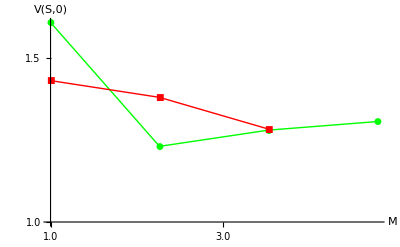

```mathematica
ploutAP=ListLogLogPlot[{Task4AmericanCallBIN,Task4AmericanCallBGA},Joined->True, PlotMarkers->Automatic,PlotStyle->{Green,Red},AxesLabel->{"M","V(S,0)"}]
```

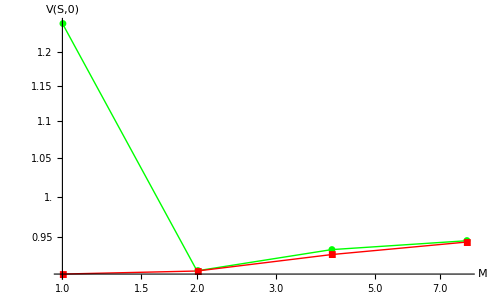

```mathematica
ploutAP=ListLogLogPlot[{Task4AmericanPutBIN,Task4AmericanPutBGA},Joined->True, PlotMarkers->Automatic,PlotRange->Full,PlotStyle->{Green,Red},AxesLabel->{"M","V(S,0)"}]
```

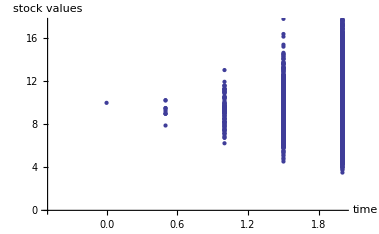

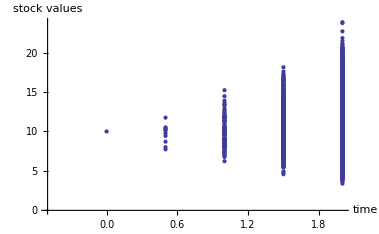

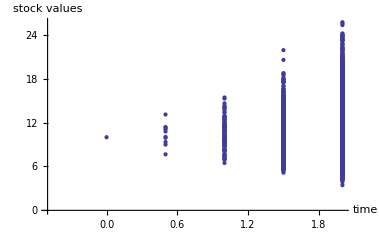

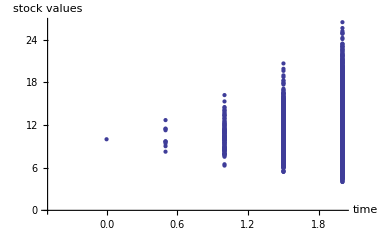

```mathematica
ListPlot[Task4MeshSimulationTreeData1,AxesOrigin->{-0.5,0},AxesLabel->{"time","stock values"}]
ListPlot[Task4MeshSimulationTreeData2,AxesOrigin->{-0.5,0},AxesLabel->{"time","stock values"}]
ListPlot[Task4MeshSimulationTreeData3,AxesOrigin->{-0.5,0},AxesLabel->{"time","stock values"}]
ListPlot[Task4MeshSimulationTreeData4,AxesOrigin->{-0.5,0},AxesLabel->{"time","stock values"}]
```

```mathematica
Task4MeshSimulationTreeData1={
{0,10},{0.5,9.21536},{1,9.75283},{1.5,7.14327},{2,7.83917},{2,8.84097},{2,6.18499},{2,7.50929},{2,7.3165},{2,7.52452},{2,6.17924},{2,7.43158},{2,5.88428},{2,8.20545},{1.5,8.62448},{2,10.2527},{2,9.43473},{2,6.50046},{2,8.23427},{2,8.13943},{2,9.20925},{2,6.0363},{2,8.88028},{2,8.80539},{2,9.02405},{1.5,9.2973},{2,7.13213},{2,10.0205},{2,11.1728},{2,8.92982},{2,7.32341},{2,6.28533},{2,9.89212},{2,7.97198},{2,10.5119},{2,6.86753},{1.5,11.5816},{2,14.599},{2,10.8465},{2,10.9553},{2,12.1116},{2,11.2275},{2,10.5583},{2,12.7213},{2,12.3451},{2,11.6904},{2,10.7259},{1.5,7.40135},{2,6.42344},{2,6.10248},{2,6.94245},{2,7.40435},{2,7.32939},{2,8.84683},{2,7.83243},{2,8.4368},{2,6.70136},{2,7.44133},{1.5,10.4311},{2,14.4382},{2,12.3889},{2,13.7473},{2,10.502},{2,11.1179},{2,10.0781},{2,14.0146},{2,13.5039},{2,7.61398},{2,11.0829},{1.5,9.75542},{2,9.31279},{2,10.3457},{2,8.822},{2,9.26702},{2,10.4051},{2,9.5981},{2,10.4956},{2,8.80111},{2,11.6366},{2,10.3112},{1.5,11.3094},{2,11.4439},{2,10.5739},{2,9.8122},{2,12.7276},{2,11.7386},{2,13.1145},{2,12.729},{2,11.838},{2,10.5802},{2,8.74776},{1.5,11.8236},{2,12.602},{2,11.2226},{2,12.7159},{2,12.5115},{2,17.1646},{2,9.92852},{2,10.4689},{2,11.5787},{2,12.8774},{2,12.5715},{1.5,9.5825},{2,8.56149},{2,8.7237},{2,13.1769},{2,9.97563},{2,10.0304},{2,10.6984},{2,8.03067},{2,8.31688},{2,10.6101},{2,8.35603},{1,10.2167},{1.5,11.5039},{2,10.0712},{2,9.60835},{2,13.2018},{2,8.89778},{2,12.0679},{2,17.1515},{2,11.8216},{2,11.693},{2,11.1044},{2,12.7608},{1.5,9.26988},{2,8.31694},{2,9.2921},{2,9.16266},{2,9.7377},{2,9.99426},{2,10.506},{2,8.08048},{2,8.87722},{2,8.3807},{2,10.4725},{1.5,10.1811},{2,8.12076},{2,11.3131},{2,8.08156},{2,10.1518},{2,10.2519},{2,9.26683},{2,9.11444},{2,8.96178},{2,9.32278},{2,10.386},{1.5,9.61601},{2,10.6878},{2,8.56078},{2,8.86012},{2,9.57807},{2,12.9739},{2,10.5496},{2,8.77872},{2,10.0737},{2,10.4772},{2,10.7172},{1.5,11.977},{2,12.5615},{2,17.7577},{2,14.0633},{2,12.632},{2,13.1737},{2,11.8669},{2,12.5906},{2,13.0467},{2,13.125},{2,13.2021},{1.5,9.30081},{2,7.58036},{2,10.4634},{2,8.47144},{2,9.12163},{2,8.17442},{2,8.79335},{2,8.04268},{2,10.3217},{2,8.28914},{2,8.74763},{1.5,10.4585},{2,11.8017},{2,10.1334},{2,12.9272},{2,9.92334},{2,10.1265},{2,11.37},{2,10.0827},{2,9.1601},{2,11.5769},{2,9.49553},{1.5,9.47699},{2,9.46053},{2,8.39435},{2,9.62609},{2,9.61645},{2,9.08434},{2,7.51955},{2,9.4415},{2,9.55758},{2,8.23375},{2,8.80855},{1.5,8.92469},{2,9.23293},{2,6.74499},{2,10.0717},{2,9.89085},{2,8.45379},{2,7.70472},{2,7.57541},{2,8.69714},{2,10.4858},{2,9.15101},{1.5,12.5333},{2,11.8451},{2,13.2466},{2,11.1513},{2,10.1549},{2,11.1983},{2,15.7958},{2,14.7506},{2,13.4711},{2,11.3534},{2,13.5402},{1,9.30113},{1.5,6.88096},{2,7.34004},{2,5.10128},{2,5.6908},{2,7.89034},{2,6.61973},{2,6.46558},{2,6.16083},{2,7.46633},{2,6.85985},{2,6.38782},{1.5,11.5226},{2,12.6729},{2,11.7406},{2,13.3657},{2,11.8863},{2,13.2042},{2,10.2362},{2,12.1225},{2,14.0437},{2,11.3697},{2,13.7606},{1.5,7.39251},{2,6.68371},{2,7.17037},{2,5.63989},{2,7.25853},{2,7.90392},{2,8.09463},{2,6.55747},{2,7.16799},{2,8.24203},{2,6.63486},{1.5,11.7895},{2,13.7733},{2,11.5382},{2,17.2836},{2,10.3798},{2,11.2475},{2,10.9228},{2,11.2081},{2,13.3217},{2,10.8081},{2,15.0922},{1.5,8.77508},{2,12.0113},{2,7.85627},{2,6.34004},{2,6.87609},{2,10.7123},{2,6.60258},{2,10.2392},{2,10.1328},{2,8.47191},{2,10.4445},{1.5,9.06804},{2,7.26956},{2,8.16},{2,12.1901},{2,8.19894},{2,8.52516},{2,10.1479},{2,8.76087},{2,9.01091},{2,7.7886},{2,9.18789},{1.5,9.28781},{2,9.05404},{2,10.3476},{2,9.35602},{2,10.3374},{2,12.242},{2,8.95331},{2,8.52802},{2,11.4528},{2,7.59481},{2,8.65903},{1.5,9.78488},{2,8.53552},{2,8.8904},{2,8.71235},{2,9.11858},{2,9.40813},{2,7.48193},{2,10.474},{2,8.42004},{2,9.74086},{2,9.84719},{1.5,12.3643},{2,12.9488},{2,11.1271},{2,11.3109},{2,10.5054},{2,11.3821},{2,9.27506},{2,10.6977},{2,11.9456},{2,10.3763},{2,11.8897},{1.5,13.2795},{2,12.9977},{2,16.7108},{2,15.8219},{2,13.2085},{2,13.8608},{2,14.8104},{2,10.3121},{2,14.5185},{2,14.1807},{2,12.4381},{1,11.1292},{1.5,10.3796},{2,12.3564},{2,8.87264},{2,9.98474},{2,10.9165},{2,9.02547},{2,11.6944},{2,9.02246},{2,12.6485},{2,9.14419},{2,13.8382},{1.5,9.13236},{2,10.5431},{2,11.5512},{2,8.87593},{2,8.89461},{2,10.2458},{2,8.07354},{2,12.8578},{2,8.60069},{2,8.64868},{2,8.79602},{1.5,8.45262},{2,9.77317},{2,9.53266},{2,6.86419},{2,9.79796},{2,6.98048},{2,8.08114},{2,9.08908},{2,9.57079},{2,8.18639},{2,8.57621},{1.5,9.80664},{2,9.38336},{2,8.21659},{2,8.36549},{2,12.444},{2,8.941},{2,9.58688},{2,9.30277},{2,7.52913},{2,8.57414},{2,9.19467},{1.5,11.2498},{2,9.13226},{2,10.6135},{2,11.7664},{2,9.40612},{2,10.0837},{2,11.0848},{2,10.3919},{2,10.0231},{2,9.89671},{2,10.0445},{1.5,8.46348},{2,7.45534},{2,9.48431},{2,9.11148},{2,7.0407},{2,8.61874},{2,7.21086},{2,8.5869},{2,9.01252},{2,8.09266},{2,9.95293},{1.5,15.4099},{2,12.6661},{2,12.7716},{2,18.813},{2,18.1234},{2,13.4314},{2,12.8084},{2,13.7119},{2,19.3387},{2,12.3556},{2,13.6582},{1.5,10.6391},{2,13.1705},{2,9.16809},{2,10.8175},{2,10.2845},{2,9.90878},{2,11.0408},{2,8.16795},{2,9.1948},{2,9.84911},{2,10.9106},{1.5,12.5388},{2,15.9179},{2,17.1735},{2,11.8678},{2,13.4731},{2,10.9242},{2,15.9767},{2,13.8372},{2,13.3037},{2,10.0599},{2,12.7673},{1.5,9.79734},{2,10.1945},{2,12.6861},{2,11.5943},{2,8.15127},{2,12.5053},{2,12.159},{2,13.8208},{2,12.0355},{2,9.75495},{2,9.40209},{1,10.8592},{1.5,9.94871},{2,7.3578},{2,10.0984},{2,9.91147},{2,8.65161},{2,8.02005},{2,11.1674},{2,8.26294},{2,9.15072},{2,11.1279},{2,7.96036},{1.5,11.6535},{2,8.95598},{2,13.1498},{2,10.4728},{2,10.999},{2,9.18003},{2,13.3601},{2,9.85661},{2,10.0834},{2,13.0008},{2,9.35457},{1.5,10.7188},{2,12.5243},{2,10.8689},{2,9.75379},{2,8.65544},{2,10.5538},{2,9.78873},{2,9.91049},{2,11.5771},{2,13.2443},{2,9.67743},{1.5,11.3966},{2,10.9459},{2,12.7847},{2,11.1059},{2,9.8421},{2,11.2839},{2,13.2509},{2,10.4041},{2,11.3031},{2,12.6324},{2,13.84},{1.5,11.09},{2,10.5804},{2,12.0851},{2,12.616},{2,11.456},{2,10.4699},{2,13.0192},{2,11.0301},{2,10.316},{2,9.00289},{2,10.3702},{1.5,10.2536},{2,10.8288},{2,10.8997},{2,10.452},{2,11.432},{2,8.76601},{2,8.37772},{2,9.56082},{2,10.1052},{2,9.32021},{2,10.8508},{1.5,10.6727},{2,11.7058},{2,12.016},{2,10.568},{2,12.7002},{2,8.9578},{2,10.6476},{2,11.5707},{2,12.9895},{2,12.1627},{2,9.23657},{1.5,11.217},{2,10.7445},{2,12.7871},{2,11.9063},{2,11.6767},{2,11.5739},{2,11.5968},{2,10.2719},{2,12.9712},{2,9.92826},{2,10.4406},{1.5,10.8157},{2,11.2104},{2,11.7204},{2,10.5941},{2,12.8185},{2,8.95812},{2,10.2533},{2,15.5895},{2,8.57487},{2,11.6233},{2,10.2767},{1.5,11.7013},{2,12.1045},{2,9.99353},{2,14.8717},{2,9.15626},{2,13.5923},{2,9.35295},{2,12.3109},{2,13.5886},{2,12.5605},{2,11.4407},{1,10.4455},{1.5,11.2396},{2,11.2289},{2,10.6091},{2,13.4859},{2,15.5843},{2,12.5613},{2,10.0807},{2,11.8434},{2,8.71544},{2,10.6664},{2,12.345},{1.5,11.8607},{2,12.172},{2,8.66439},{2,10.5738},{2,11.4833},{2,12.1277},{2,12.8533},{2,11.5882},{2,9.27761},{2,12.686},{2,13.5385},{1.5,8.45773},{2,9.40556},{2,7.93889},{2,8.53159},{2,7.97629},{2,10.218},{2,7.45403},{2,6.81995},{2,8.12055},{2,8.18818},{2,7.57504},{1.5,12.8559},{2,12.2957},{2,17.4007},{2,14.0072},{2,11.9331},{2,13.9266},{2,14.5578},{2,15.5936},{2,10.3914},{2,14.3731},{2,15.5394},{1.5,10.571},{2,10.3922},{2,13.4452},{2,12.4046},{2,11.8995},{2,12.6205},{2,11.6153},{2,8.75491},{2,12.0703},{2,10.281},{2,8.96572},{1.5,9.91082},{2,12.7583},{2,10.2785},{2,10.0436},{2,11.5108},{2,11.6046},{2,8.95117},{2,10.4997},{2,12.3767},{2,10.5267},{2,8.02936},{1.5,10.2137},{2,9.36701},{2,11.47},{2,10.5452},{2,10.8568},{2,8.45907},{2,12.7533},{2,10.8566},{2,11.4396},{2,10.8504},{2,10.1853},{1.5,8.42703},{2,8.59155},{2,10.0947},{2,7.77574},{2,11.1415},{2,8.70753},{2,8.42252},{2,8.30055},{2,9.88957},{2,7.28215},{2,7.24486},{1.5,9.31496},{2,9.50517},{2,11.3836},{2,12.0462},{2,9.03936},{2,11.6086},{2,9.35471},{2,7.83044},{2,10.1631},{2,8.71528},{2,10.8445},{1.5,11.6655},{2,12.1125},{2,10.8633},{2,13.3941},{2,12.114},{2,11.6961},{2,12.7731},{2,11.788},{2,12.1604},{2,12.2364},{2,13.0653},{1,11.9584},{1.5,13.0219},{2,12.6389},{2,14.2806},{2,12.0905},{2,13.3658},{2,13.3804},{2,11.7545},{2,15.2295},{2,15.107},{2,14.8037},{2,13.5643},{1.5,12.0092},{2,13.9794},{2,12.388},{2,11.5144},{2,13.0154},{2,11.5489},{2,14.0723},{2,8.17082},{2,9.9352},{2,12.3414},{2,12.5537},{1.5,10.6543},{2,9.06933},{2,10.5846},{2,10.569},{2,11.9982},{2,9.07464},{2,11.4554},{2,8.5231},{2,9.51133},{2,12.1352},{2,9.54347},{1.5,14.4469},{2,17.6828},{2,16.5475},{2,13.0255},{2,12.4038},{2,13.5092},{2,15.4715},{2,12.5675},{2,15.5724},{2,14.0509},{2,14.1489},{1.5,12.3656},{2,14.5994},{2,12.6446},{2,12.4061},{2,12.7589},{2,14.1928},{2,12.5023},{2,9.73618},{2,9.98239},{2,9.8239},{2,14.4139},{1.5,9.45414},{2,12.3559},{2,6.761},{2,9.22693},{2,9.59216},{2,7.81883},{2,9.72677},{2,9.2479},{2,10.224},{2,9.4777},{2,9.52124},{1.5,12.1689},{2,11.2834},{2,14.9045},{2,14.473},{2,11.1629},{2,10.7171},{2,12.6183},{2,14.204},{2,11.6394},{2,11.2024},{2,12.3369},{1.5,13.5704},{2,15.1111},{2,13.2044},{2,12.2181},{2,10.4514},{2,13.5207},{2,13.6463},{2,17.3563},{2,12.5242},{2,11.0451},{2,11.6933},{1.5,9.5878},{2,9.65221},{2,10.1698},{2,8.32038},{2,8.99175},{2,9.56452},{2,12.4508},{2,10.5743},{2,8.29479},{2,10.8103},{2,9.20251},{1.5,12.0922},{2,11.3747},{2,12.1291},{2,10.709},{2,13.5469},{2,12.5993},{2,13.7947},{2,12.8958},{2,12.1216},{2,12.5642},{2,11.2628},{1,9.54544},{1.5,7.49971},{2,7.52742},{2,8.80765},{2,6.70983},{2,8.00641},{2,6.94879},{2,6.80809},{2,7.12593},{2,6.54681},{2,8.16116},{2,5.98119},{1.5,10.2871},{2,9.68217},{2,9.3149},{2,8.31916},{2,12.0698},{2,10.0792},{2,10.9013},{2,11.129},{2,11.2884},{2,11.2001},{2,10.6421},{1.5,10.6241},{2,10.0456},{2,9.47348},{2,8.33397},{2,7.07667},{2,11.5641},{2,9.73176},{2,9.50207},{2,10.6065},{2,8.71294},{2,10.0399},{1.5,10.2846},{2,11.2971},{2,9.71984},{2,9.76326},{2,10.2907},{2,13.1703},{2,11.3491},{2,11.9117},{2,9.03577},{2,12.0078},{2,10.5558},{1.5,11.969},{2,13.9356},{2,14.3145},{2,14.5708},{2,12.4845},{2,11.2334},{2,12.4431},{2,13.4053},{2,9.86957},{2,10.2954},{2,14.7385},{1.5,8.91871},{2,9.35621},{2,8.56188},{2,8.48079},{2,9.75161},{2,7.76319},{2,9.30974},{2,7.51431},{2,7.70569},{2,8.73892},{2,11.7641},{1.5,8.90913},{2,8.98493},{2,6.80103},{2,9.58467},{2,9.40016},{2,10.6007},{2,7.89787},{2,8.54273},{2,8.11817},{2,8.02643},{2,7.52632},{1.5,9.06003},{2,8.7561},{2,8.70668},{2,7.95122},{2,8.44177},{2,9.77691},{2,6.89998},{2,8.15124},{2,8.66396},{2,10.2635},{2,7.53084},{1.5,7.65863},{2,5.48203},{2,7.35935},{2,7.24422},{2,7.07786},{2,7.1658},{2,6.24597},{2,6.57171},{2,8.10668},{2,7.33474},{2,8.10775},{1.5,11.4547},{2,12.1969},{2,10.9555},{2,10.9693},{2,11.934},{2,12.9196},{2,13.05},{2,13.9755},{2,12.2893},{2,9.01092},{2,10.5435},{1,9.72767},{1.5,8.37008},{2,7.95753},{2,7.97383},{2,7.53876},{2,11.1105},{2,8.31954},{2,7.49539},{2,8.15563},{2,7.46765},{2,7.40791},{2,6.59892},{1.5,11.2764},{2,13.3808},{2,13.0685},{2,8.55639},{2,9.8025},{2,9.35343},{2,11.2103},{2,9.876},{2,11.3552},{2,10.0174},{2,10.8931},{1.5,9.36696},{2,10.1958},{2,10.1699},{2,8.36207},{2,5.87984},{2,9.85709},{2,8.65758},{2,8.96696},{2,10.4444},{2,8.67721},{2,7.90703},{1.5,10.2871},{2,9.23589},{2,10.6316},{2,8.22054},{2,10.3834},{2,9.3563},{2,9.99186},{2,8.75774},{2,8.87398},{2,8.45041},{2,13.209},{1.5,9.20759},{2,9.70582},{2,8.27781},{2,10.0926},{2,12.7411},{2,9.69539},{2,6.9055},{2,7.90267},{2,7.79095},{2,9.04492},{2,9.65835},{1.5,8.12874},{2,6.72981},{2,8.13779},{2,7.50709},{2,9.9235},{2,8.2997},{2,9.79989},{2,6.74879},{2,10.1882},{2,8.92007},{2,7.44037},{1.5,9.89397},{2,10.0787},{2,10.1075},{2,10.585},{2,9.70469},{2,9.8714},{2,12.5202},{2,11.0192},{2,10.8824},{2,9.98143},{2,9.63735},{1.5,9.01269},{2,9.61966},{2,8.16332},{2,7.98847},{2,9.19323},{2,9.17609},{2,8.58769},{2,8.89334},{2,8.5203},{2,11.3663},{2,8.84114},{1.5,9.19075},{2,8.31849},{2,9.91526},{2,8.63602},{2,8.71506},{2,8.67516},{2,9.70945},{2,8.24068},{2,11.5874},{2,9.83405},{2,9.1176},{1.5,11.6765},{2,10.1195},{2,9.08912},{2,12.1852},{2,10.5116},{2,14.1132},{2,12.9836},{2,10.5361},{2,10.9116},{2,14.6158},{2,12.1695},{1,8.20737},{1.5,8.41248},{2,8.35335},{2,8.9747},{2,8.58697},{2,8.65493},{2,10.1143},{2,7.99007},{2,6.50981},{2,8.59535},{2,8.11412},{2,8.70666},{1.5,10.7644},{2,10.506},{2,11.6264},{2,11.9631},{2,9.01784},{2,12.3631},{2,8.82401},{2,9.82951},{2,9.78556},{2,10.3838},{2,11.2515},{1.5,9.87857},{2,10.3539},{2,10.6976},{2,9.67122},{2,10.7819},{2,8.89032},{2,9.31813},{2,10.9634},{2,10.1749},{2,13.1747},{2,6.55481},{1.5,8.41108},{2,9.49721},{2,8.77779},{2,8.59931},{2,8.0496},{2,11.1901},{2,8.33629},{2,10.4872},{2,8.65866},{2,10.4551},{2,8.5408},{1.5,10.516},{2,10.6696},{2,12.6156},{2,9.69144},{2,10.9156},{2,12.4777},{2,12.4398},{2,12.4668},{2,11.2867},{2,11.0357},{2,10.4051},{1.5,9.93685},{2,9.44322},{2,10.7799},{2,8.8183},{2,8.93813},{2,11.42},{2,11.1442},{2,9.33266},{2,12.8984},{2,7.8889},{2,11.0967},{1.5,6.53857},{2,5.72824},{2,7.47093},{2,5.54285},{2,8.03229},{2,7.60912},{2,5.41688},{2,7.19892},{2,6.14027},{2,6.72379},{2,6.44597},{1.5,8.89483},{2,8.75661},{2,8.63454},{2,9.40947},{2,10.5462},{2,9.45612},{2,6.1047},{2,9.54922},{2,7.82417},{2,8.50956},{2,8.21342},{1.5,9.12101},{2,8.16662},{2,8.48701},{2,7.65552},{2,10.3095},{2,10.2276},{2,8.2059},{2,9.49631},{2,9.4175},{2,8.83955},{2,8.71313},{1.5,7.06771},{2,5.42217},{2,4.95204},{2,6.97725},{2,9.06118},{2,6.5969},{2,7.40809},{2,6.67769},{2,7.86013},{2,8.57831},{2,5.41646},{0.5,8.97613},{1,8.20619},{1.5,7.75888},{2,7.99966},{2,7.05574},{2,8.54981},{2,7.45715},{2,8.87021},{2,8.55332},{2,6.70979},{2,9.46515},{2,7.66774},{2,9.16904},{1.5,9.18192},{2,9.16385},{2,7.18193},{2,9.40849},{2,10.0768},{2,7.25918},{2,9.28615},{2,9.34338},{2,10.9306},{2,11.7282},{2,8.45662},{1.5,9.79954},{2,7.59315},{2,10.2743},{2,11.444},{2,9.16663},{2,10.2624},{2,12.1416},{2,10.3941},{2,11.8637},{2,9.94919},{2,8.71047},{1.5,9.75098},{2,10.2069},{2,9.62835},{2,8.97129},{2,8.76744},{2,10.3466},{2,12.3166},{2,11.8471},{2,9.40571},{2,7.63544},{2,9.07108},{1.5,8.9762},{2,7.99802},{2,8.84083},{2,9.35048},{2,9.98717},{2,9.38725},{2,8.5273},{2,10.5364},{2,7.93389},{2,5.15231},{2,6.8561},{1.5,10.812},{2,8.11213},{2,11.0541},{2,10.9885},{2,9.64108},{2,12.7949},{2,9.30722},{2,11.3201},{2,12.9898},{2,12.8199},{2,11.0805},{1.5,8.55154},{2,6.42741},{2,8.90097},{2,8.50892},{2,7.39966},{2,8.41978},{2,8.75713},{2,9.45501},{2,6.52972},{2,6.57744},{2,7.64167},{1.5,8.58976},{2,8.60327},{2,8.33598},{2,9.04448},{2,10.1498},{2,6.81611},{2,8.87587},{2,10.4878},{2,8.2051},{2,10.34},{2,8.81824},{1.5,7.52187},{2,9.1696},{2,6.6217},{2,8.01811},{2,8.76599},{2,7.20084},{2,9.99809},{2,9.43821},{2,7.7734},{2,6.09635},{2,9.21165},{1.5,6.9015},{2,6.69719},{2,7.44497},{2,5.86236},{2,7.66932},{2,6.72387},{2,7.76468},{2,7.35324},{2,7.57503},{2,7.13179},{2,6.38327},{1,9.06199},{1.5,6.73261},{2,7.56028},{2,6.10076},{2,6.97538},{2,6.64082},{2,6.72937},{2,8.28197},{2,6.76821},{2,6.47002},{2,7.51469},{2,5.94744},{1.5,9.17894},{2,10.0918},{2,10.3175},{2,8.39271},{2,11.1885},{2,7.52335},{2,8.90236},{2,11.647},{2,8.87604},{2,8.68605},{2,9.80042},{1.5,9.31873},{2,10.8463},{2,7.19237},{2,9.05782},{2,12.4302},{2,8.15348},{2,8.14944},{2,8.43625},{2,10.7838},{2,11.1076},{2,9.6715},{1.5,10.9623},{2,9.83837},{2,9.48584},{2,13.661},{2,9.59502},{2,12.7286},{2,10.0734},{2,11.4955},{2,10.4315},{2,11.8463},{2,9.00934},{1.5,7.30746},{2,8.85274},{2,7.14643},{2,6.47683},{2,8.47805},{2,6.15311},{2,6.49428},{2,7.2343},{2,9.83906},{2,7.01279},{2,6.84876},{1.5,9.47626},{2,10.0901},{2,8.37952},{2,10.6795},{2,11.4895},{2,8.22841},{2,9.78466},{2,10.2503},{2,8.8311},{2,10.5843},{2,10.1121},{1.5,8.27337},{2,9.95984},{2,9.66687},{2,6.77788},{2,6.38962},{2,10.0971},{2,7.65617},{2,8.08861},{2,9.18494},{2,6.76603},{2,8.98993},{1.5,9.62477},{2,8.65944},{2,10.8289},{2,8.06598},{2,9.16936},{2,7.99658},{2,10.727},{2,8.55701},{2,7.72494},{2,8.38877},{2,11.909},{1.5,9.75646},{2,8.53344},{2,10.6125},{2,11.9717},{2,12.4923},{2,9.45619},{2,10.9953},{2,10.7618},{2,8.78178},{2,8.2807},{2,11.24},{1.5,7.23631},{2,6.09453},{2,8.75823},{2,6.55725},{2,5.69306},{2,6.33275},{2,6.97131},{2,6.16377},{2,7.8648},{2,7.59296},{2,8.08634},{1,8.2357},{1.5,6.91171},{2,7.4144},{2,4.7511},{2,7.89573},{2,6.0679},{2,6.33295},{2,6.1194},{2,6.93159},{2,5.34535},{2,7.96411},{2,8.4584},{1.5,6.87846},{2,5.72634},{2,6.09958},{2,6.20952},{2,7.75051},{2,8.60504},{2,6.15762},{2,6.42606},{2,7.78272},{2,7.96907},{2,7.65991},{1.5,9.40805},{2,10.0039},{2,11.1149},{2,10.2483},{2,10.2611},{2,9.34758},{2,11.0049},{2,8.13836},{2,8.98604},{2,9.13817},{2,9.42184},{1.5,8.83262},{2,10.069},{2,6.76761},{2,8.96449},{2,8.91342},{2,8.73045},{2,8.56996},{2,10.7876},{2,8.62892},{2,9.46362},{2,8.72918},{1.5,8.54714},{2,10.3138},{2,9.32764},{2,9.10253},{2,6.91355},{2,8.50642},{2,8.14257},{2,7.8436},{2,9.02208},{2,9.53729},{2,11.9502},{1.5,7.71227},{2,5.60523},{2,7.97011},{2,7.10199},{2,8.51901},{2,9.12673},{2,6.86956},{2,6.12098},{2,7.36668},{2,9.30554},{2,10.097},{1.5,8.31765},{2,7.61458},{2,8.17893},{2,6.59636},{2,9.70806},{2,7.9628},{2,8.78852},{2,9.78564},{2,6.95393},{2,9.55097},{2,6.82857},{1.5,8.58841},{2,8.37242},{2,6.69446},{2,9.73155},{2,8.9703},{2,6.45849},{2,7.79542},{2,9.40322},{2,8.2394},{2,9.6535},{2,7.33917},{1.5,8.40379},{2,8.21083},{2,8.20809},{2,7.23771},{2,9.50233},{2,8.67272},{2,10.5001},{2,7.35478},{2,7.94923},{2,8.69228},{2,10.8305},{1.5,6.95972},{2,8.45361},{2,5.07741},{2,7.91943},{2,6.67479},{2,8.80108},{2,5.22617},{2,8.63418},{2,7.51676},{2,8.2554},{2,7.6731},{1,7.87759},{1.5,7.82508},{2,7.7102},{2,8.47498},{2,6.55063},{2,8.12388},{2,6.71849},{2,7.2394},{2,6.69241},{2,7.62158},{2,10.0269},{2,7.0171},{1.5,7.28655},{2,7.869},{2,5.4393},{2,6.69876},{2,8.4761},{2,9.53287},{2,8.60124},{2,10.7409},{2,6.4662},{2,8.45244},{2,5.92929},{1.5,5.93616},{2,5.40462},{2,4.99362},{2,4.89866},{2,5.48247},{2,5.32806},{2,5.32514},{2,5.60103},{2,6.61776},{2,6.77985},{2,4.66923},{1.5,8.20029},{2,7.8106},{2,9.4623},{2,7.03577},{2,9.54704},{2,6.72843},{2,7.45768},{2,7.13886},{2,9.72512},{2,7.36914},{2,9.0856},{1.5,6.66985},{2,7.18277},{2,6.89865},{2,6.26395},{2,7.19922},{2,6.07372},{2,5.45988},{2,5.87078},{2,7.3503},{2,6.86654},{2,6.8914},{1.5,8.92258},{2,9.47159},{2,9.58335},{2,8.22716},{2,9.11166},{2,8.84582},{2,7.95238},{2,7.87742},{2,7.72226},{2,8.23031},{2,8.86065},{1.5,6.58867},{2,7.05036},{2,6.65322},{2,5.47626},{2,6.49881},{2,6.6586},{2,7.43828},{2,7.4071},{2,5.5697},{2,6.19803},{2,6.40321},{1.5,10.4759},{2,11.4102},{2,9.28456},{2,8.85662},{2,10.3917},{2,9.23886},{2,10.769},{2,14.4853},{2,11.1543},{2,10.4232},{2,12.9137},{1.5,7.95064},{2,8.67691},{2,8.67243},{2,7.62469},{2,7.25507},{2,8.51449},{2,7.14171},{2,8.24382},{2,9.38819},{2,8.96849},{2,6.72241},{1.5,7.54866},{2,8.02111},{2,7.96305},{2,7.10277},{2,6.75343},{2,8.407},{2,7.98685},{2,6.55403},{2,7.68325},{2,8.67056},{2,6.44598},{1,9.1592},{1.5,8.38502},{2,7.48273},{2,12.0381},{2,9.08451},{2,6.29096},{2,8.57941},{2,6.45955},{2,7.20308},{2,7.78325},{2,8.41995},{2,10.9931},{1.5,11.687},{2,13.8974},{2,11.7289},{2,9.06858},{2,10.9605},{2,11.6038},{2,11.2534},{2,11.3757},{2,12.8356},{2,10.7558},{2,11.067},{1.5,8.32734},{2,10.4143},{2,8.08971},{2,8.38628},{2,9.37325},{2,6.57988},{2,9.06832},{2,8.89984},{2,8.03222},{2,11.6579},{2,6.85412},{1.5,9.47579},{2,9.38963},{2,9.16415},{2,9.43316},{2,8.3297},{2,9.72383},{2,9.26659},{2,6.87371},{2,8.72966},{2,9.02292},{2,10.0589},{1.5,10.4594},{2,10.777},{2,10.5836},{2,10.6426},{2,9.61941},{2,13.2967},{2,9.2398},{2,10.2251},{2,9.96111},{2,10.2977},{2,12.2917},{1.5,8.82331},{2,10.3626},{2,9.62901},{2,8.36447},{2,7.74472},{2,7.02038},{2,10.7804},{2,10.5503},{2,10.5986},{2,7.88188},{2,8.22947},{1.5,8.22912},{2,8.77458},{2,8.28738},{2,10.2848},{2,8.88013},{2,6.28049},{2,7.46383},{2,8.40428},{2,7.92707},{2,8.99604},{2,9.08745},{1.5,11.2074},{2,12.2459},{2,13.7709},{2,10.6473},{2,11.9351},{2,10.133},{2,14.3509},{2,10.3699},{2,12.4961},{2,14.5849},{2,11.5249},{1.5,10.1856},{2,12.1367},{2,10.9303},{2,8.11822},{2,9.08488},{2,10.0724},{2,11.7508},{2,10.162},{2,9.84805},{2,10.4607},{2,8.20819},{1.5,7.71148},{2,6.14042},{2,8.27645},{2,6.89907},{2,6.19763},{2,7.70286},{2,7.71695},{2,4.7589},{2,8.52828},{2,7.58768},{2,5.9961},{1,7.737},{1.5,7.33193},{2,8.23498},{2,6.89254},{2,8.99104},{2,7.20067},{2,8.09007},{2,7.00005},{2,7.21893},{2,5.76551},{2,7.78803},{2,6.86359},{1.5,7.07937},{2,6.68639},{2,8.92409},{2,6.71384},{2,7.69475},{2,6.74727},{2,8.64464},{2,7.14784},{2,9.92802},{2,5.80081},{2,6.13564},{1.5,7.31145},{2,8.65825},{2,7.31918},{2,7.10827},{2,7.91622},{2,8.30549},{2,7.28746},{2,8.67012},{2,7.86144},{2,6.39236},{2,8.6708},{1.5,6.88839},{2,6.67426},{2,7.01742},{2,6.57081},{2,7.46454},{2,7.45891},{2,7.42814},{2,7.38062},{2,7.30394},{2,8.73031},{2,7.56586},{1.5,7.80419},{2,7.37543},{2,9.35195},{2,6.94431},{2,8.66088},{2,8.49586},{2,7.63224},{2,7.27356},{2,8.30339},{2,7.61128},{2,9.74913},{1.5,9.40189},{2,9.1712},{2,7.37498},{2,8.46827},{2,9.58356},{2,10.882},{2,11.605},{2,7.29793},{2,10.5343},{2,9.35614},{2,9.29587},{1.5,8.37984},{2,8.98368},{2,9.60512},{2,8.75393},{2,7.61841},{2,6.51825},{2,6.38956},{2,8.24006},{2,9.14232},{2,9.28529},{2,7.87878},{1.5,7.32291},{2,7.62055},{2,7.65831},{2,7.14224},{2,7.83731},{2,9.01657},{2,8.51876},{2,7.30376},{2,9.42352},{2,6.54664},{2,8.62679},{1.5,7.83507},{2,8.18325},{2,7.43841},{2,10.1959},{2,7.06091},{2,6.92334},{2,8.90796},{2,8.67876},{2,9.70851},{2,8.71923},{2,9.33917},{1.5,7.29552},{2,7.90178},{2,7.17816},{2,8.26507},{2,6.85145},{2,7.93617},{2,7.02203},{2,8.72388},{2,7.65286},{2,6.3394},{2,5.64744},{1,11.2566},{1.5,11.0628},{2,9.40607},{2,12.7936},{2,11.8162},{2,12.7853},{2,11.8321},{2,11.475},{2,10.3133},{2,9.79695},{2,12.075},{2,11.7314},{1.5,11.3721},{2,11.0015},{2,11.9183},{2,10.9973},{2,10.6262},{2,10.1202},{2,10.8544},{2,7.60271},{2,14.1062},{2,10.6847},{2,12.8695},{1.5,11.3681},{2,9.63584},{2,13.8404},{2,11.0078},{2,11.6108},{2,12.2994},{2,10.4245},{2,10.7812},{2,10.722},{2,10.3678},{2,12.1666},{1.5,11.4295},{2,12.7589},{2,12.0841},{2,10.5041},{2,9.96717},{2,15.5531},{2,14.116},{2,11.172},{2,9.77562},{2,11.7968},{2,11.2612},{1.5,9.49047},{2,10.7057},{2,10.8596},{2,9.16473},{2,8.14197},{2,8.02655},{2,9.42279},{2,8.02963},{2,8.53001},{2,10.9167},{2,8.04583},{1.5,9.45332},{2,10.2322},{2,8.53562},{2,7.70102},{2,6.95926},{2,8.42191},{2,10.4159},{2,8.87572},{2,8.04032},{2,8.6492},{2,8.46044},{1.5,10.9015},{2,10.2216},{2,9.80182},{2,11.6106},{2,9.41368},{2,10.7178},{2,10.6119},{2,12.4554},{2,10.1614},{2,11.3785},{2,10.7657},{1.5,16.1614},{2,15.8349},{2,13.7058},{2,15.365},{2,16.798},{2,14.5022},{2,14.5036},{2,17.6573},{2,15.4627},{2,17.681},{2,19.4997},{1.5,11.1564},{2,11.1692},{2,9.13947},{2,12.3575},{2,12.5602},{2,9.57439},{2,15.0902},{2,13.6469},{2,11.3676},{2,10.2399},{2,9.74901},{1.5,11.0135},{2,10.5148},{2,9.31698},{2,11.8206},{2,11.7651},{2,13.6074},{2,11.9701},{2,10.6099},{2,11.8152},{2,8.31113},{2,12.9609},{1,8.28311},{1.5,8.59434},{2,6.88358},{2,12.1837},{2,8.05898},{2,9.68675},{2,11.5805},{2,9.92417},{2,7.99632},{2,8.40174},{2,8.24938},{2,8.76274},{1.5,8.63866},{2,7.14917},{2,11.3535},{2,7.5458},{2,7.71095},{2,10.2478},{2,8.99306},{2,8.35468},{2,8.04076},{2,9.55102},{2,9.70602},{1.5,10.4278},{2,9.84412},{2,11.7612},{2,7.82582},{2,10.2499},{2,12.16},{2,12.3841},{2,11.6065},{2,9.20748},{2,9.35956},{2,10.1872},{1.5,9.76805},{2,10.3225},{2,10.4581},{2,7.43362},{2,8.63362},{2,9.75324},{2,12.0663},{2,8.33981},{2,10.439},{2,9.98895},{2,8.9854},{1.5,8.64062},{2,9.04045},{2,7.44517},{2,7.70784},{2,7.32874},{2,8.5831},{2,11.4968},{2,10.9871},{2,10.1286},{2,9.64815},{2,9.07523},{1.5,8.20807},{2,8.50567},{2,7.49745},{2,8.56418},{2,8.1786},{2,7.18408},{2,7.0461},{2,7.40282},{2,7.68819},{2,8.68509},{2,9.41558},{1.5,6.80204},{2,6.47455},{2,5.81253},{2,6.07557},{2,7.92579},{2,7.75218},{2,8.23979},{2,7.28297},{2,5.96026},{2,7.96686},{2,7.43983},{1.5,7.99694},{2,7.84338},{2,8.25711},{2,9.25159},{2,9.06201},{2,7.42399},{2,7.14756},{2,7.78455},{2,8.05808},{2,6.01365},{2,7.86246},{1.5,7.91485},{2,9.82544},{2,9.31742},{2,7.67531},{2,6.79373},{2,7.39304},{2,8.25676},{2,8.16082},{2,7.31003},{2,6.49602},{2,8.85126},{1.5,9.52592},{2,10.4798},{2,7.28285},{2,9.29956},{2,10.4438},{2,9.98672},{2,10.9075},{2,11.861},{2,9.32824},{2,8.34638},{2,12.048},{1,9.46717},{1.5,9.62697},{2,11.2835},{2,8.49613},{2,8.3494},{2,10.2814},{2,9.55157},{2,10.3},{2,8.93823},{2,11.3252},{2,8.31334},{2,12.5829},{1.5,8.39459},{2,7.18813},{2,10.5138},{2,7.62374},{2,10.1394},{2,7.1613},{2,9.87349},{2,9.85602},{2,8.55493},{2,6.95551},{2,8.0697},{1.5,10.4229},{2,10.038},{2,13.3351},{2,9.53803},{2,9.35031},{2,9.37561},{2,12.5105},{2,11.0818},{2,11.9258},{2,10.087},{2,8.94059},{1.5,9.99511},{2,8.63099},{2,9.27142},{2,7.59636},{2,9.05852},{2,10.5458},{2,9.60892},{2,10.6469},{2,10.022},{2,10.6774},{2,9.37313},{1.5,9.20703},{2,11.4807},{2,5.46051},{2,9.40703},{2,12.3123},{2,10.2171},{2,7.57796},{2,7.89943},{2,10.8203},{2,7.77656},{2,10.3359},{1.5,6.14292},{2,7.00474},{2,6.93675},{2,5.12132},{2,7.20499},{2,4.70183},{2,6.67162},{2,5.04387},{2,7.12604},{2,5.29113},{2,6.22205},{1.5,9.00106},{2,7.26207},{2,11.553},{2,8.64841},{2,9.57457},{2,7.63058},{2,9.52421},{2,6.97145},{2,9.37963},{2,10.0459},{2,8.95085},{1.5,10.495},{2,10.4285},{2,9.26476},{2,10.4001},{2,12.9243},{2,10.6292},{2,11.0693},{2,11.2378},{2,12.6984},{2,11.9419},{2,11.6139},{1.5,8.41719},{2,7.66967},{2,6.65885},{2,5.6351},{2,7.06082},{2,8.03729},{2,7.25044},{2,9.11663},{2,7.56508},{2,8.59466},{2,8.69376},{1.5,9.71013},{2,9.59105},{2,8.91075},{2,9.97263},{2,7.61797},{2,9.72627},{2,10.4948},{2,10.1008},{2,12.9163},{2,10.155},{2,9.41183},{1,9.07885},{1.5,9.38373},{2,11.1261},{2,10.4775},{2,10.9011},{2,6.89626},{2,11.868},{2,9.43327},{2,10.2866},{2,11.224},{2,10.3106},{2,9.06829},{1.5,7.05432},{2,7.29829},{2,6.98282},{2,7.22874},{2,5.56744},{2,7.67122},{2,5.28699},{2,8.50278},{2,5.82656},{2,7.75579},{2,7.1367},{1.5,9.66106},{2,10.0701},{2,11.3901},{2,9.17387},{2,10.0332},{2,10.8854},{2,10.9875},{2,12.7476},{2,9.24967},{2,7.22878},{2,6.79832},{1.5,7.884},{2,7.08449},{2,5.78065},{2,9.0164},{2,7.89118},{2,7.88481},{2,7.66745},{2,7.92798},{2,7.81436},{2,10.0747},{2,7.60653},{1.5,11.618},{2,10.104},{2,10.2328},{2,15.2071},{2,12.576},{2,11.9871},{2,11.9629},{2,12.2253},{2,10.8271},{2,12.3498},{2,11.3182},{1.5,10.6738},{2,10.7884},{2,7.84923},{2,9.49654},{2,11.7314},{2,12.3805},{2,9.6675},{2,10.0786},{2,9.16716},{2,13.9646},{2,11.9372},{1.5,7.72327},{2,8.24067},{2,7.01839},{2,9.8891},{2,6.44045},{2,9.42527},{2,8.96618},{2,7.59952},{2,7.37845},{2,8.09721},{2,10.4203},{1.5,8.95606},{2,10.9232},{2,7.70629},{2,9.32671},{2,11.7294},{2,10.5644},{2,7.04764},{2,7.53558},{2,7.93818},{2,7.18686},{2,7.90497},{1.5,8.23595},{2,8.14913},{2,6.90896},{2,10.2938},{2,8.01853},{2,7.71278},{2,9.25615},{2,7.58872},{2,9.1509},{2,8.6819},{2,8.9131},{1.5,8.62208},{2,7.57838},{2,9.49742},{2,9.68813},{2,6.77927},{2,8.22689},{2,8.22531},{2,7.54429},{2,8.14639},{2,7.41822},{2,8.58544},{0.5,9.0078},{1,9.15165},{1.5,7.23264},{2,9.58671},{2,6.56968},{2,8.80752},{2,7.55918},{2,5.52415},{2,7.95213},{2,8.23184},{2,8.91887},{2,8.26305},{2,6.88793},{1.5,10.5224},{2,10.0949},{2,10.2223},{2,13.3387},{2,12.0026},{2,11.7547},{2,9.55455},{2,15.2132},{2,12.9913},{2,12.414},{2,10.3403},{1.5,11.3681},{2,11.7657},{2,13.0375},{2,11.4831},{2,12.5707},{2,8.72963},{2,10.7892},{2,9.51627},{2,9.76016},{2,10.7282},{2,11.0489},{1.5,7.71599},{2,8.53477},{2,8.34155},{2,6.54038},{2,8.51016},{2,6.99347},{2,6.58394},{2,8.77204},{2,8.9104},{2,8.25806},{2,6.8359},{1.5,10.5014},{2,11.7134},{2,11.6403},{2,13.7659},{2,9.09159},{2,8.88888},{2,13.4506},{2,10.0293},{2,7.87019},{2,11.5831},{2,11.0744},{1.5,7.88627},{2,8.15104},{2,7.615},{2,8.54042},{2,7.13945},{2,7.7747},{2,7.30686},{2,7.08047},{2,5.81622},{2,7.58417},{2,7.72661},{1.5,10.2289},{2,10.1437},{2,13.5396},{2,8.5202},{2,8.59464},{2,9.67218},{2,10.4852},{2,9.25088},{2,10.7078},{2,12.3093},{2,7.55783},{1.5,8.77704},{2,7.80283},{2,7.61193},{2,7.43408},{2,7.75112},{2,8.634},{2,9.26346},{2,10.1018},{2,10.9581},{2,6.14691},{2,8.2146},{1.5,11.8846},{2,9.36363},{2,10.6539},{2,12.1882},{2,12.7638},{2,13.0904},{2,10.5747},{2,8.82625},{2,11.3979},{2,11.7473},{2,12.4527},{1.5,8.92624},{2,10.0956},{2,8.73827},{2,8.43349},{2,11.8916},{2,9.26039},{2,8.88272},{2,8.95516},{2,9.15035},{2,10.1973},{2,11.1853},{1,6.23974},{1.5,7.06538},{2,8.17588},{2,8.14251},{2,8.00155},{2,7.17782},{2,6.42309},{2,7.58379},{2,5.63544},{2,7.01926},{2,6.57054},{2,7.86915},{1.5,7.28539},{2,6.9071},{2,7.94529},{2,8.22357},{2,7.57855},{2,6.94449},{2,6.50562},{2,7.18463},{2,8.57411},{2,7.13003},{2,7.3357},{1.5,7.04101},{2,7.8544},{2,7.98272},{2,7.99719},{2,6.64621},{2,5.6122},{2,5.52364},{2,7.30539},{2,6.54674},{2,9.06413},{2,6.44083},{1.5,5.07006},{2,6.04712},{2,6.677},{2,5.51052},{2,6.53407},{2,4.55308},{2,4.7642},{2,4.86974},{2,5.01775},{2,4.63187},{2,4.20167},{1.5,5.50971},{2,6.6242},{2,6.59057},{2,5.56655},{2,7.69477},{2,4.84771},{2,5.60675},{2,5.84785},{2,5.80435},{2,4.75485},{2,6.49601},{1.5,7.03809},{2,6.68544},{2,5.80863},{2,6.64012},{2,8.70564},{2,7.59935},{2,7.54359},{2,7.85221},{2,6.48484},{2,6.43034},{2,8.21574},{1.5,5.18957},{2,5.08208},{2,5.52267},{2,5.0624},{2,4.74163},{2,5.60977},{2,5.75679},{2,5.53752},{2,5.53248},{2,5.66933},{2,5.1574},{1.5,8.26807},{2,9.14463},{2,6.34319},{2,8.77786},{2,12.1021},{2,8.56674},{2,8.96022},{2,12.8671},{2,7.30245},{2,9.29593},{2,9.27151},{1.5,6.2146},{2,7.05844},{2,6.26638},{2,5.46208},{2,6.65275},{2,7.81092},{2,5.78462},{2,7.7358},{2,4.78365},{2,7.01748},{2,7.13912},{1.5,6.49339},{2,5.90422},{2,4.58109},{2,7.51687},{2,5.19194},{2,8.53086},{2,5.86712},{2,7.65386},{2,6.77081},{2,7.62737},{2,6.15165},{1,11.3452},{1.5,14.0406},{2,12.9818},{2,14.0243},{2,13.5879},{2,17.9344},{2,10.9739},{2,13.9497},{2,12.0469},{2,13.1166},{2,14.0543},{2,13.883},{1.5,10.235},{2,8.16042},{2,9.57435},{2,11.3731},{2,8.71934},{2,7.24135},{2,8.69682},{2,9.65477},{2,10.4003},{2,8.92573},{2,9.78602},{1.5,9.31703},{2,8.1373},{2,9.91226},{2,10.149},{2,9.27408},{2,9.55671},{2,10.5502},{2,13.4068},{2,10.8653},{2,10.6713},{2,9.60446},{1.5,13.0613},{2,14.8269},{2,15.7705},{2,13.2777},{2,12.2624},{2,16.8821},{2,11.6354},{2,13.0017},{2,11.2342},{2,13.0135},{2,11.7943},{1.5,10.3856},{2,8.50902},{2,9.5293},{2,10.9556},{2,11.1225},{2,8.95119},{2,10.4768},{2,12.5559},{2,12.3002},{2,12.5189},{2,13.5643},{1.5,11.1961},{2,12.3799},{2,12.0613},{2,10.5518},{2,9.73719},{2,10.1806},{2,10.0719},{2,10.4683},{2,10.2528},{2,14.3982},{2,11.7629},{1.5,12.1156},{2,9.59322},{2,13.1826},{2,16.5632},{2,12.3904},{2,14.4964},{2,17.3726},{2,10.4091},{2,10.3386},{2,12.4049},{2,12.445},{1.5,12.6123},{2,11.2724},{2,12.1754},{2,12.1636},{2,11.6916},{2,12.4449},{2,11.8376},{2,14.218},{2,11.1967},{2,11.2392},{2,14.4602},{1.5,10.284},{2,7.40144},{2,14.204},{2,10.6252},{2,10.051},{2,8.57979},{2,11.1639},{2,13.4364},{2,12.2117},{2,11.2694},{2,10.8112},{1.5,12.425},{2,11.943},{2,12.241},{2,10.606},{2,12.8462},{2,11.113},{2,13.0817},{2,13.0894},{2,12.0119},{2,12.9327},{2,11.1768},{1,11.244},{1.5,11.2135},{2,11.5269},{2,8.81163},{2,11.508},{2,9.30313},{2,14.2228},{2,12.4801},{2,11.0225},{2,9.51065},{2,12.4936},{2,13.8919},{1.5,9.66938},{2,10.2576},{2,10.1562},{2,10.934},{2,9.98378},{2,8.93116},{2,8.92974},{2,8.03268},{2,10.3963},{2,10.3583},{2,9.14176},{1.5,17.811},{2,21.2197},{2,16.1058},{2,17.3867},{2,17.1996},{2,23.7026},{2,21.6019},{2,16.9014},{2,20.1832},{2,20.7765},{2,19.1668},{1.5,12.9528},{2,13.1795},{2,12.7499},{2,13.9515},{2,15.7026},{2,12.5831},{2,13.1204},{2,11.7511},{2,13.4241},{2,10.1098},{2,13.3359},{1.5,10.8466},{2,10.8695},{2,11.9313},{2,9.18878},{2,10.4378},{2,10.4241},{2,11.308},{2,10.1257},{2,9.48702},{2,9.47023},{2,11.6089},{1.5,14.1146},{2,13.4787},{2,14.3717},{2,17.6881},{2,14.2971},{2,13.5085},{2,11.4278},{2,10.2278},{2,12.8207},{2,13.0655},{2,11.6528},{1.5,10.6672},{2,10.5382},{2,9.20707},{2,9.24114},{2,10.9938},{2,9.81621},{2,9.88393},{2,12.3688},{2,10.8778},{2,9.79945},{2,11.8859},{1.5,10.0287},{2,9.32716},{2,11.6656},{2,8.29404},{2,9.82961},{2,11.5496},{2,13.9309},{2,11.1561},{2,9.07885},{2,10.3499},{2,9.77765},{1.5,9.75878},{2,11.1344},{2,11.5162},{2,10.4807},{2,8.42904},{2,9.89359},{2,11.7143},{2,13.6338},{2,7.80895},{2,9.94582},{2,10.3579},{1.5,10.0962},{2,10.3071},{2,11.301},{2,9.33234},{2,10.0445},{2,9.69144},{2,8.756},{2,9.32421},{2,9.10346},{2,10.6285},{2,8.6237},{1,6.78491},{1.5,6.54347},{2,5.83502},{2,8.27214},{2,7.30492},{2,6.7869},{2,7.20541},{2,8.00426},{2,6.63161},{2,6.69471},{2,6.58983},{2,9.23909},{1.5,6.54977},{2,7.16551},{2,7.23781},{2,6.26502},{2,7.25155},{2,6.6939},{2,5.88964},{2,5.93745},{2,8.02706},{2,5.61747},{2,6.34689},{1.5,6.73417},{2,7.43016},{2,5.89848},{2,7.17295},{2,8.1636},{2,6.69515},{2,5.66897},{2,8.44742},{2,9.1283},{2,6.01469},{2,5.64211},{1.5,6.20552},{2,6.47673},{2,6.24888},{2,6.02372},{2,5.64846},{2,8.41825},{2,5.64441},{2,5.81689},{2,5.73641},{2,7.12489},{2,6.21973},{1.5,6.86111},{2,6.19755},{2,7.22658},{2,6.09897},{2,7.93315},{2,5.63968},{2,5.97043},{2,7.50539},{2,7.23191},{2,7.19514},{2,6.70643},{1.5,8.06635},{2,7.61327},{2,6.7617},{2,7.50809},{2,11.9627},{2,6.83429},{2,7.88366},{2,8.18067},{2,7.65747},{2,6.60922},{2,7.64272},{1.5,5.8742},{2,6.23472},{2,5.16388},{2,6.42856},{2,5.49947},{2,6.95958},{2,6.09951},{2,6.71404},{2,5.95437},{2,6.44779},{2,6.15031},{1.5,5.41195},{2,5.38378},{2,3.82733},{2,5.74246},{2,5.7892},{2,5.6123},{2,3.51441},{2,4.75085},{2,4.89038},{2,4.36053},{2,4.82824},{1.5,7.31791},{2,7.24941},{2,6.6513},{2,8.0418},{2,5.95072},{2,7.84232},{2,7.33513},{2,6.09244},{2,7.83219},{2,7.1093},{2,7.9585},{1.5,5.83414},{2,7.07476},{2,7.45737},{2,6.12187},{2,7.2865},{2,6.52938},{2,6.90794},{2,5.56568},{2,5.61113},{2,6.3795},{2,5.40857},{1,9.03301},{1.5,9.50853},{2,9.85442},{2,10.0545},{2,8.82907},{2,7.0021},{2,7.67685},{2,10.2383},{2,9.41689},{2,8.59618},{2,10.0507},{2,11.3274},{1.5,9.02853},{2,10.8202},{2,8.95776},{2,11.0204},{2,11.5688},{2,9.02509},{2,9.50372},{2,10.6754},{2,8.45676},{2,10.9494},{2,6.68397},{1.5,9.14032},{2,7.95619},{2,8.1494},{2,8.22634},{2,9.1473},{2,7.38056},{2,9.73576},{2,8.73043},{2,9.03521},{2,9.04311},{2,9.50712},{1.5,9.27155},{2,8.47562},{2,9.63212},{2,9.83814},{2,8.68988},{2,8.11837},{2,8.54709},{2,8.72639},{2,8.38782},{2,8.93956},{2,11.099},{1.5,8.50816},{2,8.11989},{2,7.86483},{2,8.52216},{2,6.90764},{2,7.73874},{2,7.49855},{2,8.47388},{2,11.8275},{2,6.76305},{2,8.93786},{1.5,9.7725},{2,11.0076},{2,10.6003},{2,10.1343},{2,11.8661},{2,8.87077},{2,8.50369},{2,8.26973},{2,9.703},{2,8.07694},{2,10.7139},{1.5,11.4726},{2,13.0362},{2,9.29337},{2,18.1388},{2,11.9903},{2,10.0834},{2,13.3678},{2,10.8164},{2,11.1657},{2,10.4429},{2,13.8607},{1.5,7.39886},{2,7.0651},{2,8.3022},{2,7.49247},{2,7.54405},{2,6.80758},{2,8.12456},{2,8.48686},{2,5.32789},{2,7.43352},{2,6.11577},{1.5,9.42878},{2,7.8392},{2,9.08251},{2,11.7072},{2,9.14946},{2,10.261},{2,10.3987},{2,8.41061},{2,7.877},{2,10.0767},{2,8.62806},{1.5,9.71712},{2,7.97331},{2,7.07633},{2,9.51749},{2,9.72356},{2,7.90869},{2,8.6693},{2,11.577},{2,9.82057},{2,10.1858},{2,9.68257},{1,8.53077},{1.5,7.73366},{2,7.9745},{2,7.05761},{2,6.24305},{2,8.76767},{2,7.64929},{2,6.59692},{2,7.73488},{2,8.731},{2,7.61035},{2,6.91387},{1.5,7.27029},{2,7.64908},{2,7.4612},{2,6.48204},{2,7.85675},{2,7.94044},{2,6.15659},{2,7.33457},{2,7.39004},{2,7.95134},{2,7.69806},{1.5,8.82215},{2,8.88999},{2,9.14539},{2,8.79075},{2,8.84874},{2,8.31371},{2,7.47679},{2,8.36132},{2,8.39395},{2,10.4465},{2,9.84682},{1.5,9.97138},{2,7.45438},{2,11.2406},{2,8.24567},{2,11.1823},{2,9.34329},{2,12.3322},{2,8.72645},{2,10.5238},{2,8.25818},{2,10.5451},{1.5,9.3889},{2,8.32601},{2,9.32408},{2,9.44094},{2,9.21623},{2,9.00921},{2,9.32456},{2,8.08488},{2,6.60413},{2,10.1},{2,8.56793},{1.5,9.44867},{2,7.73975},{2,9.56531},{2,8.99943},{2,11.197},{2,9.90896},{2,10.0862},{2,7.62116},{2,12.5179},{2,7.89712},{2,8.32633},{1.5,7.50887},{2,9.719},{2,6.23274},{2,7.23608},{2,9.56921},{2,8.41214},{2,6.72908},{2,8.09159},{2,7.77183},{2,6.58971},{2,9.01202},{1.5,7.69671},{2,8.0976},{2,5.75906},{2,6.46664},{2,7.30886},{2,7.58433},{2,8.28011},{2,7.8231},{2,6.50097},{2,8.96911},{2,9.3619},{1.5,10.9846},{2,8.97388},{2,10.9415},{2,9.18775},{2,9.5419},{2,11.9763},{2,11.5457},{2,9.35865},{2,10.9492},{2,10.9321},{2,10.421},{1.5,8.67905},{2,8.54548},{2,10.0501},{2,8.00774},{2,7.31574},{2,9.08394},{2,8.32223},{2,7.57611},{2,7.02901},{2,9.17117},{2,11.2348},{1,11.2886},{1.5,12.568},{2,12.0392},{2,12.9275},{2,13.7598},{2,15.1652},{2,9.3459},{2,15.0031},{2,13.1734},{2,10.8256},{2,13.4656},{2,10.1727},{1.5,10.5483},{2,11.2028},{2,9.71881},{2,8.62985},{2,10.1906},{2,12.2864},{2,10.0929},{2,9.77283},{2,9.24548},{2,11.8245},{2,11.7723},{1.5,11.96},{2,16.1336},{2,10.8733},{2,12.6191},{2,13.8691},{2,9.4837},{2,14.2127},{2,11.2809},{2,12.2885},{2,11.5677},{2,12.0089},{1.5,10.7308},{2,12.6982},{2,10.5975},{2,11.6103},{2,13.2463},{2,11.0813},{2,9.62316},{2,9.2552},{2,9.94757},{2,11.9607},{2,8.6037},{1.5,11.0415},{2,14.0323},{2,11.221},{2,10.4675},{2,9.78855},{2,12.6056},{2,10.8861},{2,10.8708},{2,10.1558},{2,9.24709},{2,10.3593},{1.5,10.4354},{2,10.7694},{2,9.68283},{2,14.2809},{2,9.28543},{2,12.7267},{2,8.88207},{2,9.71493},{2,9.4636},{2,9.63707},{2,10.1036},{1.5,10.2332},{2,9.84478},{2,12.4572},{2,7.96874},{2,9.32921},{2,10.6635},{2,10.7434},{2,10.3544},{2,9.16242},{2,8.45456},{2,8.11418},{1.5,10.5019},{2,11.5837},{2,10.0233},{2,7.13162},{2,12.0998},{2,11.2639},{2,9.82433},{2,12.6635},{2,12.3393},{2,11.3342},{2,13.0461},{1.5,8.05609},{2,7.48887},{2,8.25535},{2,8.15093},{2,7.10377},{2,7.26366},{2,8.80876},{2,6.2198},{2,8.46457},{2,7.14142},{2,8.70582},{1.5,12.283},{2,12.1189},{2,12.6211},{2,15.5855},{2,11.7958},{2,14.6086},{2,12.3968},{2,10.4217},{2,11.8138},{2,10.6238},{2,13.4501},{1,8.07038},{1.5,9.56955},{2,7.29176},{2,11.2293},{2,11.5845},{2,8.7973},{2,9.98312},{2,8.85601},{2,9.45272},{2,9.84692},{2,9.3122},{2,8.38598},{1.5,7.02551},{2,6.3321},{2,7.29271},{2,7.5956},{2,8.65725},{2,8.02735},{2,6.72544},{2,6.23705},{2,7.63504},{2,9.63724},{2,5.84498},{1.5,9.27974},{2,12.72},{2,8.00829},{2,9.89558},{2,9.45539},{2,9.29054},{2,11.7306},{2,9.35774},{2,7.83953},{2,8.93091},{2,10.6088},{1.5,7.65429},{2,6.12088},{2,8.4401},{2,6.72872},{2,8.9766},{2,7.93091},{2,8.84495},{2,7.9823},{2,8.42597},{2,7.55216},{2,7.5739},{1.5,6.3538},{2,5.38157},{2,5.8281},{2,5.85064},{2,6.80887},{2,7.74142},{2,4.72819},{2,7.13687},{2,7.12731},{2,7.46455},{2,5.3423},{1.5,8.91745},{2,7.51165},{2,7.38028},{2,10.7498},{2,5.85863},{2,9.5861},{2,10.3804},{2,9.42504},{2,9.23835},{2,10.1851},{2,8.68072},{1.5,9.14965},{2,8.96521},{2,10.0508},{2,10.1082},{2,8.22608},{2,11.8687},{2,8.60791},{2,8.78529},{2,9.43654},{2,9.55092},{2,11.0847},{1.5,9.17687},{2,9.1698},{2,9.61604},{2,12.5912},{2,10.2344},{2,9.8024},{2,10.5337},{2,12.2877},{2,12.5033},{2,8.59962},{2,9.46185},{1.5,8.34157},{2,6.86344},{2,7.21586},{2,8.15329},{2,7.58497},{2,8.29282},{2,6.44532},{2,9.33045},{2,7.9651},{2,6.90808},{2,10.7625},{1.5,6.9213},{2,8.00918},{2,6.22388},{2,5.1548},{2,7.80255},{2,9.37325},{2,7.40168},{2,8.18116},{2,6.51429},{2,8.37091},{2,7.51899},{1,8.80782},{1.5,10.0491},{2,10.067},{2,10.948},{2,10.8846},{2,10.4659},{2,7.63402},{2,10.246},{2,11.5611},{2,7.74948},{2,11.5026},{2,8.61069},{1.5,7.33139},{2,7.87262},{2,5.89957},{2,7.17106},{2,7.84066},{2,6.1672},{2,6.56252},{2,6.45087},{2,6.50466},{2,6.84218},{2,6.07496},{1.5,7.89382},{2,8.22784},{2,8.03557},{2,9.81681},{2,6.88266},{2,7.36268},{2,6.40144},{2,8.32863},{2,8.19432},{2,9.69453},{2,6.59773},{1.5,9.78102},{2,8.94428},{2,8.28666},{2,10.4552},{2,10.5303},{2,10.3106},{2,10.0983},{2,9.27255},{2,11.9789},{2,8.84339},{2,10.0654},{1.5,9.50428},{2,9.55043},{2,8.77165},{2,9.04566},{2,11.4308},{2,9.75004},{2,10.8657},{2,10.5053},{2,11.6597},{2,8.06606},{2,10.5358},{1.5,9.74356},{2,9.6094},{2,8.80082},{2,8.56173},{2,7.35553},{2,8.54155},{2,8.51269},{2,9.48996},{2,8.37042},{2,10.9122},{2,8.95512},{1.5,8.48919},{2,8.28987},{2,9.28608},{2,10.2859},{2,7.99777},{2,8.02523},{2,7.7501},{2,9.24117},{2,8.74218},{2,9.20137},{2,8.71653},{1.5,8.83835},{2,9.47847},{2,8.35368},{2,6.97452},{2,9.5858},{2,8.23722},{2,8.24119},{2,8.062},{2,11.2462},{2,9.88687},{2,9.91041},{1.5,8.10409},{2,9.62166},{2,7.62138},{2,7.50068},{2,9.36172},{2,7.07736},{2,6.22823},{2,8.71656},{2,8.21524},{2,6.67882},{2,8.15146},{1.5,10.9854},{2,12.1717},{2,10.1177},{2,12.872},{2,9.87049},{2,12.4835},{2,10.7519},{2,11.1373},{2,10.9656},{2,14.2102},{2,11.2205},{0.5,8.98862},{1,7.10985},{1.5,8.69747},{2,8.47534},{2,8.65712},{2,8.94224},{2,10.9131},{2,7.02358},{2,7.0403},{2,9.20924},{2,8.159},{2,11.8453},{2,9.05321},{1.5,7.24853},{2,5.46489},{2,7.8861},{2,7.49385},{2,6.73154},{2,8.79857},{2,5.8908},{2,8.20567},{2,7.82265},{2,7.124},{2,6.79452},{1.5,8.56496},{2,8.79443},{2,8.25299},{2,7.81501},{2,7.73489},{2,9.21163},{2,9.27487},{2,9.31794},{2,6.9402},{2,8.97502},{2,6.56084},{1.5,6.18572},{2,7.20876},{2,7.42649},{2,5.77446},{2,5.71999},{2,5.61057},{2,7.34633},{2,7.16014},{2,5.39892},{2,5.58601},{2,5.35573},{1.5,7.5455},{2,5.3914},{2,8.52528},{2,6.97046},{2,7.18758},{2,7.20995},{2,6.28793},{2,7.18242},{2,6.74663},{2,7.27006},{2,8.06615},{1.5,6.33532},{2,6.71717},{2,6.9147},{2,6.87097},{2,7.20053},{2,5.48094},{2,7.43564},{2,5.42049},{2,5.57943},{2,9.30258},{2,5.80452},{1.5,5.92319},{2,7.84087},{2,5.55451},{2,6.10354},{2,6.30422},{2,5.83935},{2,6.08796},{2,5.31076},{2,5.35346},{2,4.75903},{2,6.32512},{1.5,6.72298},{2,5.8081},{2,6.76619},{2,7.28255},{2,8.18005},{2,5.51709},{2,7.55953},{2,7.90474},{2,6.20061},{2,6.20772},{2,6.75042},{1.5,6.42485},{2,6.83371},{2,8.1193},{2,5.91219},{2,4.63005},{2,6.42069},{2,7.87716},{2,5.89549},{2,5.59671},{2,6.37542},{2,6.18774},{1.5,5.80827},{2,5.81267},{2,5.66635},{2,7.75662},{2,4.70412},{2,5.9403},{2,5.95819},{2,5.87952},{2,5.23339},{2,5.97799},{2,6.27426},{1,9.30267},{1.5,12.3228},{2,9.80375},{2,13.1432},{2,14.6003},{2,12.6543},{2,11.4505},{2,10.0658},{2,12.7909},{2,11.2775},{2,11.123},{2,11.1113},{1.5,7.39551},{2,7.22379},{2,8.12038},{2,9.72606},{2,8.11468},{2,6.49925},{2,5.83842},{2,8.33563},{2,6.82029},{2,8.2015},{2,8.88417},{1.5,8.40904},{2,9.27286},{2,8.22742},{2,7.60192},{2,7.41126},{2,8.90617},{2,8.22135},{2,7.75553},{2,7.37813},{2,10.24},{2,6.60562},{1.5,9.22373},{2,7.62635},{2,9.1439},{2,9.94565},{2,9.4897},{2,8.56829},{2,8.82812},{2,7.43007},{2,11.9955},{2,9.21439},{2,11.2491},{1.5,11.6226},{2,9.43006},{2,11.049},{2,10.0961},{2,13.7969},{2,14.0184},{2,11.299},{2,11.8287},{2,11.8694},{2,12.8265},{2,10.8035},{1.5,7.36828},{2,6.73852},{2,6.42183},{2,8.38264},{2,7.48205},{2,6.8365},{2,8.0562},{2,6.31471},{2,6.99339},{2,8.21535},{2,7.01905},{1.5,9.09306},{2,10.6043},{2,9.13958},{2,7.10294},{2,8.89054},{2,9.60565},{2,7.20487},{2,8.23673},{2,7.52449},{2,7.38657},{2,10.4187},{1.5,11.3118},{2,9.14602},{2,11.2256},{2,13.3369},{2,10.6684},{2,11.458},{2,12.0559},{2,9.93853},{2,11.8398},{2,14.2317},{2,11.9531},{1.5,7.09633},{2,6.80995},{2,8.23963},{2,7.77008},{2,8.44106},{2,9.29431},{2,8.19927},{2,7.45188},{2,7.57127},{2,10.0106},{2,6.07508},{1.5,8.18277},{2,8.65505},{2,7.31096},{2,9.33748},{2,7.55193},{2,7.39916},{2,7.45304},{2,8.6326},{2,9.17129},{2,7.01007},{2,8.12834},{1,8.66848},{1.5,9.34197},{2,6.97238},{2,8.14145},{2,7.85735},{2,10.2327},{2,7.98012},{2,11.6508},{2,8.23802},{2,10.8042},{2,9.11272},{2,8.64708},{1.5,10.4614},{2,8.70948},{2,11.368},{2,12.3532},{2,11.8802},{2,10.2501},{2,9.43403},{2,13.6374},{2,12.4374},{2,11.1128},{2,13.1651},{1.5,7.00753},{2,7.34216},{2,7.11094},{2,9.4384},{2,7.47948},{2,7.47474},{2,7.86107},{2,6.34293},{2,9.63223},{2,7.43109},{2,8.11822},{1.5,8.39485},{2,7.07339},{2,7.77284},{2,6.36038},{2,9.90501},{2,8.50911},{2,9.47707},{2,6.53347},{2,7.77544},{2,9.86521},{2,7.14105},{1.5,8.56675},{2,6.51174},{2,8.35555},{2,9.74187},{2,7.72627},{2,7.89744},{2,9.02018},{2,7.65719},{2,7.04856},{2,8.65368},{2,7.03969},{1.5,10.2782},{2,10.862},{2,9.33713},{2,10.9581},{2,7.67138},{2,10.0353},{2,8.62219},{2,11.0041},{2,11.4309},{2,11.2036},{2,10.7974},{1.5,9.16637},{2,10.449},{2,9.17646},{2,9.16036},{2,8.61092},{2,12.4408},{2,11.3321},{2,10.239},{2,9.91683},{2,9.44704},{2,7.80973},{1.5,7.72974},{2,7.12328},{2,7.93685},{2,8.72587},{2,7.57143},{2,8.62636},{2,7.37186},{2,8.4652},{2,9.67841},{2,7.91285},{2,8.78582},{1.5,7.19869},{2,6.14663},{2,7.46487},{2,7.14078},{2,5.96611},{2,6.83082},{2,6.12005},{2,7.11534},{2,6.05545},{2,6.02744},{2,5.66154},{1.5,6.45682},{2,5.94489},{2,7.5189},{2,6.38755},{2,6.81493},{2,5.68107},{2,6.32732},{2,6.50379},{2,6.28201},{2,6.85074},{2,8.15802},{1,9.524},{1.5,7.98967},{2,7.67481},{2,6.67175},{2,10.7118},{2,9.137},{2,6.89328},{2,6.41422},{2,7.19398},{2,7.95349},{2,8.74039},{2,8.36774},{1.5,11.0831},{2,10.0442},{2,11.8018},{2,11.7345},{2,9.26478},{2,13.4771},{2,8.60879},{2,9.47473},{2,8.48717},{2,7.76117},{2,10.9673},{1.5,8.93235},{2,8.69099},{2,8.66677},{2,7.65323},{2,6.31513},{2,7.27627},{2,8.44271},{2,9.39859},{2,10.5344},{2,7.05979},{2,8.83133},{1.5,7.36296},{2,6.86836},{2,9.42506},{2,7.04432},{2,7.34703},{2,7.1273},{2,7.31},{2,7.34448},{2,6.80081},{2,9.85619},{2,8.47137},{1.5,10.1673},{2,9.26168},{2,9.12836},{2,10.9461},{2,9.36654},{2,9.48007},{2,9.10139},{2,11.516},{2,10.6233},{2,9.58127},{2,11.0381},{1.5,7.66984},{2,8.00935},{2,6.22816},{2,6.40754},{2,6.91275},{2,8.75923},{2,5.70827},{2,8.88713},{2,8.40222},{2,10.0205},{2,9.18804},{1.5,9.53881},{2,9.48398},{2,9.79792},{2,9.79261},{2,8.60431},{2,12.0807},{2,10.7403},{2,9.36425},{2,12.8789},{2,8.20283},{2,9.69307},{1.5,10.6873},{2,9.35768},{2,11.5283},{2,12.9805},{2,10.5754},{2,10.2315},{2,12.2085},{2,14.8723},{2,10.6682},{2,11.7789},{2,10.5148},{1.5,7.84751},{2,7.99212},{2,9.56014},{2,7.54025},{2,9.23569},{2,7.23191},{2,9.03019},{2,7.61271},{2,7.253},{2,8.05847},{2,7.50554},{1.5,11.8348},{2,13.1193},{2,11.1746},{2,13.403},{2,12.8953},{2,14.7711},{2,14.8365},{2,11.5541},{2,10.4376},{2,10.4666},{2,10.8607},{1,8.54282},{1.5,7.70201},{2,6.51092},{2,7.57926},{2,8.66282},{2,7.7588},{2,6.09392},{2,8.60777},{2,7.24809},{2,6.92998},{2,7.30487},{2,8.5492},{1.5,8.87053},{2,13.2816},{2,8.60147},{2,8.50828},{2,5.8504},{2,10.7724},{2,9.5981},{2,10.7527},{2,8.50173},{2,9.15626},{2,11.4444},{1.5,7.99218},{2,8.76877},{2,7.3999},{2,8.6905},{2,6.39498},{2,7.92804},{2,6.65081},{2,7.33052},{2,6.92828},{2,8.74313},{2,8.60578},{1.5,7.03269},{2,8.04318},{2,8.11922},{2,7.59562},{2,6.6791},{2,8.62662},{2,5.94274},{2,6.90576},{2,8.18534},{2,6.99621},{2,7.18864},{1.5,10.4607},{2,9.80685},{2,9.32601},{2,14.4012},{2,8.39145},{2,10.6806},{2,12.1427},{2,9.0786},{2,10.0471},{2,12.2251},{2,7.46986},{1.5,9.31826},{2,10.0113},{2,8.13803},{2,9.46466},{2,11.4745},{2,8.2938},{2,9.10908},{2,12.1353},{2,9.96166},{2,8.89938},{2,8.79263},{1.5,10.1856},{2,10.1152},{2,9.44079},{2,9.50739},{2,9.60936},{2,9.95356},{2,10.7699},{2,7.36866},{2,12.0769},{2,7.66486},{2,9.26395},{1.5,10.7956},{2,11.8796},{2,11.3906},{2,11.9768},{2,9.61497},{2,10.9868},{2,12.305},{2,11.5539},{2,13.3411},{2,9.31751},{2,13.3041},{1.5,8.40252},{2,9.94344},{2,9.63375},{2,8.91305},{2,9.1717},{2,6.9955},{2,9.15636},{2,8.84059},{2,8.47675},{2,7.51857},{2,7.30347},{1.5,8.18551},{2,6.54628},{2,8.00056},{2,8.30653},{2,7.00394},{2,7.32974},{2,8.09373},{2,5.51758},{2,7.34729},{2,8.97512},{2,7.67},{1,8.76162},{1.5,7.83926},{2,10.8344},{2,7.49811},{2,8.29779},{2,7.73809},{2,7.89082},{2,9.31573},{2,10.2437},{2,7.52534},{2,8.47011},{2,6.5376},{1.5,7.28462},{2,5.46482},{2,6.42178},{2,7.58706},{2,7.33925},{2,6.83001},{2,8.26648},{2,5.64941},{2,7.5962},{2,7.27429},{2,8.05444},{1.5,9.42223},{2,8.67986},{2,7.99604},{2,9.39454},{2,10.7855},{2,9.26333},{2,8.16567},{2,9.47246},{2,9.72297},{2,11.116},{2,10.2268},{1.5,10.0495},{2,9.29261},{2,12.7236},{2,9.17316},{2,8.87999},{2,8.55065},{2,11.4877},{2,7.89722},{2,10.6302},{2,10.4397},{2,9.32968},{1.5,9.66261},{2,10.6242},{2,9.55165},{2,11.1572},{2,8.33815},{2,10.8827},{2,9.69712},{2,11.2257},{2,10.2457},{2,9.48013},{2,11.4625},{1.5,7.55287},{2,7.19304},{2,6.453},{2,8.53706},{2,6.44164},{2,7.13633},{2,7.79873},{2,6.52744},{2,7.0728},{2,8.26418},{2,6.03509},{1.5,12.4061},{2,12.3685},{2,12.6033},{2,12.8639},{2,12.3829},{2,12.1117},{2,13.6996},{2,13.7794},{2,11.7608},{2,12.83},{2,11.3129},{1.5,8.4046},{2,9.45793},{2,8.18148},{2,10.2911},{2,8.68084},{2,8.03253},{2,8.78175},{2,9.02026},{2,9.15474},{2,9.67414},{2,8.6657},{1.5,9.90613},{2,11.2859},{2,9.51207},{2,8.31985},{2,8.97287},{2,11.2956},{2,10.7539},{2,7.1571},{2,11.2719},{2,9.59574},{2,10.3075},{1.5,8.175},{2,8.99707},{2,7.82554},{2,8.31415},{2,8.43492},{2,7.49101},{2,7.92438},{2,10.3508},{2,7.76628},{2,11.1515},{2,8.60436},{1,8.22051},{1.5,6.40344},{2,7.30669},{2,6.27112},{2,6.85372},{2,6.28108},{2,7.43476},{2,8.36842},{2,7.42574},{2,6.04155},{2,5.5219},{2,5.15597},{1.5,9.37186},{2,8.84895},{2,10.6864},{2,8.81337},{2,11.9004},{2,9.47075},{2,10.2537},{2,9.92832},{2,9.31071},{2,8.60695},{2,9.51529},{1.5,6.95624},{2,7.82246},{2,7.49052},{2,6.86747},{2,6.35243},{2,6.75042},{2,9.66284},{2,7.66133},{2,5.7099},{2,7.19221},{2,6.95527},{1.5,8.04591},{2,8.56753},{2,7.19624},{2,5.71046},{2,9.41399},{2,9.18326},{2,10.0318},{2,6.55212},{2,8.36539},{2,5.95271},{2,7.2856},{1.5,9.98958},{2,10.3145},{2,11.6472},{2,10.5928},{2,10.3978},{2,9.82405},{2,12.0195},{2,8.24827},{2,11.8693},{2,10.2327},{2,8.14242},{1.5,8.70308},{2,8.72067},{2,8.26262},{2,9.50107},{2,8.25434},{2,12.3377},{2,7.22034},{2,5.56717},{2,7.96989},{2,7.83659},{2,7.8838},{1.5,8.53456},{2,7.79049},{2,8.63937},{2,8.76385},{2,5.68532},{2,8.95161},{2,8.39644},{2,9.77454},{2,7.99649},{2,8.44022},{2,8.28999},{1.5,8.75446},{2,9.2914},{2,8.49892},{2,10.5878},{2,6.72459},{2,9.29989},{2,8.39647},{2,7.16606},{2,7.49217},{2,8.56376},{2,9.43848},{1.5,7.75771},{2,5.6566},{2,9.00164},{2,7.80258},{2,6.8207},{2,7.16035},{2,7.99309},{2,8.15774},{2,10.5691},{2,6.43172},{2,7.19053},{1.5,8.8422},{2,11.3075},{2,7.89527},{2,8.45253},{2,9.80681},{2,8.13016},{2,9.59616},{2,9.24612},{2,7.70466},{2,9.36123},{2,10.4763},{1,8.29738},{1.5,7.69086},{2,7.9169},{2,9.44203},{2,7.65212},{2,7.93869},{2,7.91005},{2,8.46703},{2,9.18333},{2,7.76704},{2,9.40239},{2,7.11846},{1.5,7.35872},{2,9.025},{2,8.21286},{2,7.65801},{2,8.51285},{2,7.13822},{2,6.21709},{2,7.14681},{2,7.71799},{2,7.40008},{2,8.11589},{1.5,8.69431},{2,8.28118},{2,8.21813},{2,7.62726},{2,8.78683},{2,6.36789},{2,9.10114},{2,7.98826},{2,8.77417},{2,8.01032},{2,9.77314},{1.5,9.10788},{2,11.5016},{2,7.81428},{2,9.81207},{2,8.3748},{2,10.2757},{2,8.77781},{2,10.9748},{2,6.78456},{2,9.40205},{2,8.83346},{1.5,5.90683},{2,7.8987},{2,5.44953},{2,6.43208},{2,6.51922},{2,5.48761},{2,5.89798},{2,7.52209},{2,4.76891},{2,5.45719},{2,5.08295},{1.5,7.55604},{2,8.21602},{2,7.05456},{2,8.29243},{2,8.90817},{2,7.92077},{2,9.89413},{2,7.28975},{2,6.66957},{2,7.14486},{2,8.94318},{1.5,9.86609},{2,9.441},{2,12.4502},{2,7.92645},{2,11.2585},{2,8.60175},{2,8.46325},{2,9.95945},{2,11.4142},{2,9.73662},{2,6.76955},{1.5,10.3208},{2,7.82951},{2,9.71202},{2,9.95779},{2,8.44426},{2,11.5452},{2,11.0606},{2,8.78203},{2,9.08795},{2,10.8697},{2,10.1968},{1.5,8.48003},{2,9.91788},{2,7.43909},{2,8.82867},{2,8.35346},{2,9.92626},{2,11.4926},{2,7.70783},{2,9.20194},{2,10.1293},{2,7.32512},{1.5,9.85924},{2,8.22646},{2,11.2512},{2,10.377},{2,10.6522},{2,9.43617},{2,9.38608},{2,13.7382},{2,8.08567},{2,10.1545},{2,9.99639},{1,9.19367},{1.5,12.0722},{2,8.60965},{2,12.2317},{2,12.3087},{2,11.9741},{2,11.9896},{2,12.9421},{2,11.3917},{2,9.3752},{2,12.7548},{2,12.1297},{1.5,9.33668},{2,9.18825},{2,10.2615},{2,8.2136},{2,10.7047},{2,8.10084},{2,9.08601},{2,7.17844},{2,11.8992},{2,9.57264},{2,12.1102},{1.5,7.34019},{2,6.83433},{2,6.36808},{2,7.07631},{2,6.65406},{2,7.20013},{2,6.2183},{2,9.8456},{2,6.22321},{2,7.14538},{2,7.69061},{1.5,9.63485},{2,9.27859},{2,7.52239},{2,8.77741},{2,12.3156},{2,8.05627},{2,7.83898},{2,9.24988},{2,9.13163},{2,7.58522},{2,8.30199},{1.5,8.03933},{2,6.69854},{2,8.92863},{2,7.34},{2,8.84379},{2,8.48468},{2,6.74552},{2,8.13916},{2,7.80401},{2,8.72361},{2,5.64369},{1.5,7.85402},{2,8.05167},{2,8.44697},{2,8.77533},{2,9.21984},{2,7.26506},{2,6.61348},{2,7.00829},{2,6.82814},{2,8.42771},{2,7.68323},{1.5,8.34525},{2,7.44539},{2,6.96546},{2,6.71432},{2,7.97025},{2,7.61387},{2,7.33266},{2,8.74056},{2,6.57868},{2,8.53719},{2,8.62557},{1.5,8.6588},{2,7.46696},{2,6.38988},{2,10.3428},{2,8.69927},{2,8.28587},{2,8.25134},{2,7.91647},{2,8.57805},{2,9.48534},{2,7.77325},{1.5,10.3374},{2,14.2801},{2,10.5414},{2,9.11437},{2,10.1539},{2,14.233},{2,11.1818},{2,11.3362},{2,9.83106},{2,8.4835},{2,8.80929},{1.5,9.79799},{2,8.57651},{2,7.64997},{2,9.94955},{2,10.4641},{2,9.71823},{2,10.736},{2,8.24432},{2,8.66485},{2,6.99276},{2,8.47269},{1,9.07608},{1.5,7.71318},{2,9.52709},{2,7.51712},{2,6.64314},{2,5.56301},{2,7.20272},{2,7.50514},{2,7.44669},{2,8.70295},{2,7.41228},{2,6.19675},{1.5,9.31869},{2,11.387},{2,13.5542},{2,9.11851},{2,8.6903},{2,8.0125},{2,10.0053},{2,10.4814},{2,9.69628},{2,9.67135},{2,6.97875},{1.5,10.9406},{2,9.90401},{2,13.5919},{2,11.0286},{2,10.692},{2,10.2469},{2,9.75401},{2,9.61852},{2,10.2078},{2,7.58091},{2,9.79218},{1.5,10.5619},{2,8.30238},{2,11.1387},{2,8.9861},{2,12.2021},{2,9.03595},{2,12.2461},{2,9.65189},{2,10.5422},{2,11.1022},{2,10.1047},{1.5,8.96293},{2,6.77247},{2,8.93637},{2,10.0983},{2,7.99066},{2,8.65949},{2,7.33554},{2,8.84075},{2,9.09097},{2,8.63293},{2,7.94544},{1.5,9.10333},{2,12.808},{2,8.96619},{2,6.49481},{2,9.94717},{2,12.5104},{2,8.2177},{2,10.9099},{2,8.67443},{2,9.55032},{2,7.45578},{1.5,10.1784},{2,13.0655},{2,9.30274},{2,10.7381},{2,12.4054},{2,9.7679},{2,8.93968},{2,6.88754},{2,9.55968},{2,9.15756},{2,8.6458},{1.5,10.1708},{2,12.4125},{2,11.2801},{2,11.0464},{2,10.6125},{2,7.29005},{2,10.2885},{2,11.1414},{2,9.36974},{2,9.59445},{2,9.29032},{1.5,8.71684},{2,10.2343},{2,10.8894},{2,8.42161},{2,7.85118},{2,11.0166},{2,7.19683},{2,7.51282},{2,8.0164},{2,10.2048},{2,7.76106},{1.5,9.61114},{2,9.95079},{2,10.4021},{2,7.86254},{2,9.67751},{2,10.637},{2,8.70376},{2,11.375},{2,8.24505},{2,7.37978},{2,10.2472},{0.5,9.51824},{1,9.9418},{1.5,8.30523},{2,7.93811},{2,8.37422},{2,9.43901},{2,7.5801},{2,7.12717},{2,7.87442},{2,7.68977},{2,9.40573},{2,8.47351},{2,9.49953},{1.5,13.2856},{2,9.40367},{2,19.5781},{2,14.1649},{2,12.8166},{2,13.7689},{2,14.8434},{2,12.1643},{2,13.6796},{2,12.115},{2,12.8155},{1.5,10.1458},{2,12.4438},{2,13.1526},{2,9.4248},{2,12.3713},{2,9.4523},{2,11.0566},{2,9.01656},{2,7.90177},{2,8.60285},{2,10.3308},{1.5,9.04823},{2,9.63353},{2,9.93105},{2,8.12433},{2,8.97242},{2,7.7639},{2,8.06503},{2,8.54659},{2,11.4154},{2,7.61088},{2,8.05138},{1.5,10.5963},{2,10.0776},{2,9.17135},{2,9.75829},{2,9.87957},{2,9.20873},{2,11.2078},{2,11.3166},{2,13.6405},{2,11.4515},{2,14.1602},{1.5,9.43709},{2,8.35212},{2,9.80606},{2,11.8476},{2,8.29062},{2,11.3923},{2,10.6373},{2,9.38478},{2,9.82991},{2,9.21113},{2,10.0246},{1.5,10.3348},{2,10.6823},{2,11.6453},{2,10.7754},{2,14.4442},{2,11.7005},{2,9.55596},{2,11.1634},{2,11.1266},{2,10.8523},{2,7.97263},{1.5,11.187},{2,10.5171},{2,13.2414},{2,10.5102},{2,10.6259},{2,10.6286},{2,13.5919},{2,11.9185},{2,11.2293},{2,10.0942},{2,15.0819},{1.5,11.6782},{2,12.3207},{2,14.3144},{2,13.0386},{2,9.55852},{2,13.9518},{2,13.8538},{2,13.5821},{2,11.9639},{2,11.0731},{2,11.0988},{1.5,9.89615},{2,8.481},{2,8.66586},{2,13.4148},{2,9.65341},{2,10.6225},{2,9.78595},{2,11.393},{2,10.6899},{2,9.49732},{2,9.24016},{1,9.6561},{1.5,11.7749},{2,10.4311},{2,13.4942},{2,10.8232},{2,11.1953},{2,11.9754},{2,11.9185},{2,12.9056},{2,13.7194},{2,10.9018},{2,13.2723},{1.5,10.8321},{2,9.05319},{2,8.51038},{2,10.8804},{2,10.6066},{2,12.8684},{2,11.3913},{2,10.2188},{2,10.9745},{2,12.203},{2,8.74332},{1.5,6.64777},{2,7.39556},{2,6.26497},{2,7.03851},{2,6.22205},{2,6.96219},{2,7.3734},{2,5.18378},{2,7.33272},{2,6.02586},{2,7.03006},{1.5,9.86423},{2,8.65345},{2,9.60362},{2,8.6096},{2,12.5869},{2,10.1388},{2,8.93926},{2,9.11928},{2,13.5712},{2,13.8535},{2,9.03956},{1.5,8.46967},{2,10.4881},{2,5.8405},{2,9.76283},{2,8.59705},{2,7.54131},{2,6.92178},{2,6.44308},{2,9.66878},{2,8.98715},{2,8.44362},{1.5,11.3593},{2,12.8336},{2,10.806},{2,11.7978},{2,10.8397},{2,15.1087},{2,11.7203},{2,10.5595},{2,10.7261},{2,9.88862},{2,11.775},{1.5,8.2502},{2,7.12604},{2,8.81103},{2,8.00647},{2,9.71989},{2,7.85656},{2,8.69813},{2,8.39716},{2,8.07752},{2,10.8545},{2,7.37353},{1.5,7.94588},{2,8.22299},{2,7.60509},{2,7.33614},{2,9.77457},{2,8.6895},{2,7.34841},{2,7.8273},{2,8.90838},{2,9.26042},{2,9.09143},{1.5,10.005},{2,8.34079},{2,10.5841},{2,10.2006},{2,7.11377},{2,10.8608},{2,8.75475},{2,11.1306},{2,9.40707},{2,8.46045},{2,8.72825},{1.5,8.30976},{2,6.65978},{2,7.44067},{2,9.16342},{2,8.19639},{2,9.35852},{2,7.19428},{2,6.75454},{2,7.57813},{2,8.19143},{2,8.09813},{1,9.0229},{1.5,8.16822},{2,8.95877},{2,7.80131},{2,8.42824},{2,7.47049},{2,7.19502},{2,8.11574},{2,8.99798},{2,9.0804},{2,8.30964},{2,10.7603},{1.5,9.54687},{2,9.39006},{2,8.56409},{2,9.71645},{2,8.06655},{2,13.0566},{2,7.97668},{2,10.5544},{2,9.8057},{2,9.13323},{2,11.0604},{1.5,8.10121},{2,8.39313},{2,7.0325},{2,8.26571},{2,7.1384},{2,7.0343},{2,7.67975},{2,8.65854},{2,7.05995},{2,9.12894},{2,8.29865},{1.5,10.0107},{2,9.46731},{2,8.37039},{2,12.7803},{2,7.6464},{2,10.4352},{2,10.5032},{2,10.6996},{2,10.3253},{2,11.7551},{2,9.35476},{1.5,8.89105},{2,9.08942},{2,8.65145},{2,8.16318},{2,9.36261},{2,8.56987},{2,8.12741},{2,7.67157},{2,12.0928},{2,9.00919},{2,9.33541},{1.5,11.1215},{2,12.1342},{2,11.5065},{2,10.0078},{2,11.5251},{2,10.5954},{2,7.74961},{2,10.2493},{2,12.5402},{2,10.5346},{2,9.86656},{1.5,6.89901},{2,8.53272},{2,7.4672},{2,5.98878},{2,7.08457},{2,7.30448},{2,6.1599},{2,5.2363},{2,5.40662},{2,5.84508},{2,5.19228},{1.5,9.46613},{2,11.0201},{2,10.226},{2,9.24814},{2,10.2328},{2,10.462},{2,8.84213},{2,11.4677},{2,9.99064},{2,10.4282},{2,10.5231},{1.5,10.8019},{2,9.52701},{2,10.0715},{2,11.7342},{2,9.95324},{2,10.9451},{2,9.06815},{2,10.532},{2,11.8775},{2,10.2847},{2,9.60626},{1.5,7.56408},{2,8.05154},{2,8.2928},{2,7.88296},{2,7.45652},{2,7.14763},{2,5.90719},{2,6.60752},{2,8.98965},{2,7.94314},{2,7.48843},{1,10.5551},{1.5,10.4909},{2,8.94684},{2,11.4703},{2,9.31982},{2,9.50444},{2,10.7872},{2,9.24634},{2,10.9558},{2,11.2723},{2,11.9713},{2,10.6194},{1.5,11.2372},{2,12.8978},{2,11.6278},{2,11.4138},{2,11.0383},{2,11.0628},{2,11.1346},{2,10.0605},{2,12.2637},{2,12.4692},{2,10.8307},{1.5,9.20127},{2,9.0661},{2,10.8292},{2,7.77565},{2,8.37956},{2,6.95782},{2,6.97336},{2,9.40433},{2,8.58013},{2,8.56657},{2,8.68726},{1.5,7.24579},{2,7.41583},{2,7.31473},{2,8.01409},{2,5.91389},{2,5.8485},{2,6.07723},{2,8.49774},{2,5.81059},{2,8.42822},{2,7.04945},{1.5,11.7375},{2,11.1052},{2,10.2068},{2,14.0677},{2,12.7367},{2,13.2987},{2,11.2899},{2,14.8372},{2,11.9232},{2,12.4433},{2,9.85539},{1.5,9.08743},{2,11.2088},{2,9.31554},{2,13.3578},{2,10.2583},{2,8.22561},{2,7.54986},{2,7.66389},{2,9.69405},{2,7.63409},{2,9.2937},{1.5,11.6122},{2,12.8144},{2,9.21024},{2,11.1751},{2,8.27731},{2,11.1848},{2,10.2752},{2,13.4783},{2,11.3419},{2,11.122},{2,11.3351},{1.5,9.58991},{2,9.4611},{2,10.7692},{2,12.5578},{2,9.49674},{2,10.7059},{2,15.3221},{2,7.0331},{2,8.80094},{2,7.277},{2,9.47089},{1.5,10.638},{2,11.0206},{2,9.58071},{2,7.85117},{2,11.4942},{2,12.7876},{2,14.019},{2,12.8059},{2,11.2479},{2,14.899},{2,9.71737},{1.5,9.77043},{2,11.5271},{2,11.502},{2,10.8549},{2,13.1677},{2,11.7401},{2,10.7349},{2,10.0213},{2,11.9898},{2,11.6347},{2,8.95154},{1,9.0939},{1.5,10.5957},{2,7.77432},{2,12.4189},{2,9.34274},{2,9.00546},{2,8.80912},{2,10.5111},{2,10.3716},{2,9.90547},{2,14.8454},{2,11.5824},{1.5,8.50749},{2,7.69842},{2,8.52353},{2,8.68983},{2,8.37413},{2,7.22636},{2,9.52219},{2,4.98507},{2,8.95899},{2,9.07039},{2,9.65073},{1.5,9.53518},{2,10.6961},{2,8.51024},{2,9.18091},{2,9.54724},{2,7.71155},{2,8.36797},{2,12.2949},{2,9.41688},{2,9.00234},{2,12.1237},{1.5,9.8511},{2,9.96753},{2,9.26557},{2,11.4439},{2,7.56131},{2,10.7986},{2,7.18496},{2,8.33867},{2,9.53526},{2,12.4131},{2,10.8694},{1.5,8.72707},{2,10.3155},{2,9.27463},{2,9.61519},{2,6.88197},{2,9.40268},{2,9.76438},{2,10.0105},{2,9.56637},{2,7.4337},{2,9.9221},{1.5,8.48347},{2,5.9573},{2,9.69088},{2,8.33796},{2,5.45785},{2,9.67764},{2,6.76827},{2,6.38187},{2,9.39122},{2,8.10283},{2,7.59783},{1.5,8.43068},{2,6.74776},{2,8.2931},{2,8.26454},{2,10.0777},{2,9.12377},{2,10.3742},{2,8.93499},{2,8.11475},{2,8.78818},{2,6.34974},{1.5,8.37092},{2,6.2551},{2,6.72692},{2,7.90772},{2,8.56339},{2,8.57111},{2,10.8758},{2,8.50711},{2,7.65038},{2,9.13157},{2,9.17155},{1.5,10.8988},{2,12.4094},{2,13.9205},{2,12.0753},{2,12.9247},{2,8.11647},{2,10.328},{2,9.23864},{2,8.60469},{2,15.5339},{2,10.8448},{1.5,9.78854},{2,9.46861},{2,9.44391},{2,9.63758},{2,9.68401},{2,8.70976},{2,9.86878},{2,10.1592},{2,12.2004},{2,8.38959},{2,8.75975},{1,7.52386},{1.5,8.45518},{2,7.91325},{2,8.97884},{2,8.95971},{2,6.95395},{2,8.70674},{2,8.54199},{2,7.96634},{2,8.36833},{2,8.63409},{2,5.4322},{1.5,6.81023},{2,5.251},{2,6.26062},{2,6.08464},{2,7.75835},{2,6.56642},{2,6.99761},{2,6.80682},{2,7.58647},{2,7.31141},{2,7.48448},{1.5,7.81277},{2,7.91234},{2,7.99494},{2,6.86094},{2,8.5688},{2,9.96136},{2,7.73017},{2,6.76763},{2,6.10396},{2,7.3136},{2,7.45101},{1.5,8.2913},{2,10.9461},{2,7.90246},{2,6.57191},{2,9.49374},{2,7.89917},{2,7.98206},{2,8.5134},{2,10.8021},{2,7.74498},{2,9.92904},{1.5,9.17581},{2,8.8514},{2,8.39403},{2,7.39853},{2,10.0786},{2,8.56934},{2,7.82214},{2,9.11462},{2,7.98354},{2,10.4494},{2,10.8871},{1.5,6.45908},{2,6.54055},{2,6.65282},{2,6.82319},{2,6.02393},{2,4.03874},{2,6.01864},{2,5.81599},{2,5.71834},{2,8.22205},{2,9.69424},{1.5,6.91979},{2,8.34894},{2,5.85077},{2,7.67529},{2,7.69931},{2,6.96163},{2,7.69296},{2,5.51631},{2,5.09661},{2,6.98541},{2,8.36818},{1.5,6.57708},{2,5.3512},{2,4.52353},{2,6.63006},{2,7.87772},{2,7.28801},{2,8.1923},{2,7.21022},{2,7.00847},{2,7.39985},{2,7.15204},{1.5,8.3877},{2,11.7454},{2,7.55596},{2,8.4965},{2,8.03856},{2,8.26739},{2,7.86145},{2,9.19421},{2,7.56182},{2,8.04418},{2,11.745},{1.5,7.303},{2,6.96898},{2,9.58582},{2,7.83681},{2,7.40567},{2,8.13288},{2,8.9671},{2,8.61465},{2,7.14599},{2,6.30153},{2,7.81034},{1,9.11095},{1.5,9.66052},{2,10.4553},{2,9.29413},{2,9.91946},{2,9.10423},{2,8.18998},{2,9.82006},{2,10.2916},{2,10.6376},{2,7.8031},{2,9.15858},{1.5,9.36537},{2,8.53623},{2,9.60728},{2,8.2415},{2,10.2818},{2,10.9096},{2,8.77197},{2,10.1274},{2,9.77355},{2,9.54805},{2,12.5301},{1.5,7.69419},{2,9.10893},{2,7.00043},{2,7.80101},{2,6.50927},{2,8.22268},{2,5.71964},{2,7.72735},{2,7.41933},{2,8.52907},{2,7.54059},{1.5,8.79272},{2,10.0706},{2,10.4319},{2,9.18776},{2,9.95194},{2,6.51625},{2,9.42112},{2,9.24446},{2,6.77411},{2,8.07276},{2,8.87773},{1.5,8.83963},{2,8.33608},{2,8.75442},{2,9.37049},{2,6.93595},{2,7.98518},{2,6.96859},{2,7.79968},{2,8.89858},{2,8.90123},{2,7.15638},{1.5,9.35786},{2,7.67692},{2,8.31911},{2,7.38565},{2,8.03644},{2,8.9496},{2,9.17317},{2,7.83545},{2,8.4578},{2,7.75325},{2,8.88121},{1.5,8.49746},{2,9.81931},{2,8.11808},{2,7.98027},{2,7.32935},{2,8.33049},{2,9.30795},{2,7.92429},{2,8.25472},{2,9.50615},{2,8.17061},{1.5,7.87034},{2,8.24471},{2,8.48865},{2,8.08057},{2,8.97071},{2,7.33624},{2,7.5492},{2,7.21117},{2,8.49607},{2,7.96971},{2,7.38275},{1.5,9.10204},{2,8.95761},{2,9.49749},{2,9.06875},{2,12.4348},{2,10.2692},{2,12.2665},{2,9.24387},{2,9.3317},{2,11.0637},{2,10.3484},{1.5,7.81492},{2,7.38197},{2,7.97992},{2,7.95922},{2,7.36473},{2,7.12241},{2,7.15077},{2,9.69544},{2,7.03925},{2,6.83067},{2,7.62878},{1,11.6181},{1.5,13.2026},{2,16.3154},{2,14.8584},{2,10.1522},{2,9.66296},{2,13.3622},{2,15.0273},{2,10.9219},{2,15.0865},{2,16.4947},{2,14.3455},{1.5,10.701},{2,10.742},{2,11.2159},{2,8.64409},{2,8.33541},{2,9.78912},{2,9.24398},{2,9.93301},{2,12.6104},{2,10.7298},{2,8.19723},{1.5,10.2251},{2,10.6247},{2,9.92626},{2,10.9353},{2,9.9325},{2,8.0358},{2,8.48414},{2,11.0785},{2,11.8593},{2,9.66864},{2,10.5149},{1.5,8.9972},{2,9.65889},{2,8.86268},{2,8.14289},{2,9.72711},{2,9.51946},{2,9.37311},{2,7.4882},{2,9.9901},{2,7.47766},{2,13.1839},{1.5,10.9943},{2,10.8754},{2,16.0727},{2,12.081},{2,9.31591},{2,11.3608},{2,8.90681},{2,11.6735},{2,13.1349},{2,8.49114},{2,9.66337},{1.5,9.74903},{2,10.5189},{2,8.27969},{2,9.61859},{2,6.94962},{2,10.1017},{2,11.9794},{2,9.47521},{2,9.10311},{2,9.22149},{2,9.53102},{1.5,11.8274},{2,12.1693},{2,11.889},{2,15.3612},{2,10.56},{2,10.1941},{2,10.3064},{2,10.5459},{2,9.86191},{2,11.826},{2,12.1037},{1.5,10.5174},{2,10.4276},{2,9.02542},{2,9.89728},{2,11.4904},{2,12.6837},{2,10.8029},{2,12.8306},{2,8.74571},{2,8.31908},{2,10.3003},{1.5,13.7491},{2,11.3314},{2,12.9306},{2,13.615},{2,11.7707},{2,15.1726},{2,11.8239},{2,12.886},{2,12.1446},{2,17.2166},{2,10.5008},{1.5,14.2747},{2,13.7015},{2,18.7698},{2,14.1689},{2,15.975},{2,15.3554},{2,14.5533},{2,13.4563},{2,16.6349},{2,16.8826},{2,14.4438},{1,9.38023},{1.5,10.0579},{2,11.7155},{2,7.08976},{2,14.2668},{2,9.49831},{2,7.60426},{2,10.3619},{2,12.4079},{2,12.9057},{2,7.16563},{2,10.0778},{1.5,8.25328},{2,8.72463},{2,8.0247},{2,9.09654},{2,8.75559},{2,8.93459},{2,10.8896},{2,7.02191},{2,6.10417},{2,9.89052},{2,7.92263},{1.5,8.77503},{2,8.78913},{2,9.62959},{2,7.28664},{2,9.98027},{2,9.94937},{2,9.84219},{2,9.54049},{2,9.88438},{2,7.3396},{2,7.88474},{1.5,7.95412},{2,7.25771},{2,6.88422},{2,8.32319},{2,6.17341},{2,9.20892},{2,6.44448},{2,7.98475},{2,7.57285},{2,8.31973},{2,6.86561},{1.5,8.26051},{2,7.12354},{2,5.85966},{2,8.88315},{2,7.65533},{2,7.23577},{2,11.8351},{2,7.3826},{2,7.1384},{2,10.224},{2,7.74478},{1.5,9.5851},{2,10.9313},{2,9.46008},{2,10.5739},{2,8.12447},{2,8.80425},{2,8.12557},{2,8.57991},{2,11.5238},{2,10.4032},{2,9.24035},{1.5,6.05651},{2,6.37745},{2,6.25328},{2,8.53771},{2,5.56365},{2,7.8955},{2,5.20648},{2,6.86496},{2,7.32255},{2,6.383},{2,5.91505},{1.5,9.15094},{2,9.82062},{2,8.58698},{2,8.13729},{2,10.5494},{2,9.78065},{2,7.56671},{2,13.1091},{2,9.90685},{2,7.7348},{2,9.4832},{1.5,9.55875},{2,9.3615},{2,10.3087},{2,12.8911},{2,13.3395},{2,10.585},{2,10.2538},{2,8.57415},{2,8.36694},{2,8.90628},{2,9.76909},{1.5,10.4057},{2,9.82278},{2,13.1345},{2,12.6967},{2,10.2535},{2,12.1002},{2,13.1839},{2,10.7874},{2,10.4547},{2,12.231},{2,13.0934},{1,9.66444},{1.5,7.73217},{2,7.73372},{2,9.14122},{2,7.00269},{2,7.58667},{2,5.73857},{2,6.95649},{2,9.26541},{2,7.13645},{2,9.02458},{2,6.9586},{1.5,11.3906},{2,11.3134},{2,12.3155},{2,13.2834},{2,10.4954},{2,13.6681},{2,14.3838},{2,13.5523},{2,12.9794},{2,12.5118},{2,9.98687},{1.5,8.48061},{2,8.96828},{2,7.61537},{2,9.43379},{2,7.31942},{2,8.6274},{2,9.09048},{2,8.93911},{2,11.115},{2,8.21858},{2,7.84486},{1.5,8.26315},{2,7.0548},{2,9.04052},{2,7.7009},{2,6.64047},{2,7.55284},{2,6.87109},{2,9.17421},{2,8.71458},{2,7.50896},{2,9.20171},{1.5,8.22928},{2,7.14956},{2,7.44793},{2,5.26444},{2,8.96162},{2,9.12993},{2,8.29122},{2,7.07502},{2,6.5485},{2,7.9882},{2,8.09236},{1.5,8.51976},{2,9.3709},{2,8.3428},{2,10.4924},{2,10.1919},{2,7.137},{2,9.21932},{2,8.74511},{2,8.82331},{2,7.77036},{2,8.61214},{1.5,12.8842},{2,13.1675},{2,11.1036},{2,12.6003},{2,13.8971},{2,13.2462},{2,17.7574},{2,14.0527},{2,14.2168},{2,10.1875},{2,12.0404},{1.5,8.09833},{2,8.13029},{2,7.78318},{2,7.36175},{2,7.19504},{2,8.11555},{2,8.79624},{2,7.18426},{2,7.36908},{2,7.69508},{2,9.79166},{1.5,9.6667},{2,7.62745},{2,9.74594},{2,10.5644},{2,9.44568},{2,7.46266},{2,7.94009},{2,7.16602},{2,10.1734},{2,10.2149},{2,7.98046},{1.5,9.70375},{2,9.54201},{2,10.5535},{2,10.4697},{2,9.43828},{2,10.1044},{2,10.475},{2,8.79632},{2,10.3602},{2,11.9015},{2,8.67528},{0.5,9.38779},{1,9.3841},{1.5,7.89787},{2,9.47156},{2,7.66982},{2,6.48794},{2,7.14288},{2,7.2998},{2,7.44528},{2,7.95438},{2,9.99687},{2,6.75212},{2,7.13392},{1.5,8.40003},{2,9.46167},{2,11.3738},{2,8.32765},{2,7.89031},{2,6.67138},{2,8.59857},{2,8.47722},{2,8.15045},{2,8.33952},{2,9.00041},{1.5,9.14894},{2,9.80116},{2,11.2696},{2,10.1632},{2,11.154},{2,9.42555},{2,10.4214},{2,12.4063},{2,9.94488},{2,10.493},{2,8.28272},{1.5,11.0484},{2,10.3538},{2,11.2523},{2,10.9889},{2,11.621},{2,13.1438},{2,10.3078},{2,11.3591},{2,13.7263},{2,9.40051},{2,12.2911},{1.5,12.0651},{2,13.2056},{2,12.8041},{2,15.3237},{2,10.6342},{2,12.4462},{2,15.5784},{2,10.3721},{2,11.8097},{2,14.1227},{2,12.5436},{1.5,9.15775},{2,10.1123},{2,7.9661},{2,9.42183},{2,9.77559},{2,9.77738},{2,8.81372},{2,8.07771},{2,9.23605},{2,8.85232},{2,7.22979},{1.5,10.6214},{2,10.5175},{2,11.8051},{2,9.50367},{2,11.4044},{2,11.3736},{2,9.00364},{2,12.0675},{2,12.6369},{2,12.4388},{2,10.8549},{1.5,9.97797},{2,10.8305},{2,10.0494},{2,12.3955},{2,11.2158},{2,11.2105},{2,10.531},{2,11.0746},{2,7.88556},{2,12.0367},{2,10.9568},{1.5,8.0867},{2,9.94896},{2,6.5099},{2,7.20814},{2,6.24149},{2,6.62462},{2,8.41296},{2,7.92064},{2,7.67189},{2,9.70389},{2,7.4287},{1.5,9.82332},{2,9.10819},{2,9.72675},{2,9.97363},{2,10.8943},{2,9.76915},{2,9.05245},{2,8.20168},{2,9.31372},{2,11.1162},{2,10.9472},{1,11.5943},{1.5,11.8876},{2,14.2232},{2,10.7163},{2,14.4368},{2,10.7486},{2,9.54492},{2,11.191},{2,12.3101},{2,13.3652},{2,15.0522},{2,13.1932},{1.5,9.46991},{2,9.96437},{2,10.0978},{2,10.5795},{2,9.04389},{2,8.3292},{2,9.0889},{2,9.33405},{2,8.45788},{2,10.2521},{2,9.17576},{1.5,10.3012},{2,12.4491},{2,9.16755},{2,9.54375},{2,12.9813},{2,12.679},{2,12.3153},{2,10.8343},{2,7.92668},{2,8.59221},{2,10.2075},{1.5,12.1042},{2,11.3133},{2,12.5906},{2,12.1887},{2,9.50109},{2,13.3201},{2,11.2068},{2,14.7706},{2,12.2314},{2,11.2393},{2,12.261},{1.5,12.0852},{2,11.7965},{2,11.7626},{2,14.0986},{2,13.4596},{2,11.7844},{2,14.3655},{2,11.1469},{2,14.6354},{2,15.2763},{2,9.79625},{1.5,11.6166},{2,9.48024},{2,12.5773},{2,10.7995},{2,10.1932},{2,15.1904},{2,12.1943},{2,14.0063},{2,13.2384},{2,10.7023},{2,12.455},{1.5,9.22744},{2,8.71717},{2,9.49495},{2,9.32078},{2,8.38537},{2,9.28154},{2,9.4476},{2,9.54236},{2,9.49713},{2,9.74598},{2,9.10207},{1.5,9.97564},{2,10.2871},{2,9.40635},{2,10.7907},{2,11.4619},{2,12.8417},{2,10.8873},{2,9.99814},{2,9.99551},{2,9.66346},{2,10.639},{1.5,11.5876},{2,10.6619},{2,11.4371},{2,14.7624},{2,13.2391},{2,9.97096},{2,13.2815},{2,12.0987},{2,13.3688},{2,9.49163},{2,10.7466},{1.5,11.4707},{2,12.3457},{2,11.3557},{2,12.5814},{2,11.9085},{2,10.9848},{2,15.2998},{2,13.847},{2,13.174},{2,11.4861},{2,8.97456},{1,8.90666},{1.5,9.04026},{2,8.25992},{2,10.3549},{2,7.972},{2,8.2049},{2,7.84136},{2,9.97038},{2,8.80659},{2,9.15407},{2,10.9264},{2,9.28392},{1.5,7.9484},{2,8.04704},{2,7.78292},{2,9.16676},{2,6.94397},{2,7.97038},{2,9.34416},{2,7.78546},{2,9.47065},{2,8.72966},{2,7.83745},{1.5,8.50247},{2,7.655},{2,11.3819},{2,6.23026},{2,8.02119},{2,9.66457},{2,7.37787},{2,9.98005},{2,11.647},{2,8.0211},{2,8.86886},{1.5,8.55917},{2,7.37222},{2,9.66375},{2,9.12172},{2,10.2531},{2,8.09599},{2,7.65533},{2,9.06143},{2,7.22828},{2,7.79605},{2,8.07508},{1.5,10.5986},{2,11.9348},{2,10.8082},{2,9.325},{2,9.58702},{2,11.1755},{2,12.8517},{2,11.503},{2,9.57277},{2,10.356},{2,13.4923},{1.5,8.24223},{2,6.71769},{2,7.46518},{2,11.1587},{2,9.99993},{2,7.71344},{2,9.07594},{2,10.8285},{2,7.87918},{2,9.79885},{2,7.78364},{1.5,9.49619},{2,13.5392},{2,13.3484},{2,7.57159},{2,11.8462},{2,8.53135},{2,10.4332},{2,8.04676},{2,9.25858},{2,12.3504},{2,8.43358},{1.5,12.0799},{2,12.0938},{2,16.0832},{2,13.2333},{2,14.7609},{2,12.9978},{2,12.9413},{2,12.3364},{2,12.5901},{2,12.7908},{2,10.9968},{1.5,7.78599},{2,8.46927},{2,9.16355},{2,8.10111},{2,7.36884},{2,5.80198},{2,11.0766},{2,8.74329},{2,8.35837},{2,9.10811},{2,5.85938},{1.5,8.76673},{2,9.74994},{2,7.80023},{2,11.5374},{2,8.76653},{2,7.51534},{2,8.34471},{2,9.40221},{2,9.54842},{2,11.856},{2,8.40604},{1,8.51587},{1.5,9.05925},{2,8.53121},{2,8.07722},{2,7.59119},{2,8.96799},{2,9.55209},{2,9.46803},{2,9.4723},{2,11.1655},{2,8.17431},{2,8.37572},{1.5,8.44239},{2,5.8662},{2,10.7174},{2,10.0033},{2,9.81665},{2,7.95055},{2,10.2846},{2,7.91551},{2,8.80219},{2,7.53125},{2,9.99483},{1.5,6.29748},{2,5.85021},{2,6.85411},{2,4.85676},{2,6.06017},{2,4.5178},{2,7.28826},{2,7.24962},{2,8.00329},{2,5.99354},{2,4.92287},{1.5,7.42972},{2,8.47951},{2,9.08185},{2,6.80803},{2,5.7517},{2,6.66151},{2,6.00916},{2,7.29774},{2,6.73291},{2,8.64973},{2,7.27021},{1.5,7.07976},{2,6.10873},{2,7.7282},{2,7.69548},{2,7.42259},{2,6.09417},{2,6.51467},{2,7.43107},{2,7.95728},{2,6.95787},{2,6.132},{1.5,7.91416},{2,7.59221},{2,7.48823},{2,6.78628},{2,7.93958},{2,9.98813},{2,8.54554},{2,9.11466},{2,8.14339},{2,8.89875},{2,8.92228},{1.5,7.9047},{2,9.37592},{2,6.64816},{2,7.72311},{2,10.3051},{2,7.84899},{2,8.78764},{2,9.20256},{2,6.80614},{2,7.36685},{2,6.99822},{1.5,6.83078},{2,6.78846},{2,5.68833},{2,8.07801},{2,5.77929},{2,9.46544},{2,6.26498},{2,6.01745},{2,6.0546},{2,7.24502},{2,5.95187},{1.5,8.41604},{2,8.73015},{2,9.65518},{2,8.63336},{2,9.89372},{2,7.67297},{2,9.12093},{2,7.81706},{2,10.8176},{2,7.84844},{2,8.30876},{1.5,9.39162},{2,8.63112},{2,10.0066},{2,11.4464},{2,10.6832},{2,9.59152},{2,8.38271},{2,7.30928},{2,8.4159},{2,10.8659},{2,12.3988},{1,10.9944},{1.5,12.0756},{2,13.286},{2,10.1661},{2,9.2727},{2,14.9785},{2,12.5157},{2,15.8774},{2,10.2487},{2,15.7528},{2,16.1409},{2,13.0523},{1.5,10.1433},{2,7.63832},{2,9.36052},{2,10.4267},{2,8.63457},{2,10.7638},{2,9.53664},{2,9.01913},{2,8.92315},{2,11.7592},{2,8.17314},{1.5,10.3122},{2,15.7455},{2,13.7704},{2,11.1121},{2,9.89413},{2,8.51785},{2,9.23211},{2,11.4039},{2,10.306},{2,11.0698},{2,9.98128},{1.5,11.4718},{2,9.18693},{2,12.0505},{2,12.8053},{2,9.0362},{2,14.0346},{2,11.9116},{2,13.1542},{2,9.75082},{2,12.0233},{2,11.6774},{1.5,9.06525},{2,9.96361},{2,8.88556},{2,9.76448},{2,6.51539},{2,10.5006},{2,8.70832},{2,11.8495},{2,7.88939},{2,9.88047},{2,8.11585},{1.5,10.3984},{2,13.1169},{2,9.84501},{2,11.0766},{2,11.5288},{2,9.25373},{2,8.91067},{2,9.63997},{2,10.9639},{2,10.2428},{2,9.66138},{1.5,11.4493},{2,11.9502},{2,11.4066},{2,12.5508},{2,14.219},{2,12.6162},{2,12.7398},{2,10.7713},{2,12.6461},{2,10.5246},{2,11.7325},{1.5,12.6422},{2,12.7364},{2,12.1915},{2,11.7188},{2,13.2209},{2,15.5434},{2,14.666},{2,20.455},{2,13.0319},{2,13.4446},{2,10.4322},{1.5,12.1958},{2,11.9443},{2,14.7508},{2,10.8482},{2,12.582},{2,12.4759},{2,11.2262},{2,12.1533},{2,12.4489},{2,15.1458},{2,10.8141},{1.5,11.5986},{2,11.9477},{2,12.811},{2,10.0014},{2,12.2126},{2,9.76452},{2,11.3836},{2,11.6362},{2,12.842},{2,10.3228},{2,11.2099},{1,9.46134},{1.5,8.3775},{2,7.61539},{2,9.22087},{2,8.84324},{2,8.72991},{2,9.99444},{2,7.82513},{2,9.21918},{2,7.08141},{2,10.6782},{2,9.15291},{1.5,8.58292},{2,9.93246},{2,8.90571},{2,11.4362},{2,7.35851},{2,8.21882},{2,7.25896},{2,7.52786},{2,9.65297},{2,8.14076},{2,8.73904},{1.5,7.38493},{2,9.37053},{2,8.5344},{2,6.08465},{2,6.52633},{2,9.8523},{2,7.49451},{2,7.00893},{2,7.12123},{2,8.50252},{2,6.89716},{1.5,8.49957},{2,8.45423},{2,9.37523},{2,7.53139},{2,9.78202},{2,7.73823},{2,12.5107},{2,7.79142},{2,8.06316},{2,6.67591},{2,8.21265},{1.5,7.42031},{2,9.01364},{2,7.30655},{2,5.63844},{2,8.62256},{2,8.25431},{2,9.79304},{2,8.02756},{2,6.65857},{2,8.8226},{2,7.72415},{1.5,9.97332},{2,12.1557},{2,8.09103},{2,10.4667},{2,10.6974},{2,10.1514},{2,8.93985},{2,10.993},{2,9.59872},{2,11.5695},{2,9.89182},{1.5,8.52887},{2,8.24736},{2,7.90458},{2,7.43507},{2,10.3894},{2,10.2865},{2,9.35374},{2,7.95594},{2,9.98279},{2,6.94125},{2,9.25092},{1.5,9.17266},{2,9.10524},{2,10.1345},{2,9.18338},{2,8.71249},{2,7.97036},{2,9.74313},{2,8.77609},{2,9.97478},{2,7.97256},{2,11.4699},{1.5,10.8663},{2,9.10342},{2,11.8334},{2,9.96496},{2,9.8341},{2,10.7633},{2,11.3265},{2,10.4352},{2,13.1287},{2,9.78585},{2,11.6503},{1.5,10.5161},{2,9.83584},{2,9.56863},{2,9.77942},{2,9.64635},{2,7.69051},{2,13.5688},{2,11.732},{2,9.455},{2,10.4587},{2,9.68544},{1,7.4495},{1.5,6.85687},{2,6.86525},{2,7.57596},{2,7.19202},{2,7.16033},{2,6.57855},{2,8.69979},{2,6.29321},{2,7.9131},{2,6.01692},{2,7.25951},{1.5,6.00559},{2,6.23083},{2,6.53707},{2,6.58579},{2,6.62255},{2,5.89299},{2,5.99038},{2,5.24199},{2,7.58948},{2,5.88121},{2,6.34427},{1.5,10.0015},{2,9.84285},{2,10.8391},{2,9.82749},{2,11.5418},{2,13.0471},{2,9.16037},{2,8.48724},{2,9.15255},{2,9.79949},{2,8.83611},{1.5,6.9215},{2,7.82857},{2,6.76652},{2,6.47435},{2,7.90154},{2,8.80151},{2,6.93511},{2,8.49016},{2,7.46615},{2,6.61659},{2,8.07252},{1.5,6.96417},{2,7.82904},{2,7.07782},{2,6.62699},{2,5.07311},{2,6.50661},{2,5.99502},{2,7.46424},{2,5.57696},{2,7.84497},{2,6.31342},{1.5,7.69946},{2,6.31177},{2,8.27209},{2,7.24768},{2,10.0811},{2,7.94277},{2,10.4216},{2,8.26296},{2,7.81807},{2,6.29529},{2,7.24621},{1.5,8.16621},{2,6.9046},{2,6.4314},{2,9.82852},{2,8.55037},{2,6.82716},{2,9.1971},{2,8.70619},{2,7.60835},{2,8.99877},{2,8.6264},{1.5,10.0839},{2,9.4865},{2,9.76565},{2,8.71549},{2,8.90784},{2,10.7216},{2,10.2084},{2,12.8848},{2,9.2417},{2,14.2819},{2,10.2345},{1.5,6.22601},{2,5.92185},{2,6.25636},{2,5.41535},{2,6.60062},{2,5.24946},{2,5.255},{2,6.78466},{2,7.22195},{2,5.64656},{2,5.02053},{1.5,7.89352},{2,7.28324},{2,7.9743},{2,6.90303},{2,7.87634},{2,8.55969},{2,8.40774},{2,7.58205},{2,7.41177},{2,8.13073},{2,5.56842},{1,6.73987},{1.5,7.10372},{2,8.40809},{2,5.98289},{2,6.74327},{2,7.377},{2,5.81349},{2,6.01824},{2,6.52434},{2,7.07447},{2,7.30932},{2,9.3146},{1.5,7.27446},{2,8.03046},{2,5.78465},{2,8.65265},{2,7.70965},{2,8.39761},{2,8.16519},{2,6.63133},{2,7.33132},{2,9.45628},{2,8.54902},{1.5,6.09744},{2,5.56995},{2,7.28758},{2,5.72054},{2,7.09654},{2,5.32552},{2,5.94973},{2,6.75444},{2,6.88954},{2,6.82717},{2,6.85222},{1.5,7.89073},{2,7.02928},{2,9.21627},{2,8.11977},{2,8.75587},{2,5.47712},{2,7.40755},{2,6.31887},{2,8.12026},{2,5.43175},{2,8.05271},{1.5,5.35649},{2,5.80828},{2,5.86606},{2,6.43744},{2,5.05299},{2,6.97116},{2,5.04387},{2,5.7085},{2,4.93256},{2,7.13854},{2,4.49877},{1.5,6.32642},{2,5.52123},{2,6.12667},{2,6.36281},{2,6.8262},{2,5.30319},{2,5.53705},{2,4.8798},{2,6.28684},{2,7.58903},{2,6.95931},{1.5,6.95498},{2,8.12122},{2,5.73335},{2,6.18656},{2,9.90973},{2,6.46623},{2,6.9245},{2,6.7837},{2,7.85616},{2,7.68965},{2,6.53006},{1.5,7.29132},{2,5.48959},{2,8.39334},{2,8.03433},{2,7.7473},{2,7.38127},{2,9.20557},{2,10.0736},{2,7.6821},{2,6.21352},{2,7.24917},{1.5,7.2696},{2,9.0225},{2,7.01542},{2,5.88099},{2,7.58848},{2,7.29774},{2,6.54721},{2,6.84096},{2,7.92887},{2,7.87695},{2,8.09487},{1.5,6.78891},{2,5.76952},{2,8.01175},{2,8.18187},{2,6.25165},{2,5.81134},{2,5.78998},{2,7.09528},{2,6.88005},{2,6.44885},{2,9.21324},{1,9.12058},{1.5,10.1177},{2,11.0371},{2,13.0489},{2,9.64737},{2,9.54908},{2,9.55418},{2,11.6894},{2,11.7286},{2,8.84281},{2,10.2491},{2,8.10052},{1.5,10.4735},{2,10.2673},{2,10.0171},{2,9.74589},{2,8.60404},{2,9.2961},{2,8.47154},{2,11.4943},{2,11.2118},{2,10.3285},{2,8.63103},{1.5,8.43086},{2,9.92641},{2,7.62407},{2,9.71065},{2,8.44893},{2,7.82461},{2,9.40656},{2,8.80461},{2,7.14431},{2,7.43747},{2,7.02098},{1.5,8.75562},{2,6.06766},{2,8.17353},{2,9.77808},{2,7.11619},{2,11.3454},{2,11.388},{2,10.4488},{2,10.7152},{2,9.56577},{2,9.32708},{1.5,10.6757},{2,11.1379},{2,9.63549},{2,8.07842},{2,10.414},{2,9.46301},{2,12.1817},{2,9.84349},{2,10.9824},{2,10.2881},{2,9.29414},{1.5,9.96917},{2,9.22914},{2,10.4327},{2,11.2851},{2,9.06811},{2,9.20357},{2,9.31884},{2,12.4957},{2,9.63258},{2,12.2238},{2,9.26865},{1.5,9.38284},{2,9.42154},{2,7.35435},{2,9.17307},{2,8.50981},{2,8.46064},{2,9.38349},{2,9.64767},{2,9.16043},{2,8.02479},{2,9.49956},{1.5,9.54404},{2,10.0146},{2,7.91681},{2,14.0607},{2,8.6848},{2,10.7483},{2,11.5993},{2,8.05379},{2,8.3236},{2,10.4218},{2,9.14428},{1.5,11.1594},{2,16.4039},{2,11.8247},{2,9.44077},{2,12.2729},{2,7.98237},{2,11.795},{2,12.7441},{2,12.8523},{2,11.6408},{2,11.1949},{1.5,9.05207},{2,8.57903},{2,8.53165},{2,8.24843},{2,9.29085},{2,8.06976},{2,8.48515},{2,10.8334},{2,8.25489},{2,8.53931},{2,10.043},{1,8.51191},{1.5,8.03209},{2,7.81152},{2,6.76644},{2,9.12917},{2,9.33786},{2,7.31188},{2,7.04498},{2,7.45397},{2,8.29989},{2,6.84395},{2,8.28886},{1.5,7.13277},{2,5.36316},{2,6.47939},{2,6.15182},{2,7.45484},{2,6.56394},{2,8.02071},{2,7.36761},{2,8.5226},{2,5.99824},{2,6.46308},{1.5,6.32408},{2,6.59378},{2,6.21919},{2,5.63383},{2,5.9296},{2,5.81773},{2,4.9253},{2,6.56515},{2,4.98454},{2,5.48246},{2,5.71599},{1.5,9.63242},{2,9.2556},{2,8.81497},{2,7.28531},{2,8.05582},{2,9.23608},{2,12.2514},{2,11.237},{2,9.10624},{2,8.29838},{2,8.90955},{1.5,9.10071},{2,9.77077},{2,12.4098},{2,8.57585},{2,9.00505},{2,12.1581},{2,10.0019},{2,9.70193},{2,9.12032},{2,6.44579},{2,9.30613},{1.5,7.09759},{2,7.01205},{2,8.4397},{2,6.18976},{2,8.63475},{2,7.33209},{2,6.19751},{2,8.48416},{2,7.13478},{2,6.82227},{2,7.82166},{1.5,8.71988},{2,10.0028},{2,10.6244},{2,7.83968},{2,9.03758},{2,9.1618},{2,9.15964},{2,9.21885},{2,10.0589},{2,8.88238},{2,9.26126},{1.5,7.71021},{2,7.26608},{2,8.81987},{2,9.44173},{2,7.72599},{2,6.4232},{2,10.4203},{2,6.51527},{2,9.34642},{2,8.66825},{2,4.67624},{1.5,10.0826},{2,11.9334},{2,12.5938},{2,12.4888},{2,10.1108},{2,11.9915},{2,11.7671},{2,12.9634},{2,10.2381},{2,8.76636},{2,10.8895},{1.5,9.65961},{2,10.2769},{2,12.9169},{2,9.07187},{2,10.4548},{2,11.5577},{2,8.66875},{2,10.2893},{2,7.2065},{2,11.1333},{2,12.9414},{0.5,9.50553},{1,10.9638},{1.5,9.74759},{2,9.23865},{2,8.36952},{2,10.6716},{2,9.57731},{2,10.7435},{2,9.13946},{2,7.8298},{2,9.081},{2,11.043},{2,8.15157},{1.5,9.80613},{2,9.19489},{2,8.84339},{2,9.14514},{2,11.7483},{2,8.76841},{2,13.2149},{2,8.37551},{2,12.5386},{2,10.5845},{2,10.9334},{1.5,11.8952},{2,10.5332},{2,11.5036},{2,10.1613},{2,10.2346},{2,12.4857},{2,12.7143},{2,10.1272},{2,7.95538},{2,11.4717},{2,14.1685},{1.5,10.2886},{2,9.51541},{2,9.86323},{2,8.20925},{2,10.4205},{2,9.88207},{2,10.0938},{2,11.4138},{2,9.52265},{2,9.28621},{2,11.3277},{1.5,10.469},{2,8.30303},{2,11.4321},{2,10.6112},{2,10.3019},{2,10.9654},{2,10.1003},{2,9.36639},{2,12.7731},{2,13.1111},{2,10.1816},{1.5,9.62417},{2,11.9854},{2,10.0414},{2,10.8237},{2,8.5605},{2,8.87888},{2,11.2894},{2,12.8266},{2,10.3239},{2,10.8398},{2,12.6363},{1.5,8.7264},{2,7.42794},{2,9.53228},{2,6.90485},{2,10.0177},{2,7.78306},{2,9.03304},{2,11.5768},{2,6.30525},{2,8.1375},{2,8.71804},{1.5,12.3023},{2,11.2369},{2,11.649},{2,10.3793},{2,11.4306},{2,11.6138},{2,11.7137},{2,11.4078},{2,10.7189},{2,13.0115},{2,12.0464},{1.5,11.956},{2,11.8298},{2,16.5796},{2,11.9679},{2,10.2723},{2,11.5439},{2,9.96518},{2,11.0327},{2,12.4495},{2,10.5632},{2,12.8874},{1.5,9.34287},{2,11.3962},{2,10.4944},{2,11.5991},{2,8.91736},{2,7.52442},{2,9.27031},{2,9.28179},{2,8.1155},{2,7.2723},{2,8.53448},{1,11.0378},{1.5,13.1502},{2,13.8227},{2,14.3728},{2,12.3709},{2,10.5584},{2,15.0507},{2,13.9959},{2,9.50115},{2,11.8446},{2,15.3514},{2,14.596},{1.5,9.86151},{2,10.2294},{2,9.32851},{2,7.507},{2,9.83323},{2,9.21449},{2,10.8119},{2,12.4247},{2,9.52022},{2,11.4555},{2,11.6759},{1.5,9.7143},{2,11.6984},{2,8.59961},{2,8.82166},{2,11.2204},{2,9.51999},{2,8.46156},{2,8.19168},{2,10.5206},{2,8.74924},{2,8.26793},{1.5,12.3423},{2,13.9789},{2,16.0114},{2,9.11359},{2,10.8652},{2,9.63708},{2,13.1474},{2,9.76591},{2,13.4364},{2,11.3615},{2,13.0649},{1.5,11.1081},{2,11.4607},{2,9.95731},{2,12.1841},{2,13.1207},{2,10.6465},{2,12.8732},{2,11.7852},{2,11.2138},{2,13.513},{2,9.53752},{1.5,13.3121},{2,12.9278},{2,14.9934},{2,15.0742},{2,10.4197},{2,15.1741},{2,14.4054},{2,13.1664},{2,16.2027},{2,11.9771},{2,15.3242},{1.5,10.1361},{2,8.76154},{2,7.71272},{2,11.9341},{2,8.88689},{2,9.65018},{2,11.7005},{2,10.7961},{2,11.2437},{2,7.19667},{2,12.4991},{1.5,11.0084},{2,10.1893},{2,9.59767},{2,9.31048},{2,12.3094},{2,10.6861},{2,11.7866},{2,12.7625},{2,12.9643},{2,9.80467},{2,15.0664},{1.5,9.56573},{2,8.48651},{2,8.84618},{2,11.1455},{2,11.1093},{2,8.56838},{2,9.06941},{2,12.1929},{2,9.55153},{2,10.4203},{2,8.69184},{1.5,9.68513},{2,8.87056},{2,11.612},{2,8.93009},{2,13.4504},{2,9.01861},{2,11.6056},{2,8.671},{2,9.5551},{2,8.32984},{2,13.9918},{1,10.9745},{1.5,10.5983},{2,10.3379},{2,10.8218},{2,11.9758},{2,11.0071},{2,10.1619},{2,10.4076},{2,13.0814},{2,11.6273},{2,12.449},{2,12.1286},{1.5,12.0449},{2,12.6175},{2,13.2732},{2,15.6814},{2,10.6692},{2,12.239},{2,11.6396},{2,10.1985},{2,12.0847},{2,12.7218},{2,13.3448},{1.5,11.1348},{2,12.5027},{2,9.52517},{2,8.93877},{2,9.33401},{2,10.2047},{2,11.833},{2,11.5424},{2,9.51766},{2,10.9465},{2,10.2087},{1.5,8.99112},{2,8.23094},{2,8.50937},{2,10.1764},{2,9.52558},{2,8.13255},{2,10.2719},{2,9.89721},{2,8.27156},{2,9.45455},{2,9.81006},{1.5,10.2314},{2,9.22385},{2,8.13218},{2,9.27706},{2,10.5265},{2,12.1856},{2,14.8272},{2,9.94735},{2,9.10523},{2,8.99631},{2,11.2583},{1.5,7.90559},{2,8.36726},{2,7.49257},{2,9.01372},{2,7.86454},{2,9.03553},{2,7.07038},{2,7.26434},{2,6.23517},{2,7.0968},{2,9.45241},{1.5,13.2229},{2,13.5677},{2,13.039},{2,16.0031},{2,12.0125},{2,12.4369},{2,13.7328},{2,11.6203},{2,12.4079},{2,13.657},{2,14.1899},{1.5,12.3163},{2,9.41452},{2,13.6221},{2,11.6899},{2,15.2778},{2,11.1902},{2,11.233},{2,13.6058},{2,17.2905},{2,14.0087},{2,13.9486},{1.5,10.4485},{2,10.0964},{2,10.0624},{2,12.3723},{2,10.2611},{2,10.0707},{2,8.19647},{2,9.51817},{2,8.09789},{2,8.64759},{2,12.0379},{1.5,11.2712},{2,8.67502},{2,11.1172},{2,11.5493},{2,10.1818},{2,9.77158},{2,10.417},{2,7.70604},{2,11.2125},{2,12.3117},{2,12.105},{1,9.1638},{1.5,8.17107},{2,9.10962},{2,6.51149},{2,9.39556},{2,6.34067},{2,8.50894},{2,9.90651},{2,7.10114},{2,6.87484},{2,7.67209},{2,9.87602},{1.5,8.85371},{2,10.6981},{2,7.7483},{2,7.41149},{2,8.10123},{2,8.64233},{2,8.07427},{2,7.64135},{2,8.91424},{2,8.60684},{2,7.34126},{1.5,6.63327},{2,5.37378},{2,7.06695},{2,7.79119},{2,6.94922},{2,8.10548},{2,5.37572},{2,7.50383},{2,6.26403},{2,6.77323},{2,6.20896},{1.5,8.48446},{2,9.35424},{2,8.8198},{2,7.85904},{2,13.926},{2,9.90531},{2,10.348},{2,9.83879},{2,8.82126},{2,7.67364},{2,10.2915},{1.5,8.93714},{2,11.1434},{2,8.56928},{2,7.12875},{2,8.75913},{2,9.71146},{2,9.2394},{2,10.2602},{2,10.5378},{2,9.94193},{2,10.9258},{1.5,9.55029},{2,8.87039},{2,9.35587},{2,10.3246},{2,9.03475},{2,11.1131},{2,9.75551},{2,10.4258},{2,10.229},{2,7.27767},{2,8.94297},{1.5,7.71142},{2,7.14397},{2,6.81304},{2,8.61752},{2,10.4358},{2,8.24788},{2,6.52577},{2,7.06092},{2,8.36747},{2,6.96271},{2,7.74615},{1.5,8.10409},{2,9.11433},{2,8.71605},{2,7.32814},{2,9.44126},{2,9.29617},{2,7.41663},{2,7.06341},{2,7.48125},{2,6.93648},{2,9.24658},{1.5,9.02867},{2,9.44806},{2,9.87618},{2,10.4507},{2,11.4386},{2,9.11494},{2,10.0009},{2,8.59151},{2,9.26021},{2,8.54776},{2,8.9942},{1.5,8.76161},{2,7.21758},{2,9.75494},{2,7.91313},{2,11.1838},{2,8.99406},{2,7.99957},{2,10.8412},{2,11.7816},{2,9.35577},{2,7.07875},{1,10.6204},{1.5,9.77687},{2,7.7622},{2,10.8767},{2,10.3269},{2,11.5819},{2,9.78308},{2,9.8489},{2,10.81},{2,10.0963},{2,7.86793},{2,7.31306},{1.5,9.17528},{2,8.23586},{2,6.95381},{2,10.1388},{2,8.85995},{2,12.0299},{2,8.52127},{2,10.8513},{2,7.71218},{2,8.54281},{2,8.1842},{1.5,11.5686},{2,12.9225},{2,10.1919},{2,12.6605},{2,11.0707},{2,10.793},{2,8.88282},{2,16.2469},{2,11.8113},{2,11.1964},{2,9.55211},{1.5,10.9056},{2,7.42008},{2,12.3089},{2,9.58967},{2,9.14677},{2,9.89736},{2,10.7317},{2,11.3304},{2,11.8499},{2,12.3131},{2,10.5722},{1.5,13.7097},{2,14.0762},{2,13.9759},{2,12.8527},{2,15.3629},{2,13.9553},{2,12.9243},{2,13.6802},{2,12.8724},{2,12.7542},{2,13.0009},{1.5,12.4816},{2,14.9168},{2,13.5698},{2,13.1403},{2,11.6195},{2,12.7284},{2,13.9768},{2,11.8844},{2,10.6942},{2,12.6792},{2,13.5621},{1.5,11.0933},{2,8.98616},{2,8.98414},{2,13.6534},{2,11.2703},{2,11.2956},{2,12.8499},{2,15.5461},{2,11.9313},{2,10.9621},{2,11.8751},{1.5,9.58662},{2,7.45715},{2,9.04669},{2,9.11998},{2,10.0426},{2,9.74321},{2,12.8091},{2,9.28532},{2,7.88915},{2,10.8893},{2,8.2055},{1.5,9.65598},{2,11.1359},{2,10.1153},{2,9.12935},{2,10.1571},{2,7.02063},{2,9.98136},{2,8.39401},{2,7.51474},{2,10.1155},{2,10.824},{1.5,10.4519},{2,11.5395},{2,11.3963},{2,8.78002},{2,10.5354},{2,10.2689},{2,12.6836},{2,9.44326},{2,10.1863},{2,7.71066},{2,10.3795},{1,10.3769},{1.5,8.5103},{2,7.56812},{2,8.0884},{2,9.79561},{2,8.12616},{2,6.82252},{2,7.18655},{2,10.0665},{2,7.55685},{2,8.61584},{2,7.38138},{1.5,13.1142},{2,11.9055},{2,10.5451},{2,10.5614},{2,14.9502},{2,13.0127},{2,12.1015},{2,12.187},{2,10.8521},{2,13.9624},{2,11.6759},{1.5,9.53955},{2,10.2405},{2,10.2083},{2,9.94405},{2,11.8692},{2,8.42303},{2,7.68245},{2,9.71457},{2,9.10624},{2,8.91853},{2,9.56683},{1.5,14.3174},{2,15.709},{2,16.6698},{2,13.9351},{2,14.6308},{2,12.825},{2,14.6446},{2,13.0768},{2,13.3932},{2,13.133},{2,15.1872},{1.5,8.87721},{2,9.32928},{2,9.67542},{2,11.2903},{2,8.36642},{2,10.556},{2,10.2477},{2,10.8277},{2,10.285},{2,9.02598},{2,8.09475},{1.5,10.1194},{2,8.78233},{2,9.33381},{2,7.7288},{2,9.1936},{2,9.23557},{2,7.93641},{2,7.8827},{2,10.9447},{2,10.6148},{2,9.62039},{1.5,9.35981},{2,12.143},{2,8.4246},{2,11.5148},{2,10.0478},{2,8.78046},{2,9.9984},{2,10.6189},{2,10.9477},{2,9.79356},{2,12.1431},{1.5,8.8257},{2,7.89268},{2,7.0451},{2,10.0477},{2,9.12528},{2,8.75598},{2,12.1476},{2,8.398},{2,8.86002},{2,7.6395},{2,11.1993},{1.5,13.5864},{2,15.8725},{2,12.207},{2,13.0163},{2,11.8382},{2,13.7238},{2,13.1849},{2,12.0677},{2,12.4971},{2,11.538},{2,14.7759},{1.5,11.9566},{2,12.9928},{2,10.3595},{2,12.9545},{2,9.35356},{2,15.3856},{2,12.3878},{2,10.7199},{2,14.8006},{2,12.3345},{2,17.2104},{1,9.33741},{1.5,11.1386},{2,10.0861},{2,9.99063},{2,11.4178},{2,10.6315},{2,15.785},{2,8.53586},{2,11.7932},{2,9.59957},{2,12.2564},{2,13.9975},{1.5,8.01179},{2,6.40314},{2,9.3276},{2,7.34967},{2,7.32284},{2,8.74764},{2,6.65976},{2,6.15862},{2,9.04846},{2,6.60346},{2,7.72013},{1.5,9.51128},{2,11.9922},{2,10.0363},{2,9.17018},{2,8.51917},{2,9.78378},{2,8.50238},{2,10.6573},{2,9.28537},{2,10.6176},{2,8.11844},{1.5,10.1382},{2,10.6954},{2,10.8653},{2,11.6149},{2,8.24637},{2,9.34721},{2,9.58446},{2,8.15171},{2,11.5996},{2,8.30493},{2,11.4912},{1.5,8.55198},{2,8.09079},{2,8.07328},{2,9.84743},{2,8.77985},{2,6.562},{2,8.62144},{2,10.3951},{2,9.7914},{2,10.618},{2,9.72324},{1.5,11.4424},{2,9.10259},{2,10.978},{2,10.5517},{2,11.7917},{2,10.2168},{2,10.2098},{2,13.0484},{2,13.2687},{2,9.51168},{2,12.2069},{1.5,8.01696},{2,7.04961},{2,6.4948},{2,6.6942},{2,7.05502},{2,7.12384},{2,11.3023},{2,8.60959},{2,8.60082},{2,6.51661},{2,8.40718},{1.5,8.99675},{2,8.60305},{2,9.52488},{2,8.90205},{2,8.08007},{2,9.74341},{2,11.9578},{2,7.68212},{2,10.6115},{2,7.72389},{2,11.7213},{1.5,7.92131},{2,9.96277},{2,8.07712},{2,5.9764},{2,7.41497},{2,9.59809},{2,7.84334},{2,9.28054},{2,9.12734},{2,6.95855},{2,7.15652},{1.5,7.74232},{2,7.08137},{2,6.91051},{2,8.83394},{2,6.68814},{2,8.88633},{2,7.78225},{2,10.32},{2,5.52428},{2,6.11316},{2,6.5956},{1,9.44457},{1.5,9.35551},{2,6.79297},{2,11.2279},{2,9.65122},{2,10.1284},{2,9.52739},{2,9.43963},{2,14.8784},{2,9.30816},{2,9.93289},{2,8.13432},{1.5,7.79858},{2,5.92676},{2,8.51977},{2,7.43108},{2,8.35888},{2,8.27716},{2,8.37753},{2,10.2491},{2,9.01676},{2,6.95141},{2,8.76468},{1.5,8.6699},{2,9.22417},{2,7.63206},{2,9.97168},{2,7.53073},{2,6.95547},{2,8.26826},{2,7.88873},{2,8.75993},{2,8.65001},{2,8.25346},{1.5,8.78777},{2,7.06453},{2,9.75951},{2,7.99785},{2,9.32151},{2,7.93844},{2,8.79806},{2,7.21475},{2,7.40537},{2,7.72649},{2,10.4694},{1.5,9.1056},{2,9.82257},{2,7.44863},{2,8.8693},{2,10.6825},{2,9.81698},{2,9.72294},{2,9.43168},{2,10.472},{2,7.8844},{2,10.0207},{1.5,8.66905},{2,9.49831},{2,8.7326},{2,8.26583},{2,10.4013},{2,9.09864},{2,8.0774},{2,10.6971},{2,9.31079},{2,10.1817},{2,7.60153},{1.5,10.7183},{2,10.5084},{2,12.0148},{2,9.9743},{2,12.212},{2,13.686},{2,10.9866},{2,9.5212},{2,9.95649},{2,11.3352},{2,9.08227},{1.5,11.2542},{2,11.0796},{2,11.2357},{2,10.0685},{2,11.1167},{2,9.25635},{2,10.9612},{2,10.9749},{2,9.50613},{2,10.795},{2,9.39157},{1.5,11.1438},{2,14.1999},{2,13.7456},{2,11.4029},{2,10.2352},{2,10.8887},{2,10.1564},{2,12.873},{2,10.7529},{2,16.8029},{2,8.54983},{1.5,10.9244},{2,13.3194},{2,10.0295},{2,9.58824},{2,8.21879},{2,9.0008},{2,9.65342},{2,13.5068},{2,13.468},{2,9.3723},{2,9.17438},{1,9.71599},{1.5,11.9786},{2,11.314},{2,11.9222},{2,12.341},{2,11.0604},{2,11.4803},{2,14.4325},{2,12.1538},{2,12.0707},{2,11.5067},{2,13.8301},{1.5,9.80739},{2,13.4841},{2,8.21314},{2,10.8164},{2,8.77881},{2,11.2327},{2,10.7703},{2,11.4035},{2,9.68801},{2,9.91947},{2,12.6284},{1.5,10.3153},{2,9.98608},{2,9.06032},{2,10.5711},{2,9.6706},{2,10.837},{2,11.8487},{2,9.87983},{2,11.245},{2,9.17801},{2,10.1229},{1.5,10.9295},{2,12.1438},{2,12.0677},{2,10.3018},{2,10.8691},{2,11.2017},{2,11.3349},{2,10.1408},{2,10.4214},{2,11.6593},{2,10.8469},{1.5,7.625},{2,9.15926},{2,7.49268},{2,9.16243},{2,7.24283},{2,6.98656},{2,6.58965},{2,8.79019},{2,9.13304},{2,10.1048},{2,7.73128},{1.5,9.99096},{2,9.66392},{2,10.288},{2,12.4445},{2,9.20184},{2,10.3195},{2,10.1191},{2,11.9301},{2,9.73837},{2,13.0278},{2,10.6705},{1.5,10.0043},{2,10.8962},{2,9.22456},{2,8.50151},{2,13.4322},{2,13.205},{2,12.3896},{2,11.9888},{2,7.58158},{2,7.98536},{2,11.4305},{1.5,9.28713},{2,9.08408},{2,7.6576},{2,8.27277},{2,9.14064},{2,10.6555},{2,8.93128},{2,10.3486},{2,8.51021},{2,9.45302},{2,10.7455},{1.5,10.9344},{2,13.7113},{2,10.0693},{2,9.56572},{2,10.5916},{2,10.8611},{2,9.114},{2,11.9427},{2,8.79761},{2,9.69916},{2,10.0819},{1.5,9.16286},{2,9.44628},{2,12.138},{2,10.9737},{2,8.71503},{2,13.242},{2,8.52917},{2,8.9199},{2,6.76459},{2,7.76778},{2,8.54127},{1,8.07684},{1.5,7.4923},{2,6.41036},{2,8.17671},{2,7.19884},{2,6.41657},{2,7.96401},{2,6.5342},{2,6.20859},{2,6.5413},{2,7.61825},{2,8.93531},{1.5,7.53258},{2,7.36369},{2,6.25414},{2,6.91211},{2,6.04229},{2,7.43717},{2,7.95308},{2,8.30666},{2,9.79931},{2,7.31212},{2,6.14481},{1.5,6.84397},{2,5.92741},{2,7.17483},{2,5.06573},{2,5.80555},{2,6.73746},{2,8.96752},{2,7.38916},{2,5.99085},{2,8.37424},{2,5.95847},{1.5,6.32182},{2,5.4057},{2,5.71324},{2,7.02837},{2,8.26615},{2,6.14453},{2,5.29479},{2,7.01651},{2,5.17722},{2,6.23841},{2,7.95124},{1.5,7.05106},{2,6.33698},{2,7.08127},{2,7.98511},{2,7.29066},{2,7.79948},{2,6.73259},{2,5.42181},{2,6.19489},{2,4.89569},{2,7.28697},{1.5,8.34049},{2,7.37651},{2,10.0647},{2,7.56303},{2,8.73928},{2,9.08603},{2,8.88349},{2,8.76956},{2,7.07623},{2,8.9123},{2,7.32392},{1.5,6.34857},{2,6.78015},{2,5.73307},{2,8.2437},{2,4.4065},{2,8.98264},{2,6.69528},{2,5.80485},{2,6.44439},{2,7.50931},{2,7.38234},{1.5,7.56555},{2,7.45417},{2,8.16694},{2,8.23348},{2,6.29195},{2,6.75833},{2,6.37044},{2,7.98301},{2,9.13905},{2,6.32935},{2,7.60362},{1.5,11.1166},{2,12.1966},{2,12.943},{2,10.4158},{2,9.32199},{2,9.48136},{2,11.0755},{2,10.6123},{2,8.83538},{2,9.66738},{2,10.9982},{1.5,8.23364},{2,6.98926},{2,7.97871},{2,7.52243},{2,7.40386},{2,9.28958},{2,8.29124},{2,8.32502},{2,9.16768},{2,7.61498},{2,7.73141},{0.5,10.2157},{1,10.4988},{1.5,10.2439},{2,7.66933},{2,10.7044},{2,11.8099},{2,9.17647},{2,10.8764},{2,9.22776},{2,10.1038},{2,9.26716},{2,10.6837},{2,10.6374},{1.5,10.3692},{2,12.265},{2,11.0875},{2,8.20679},{2,10.0899},{2,10.0415},{2,9.2624},{2,10.0517},{2,11.2149},{2,12.6757},{2,10.7751},{1.5,9.25807},{2,7.1108},{2,9.04872},{2,8.51843},{2,10.259},{2,10.9464},{2,9.75225},{2,10.053},{2,8.33521},{2,9.43903},{2,7.85947},{1.5,9.4523},{2,9.54317},{2,9.67395},{2,10.6053},{2,11.8601},{2,9.79069},{2,10.2649},{2,10.9447},{2,10.3183},{2,7.47754},{2,10.9825},{1.5,9.62784},{2,10.6433},{2,10.5574},{2,12.2781},{2,8.43396},{2,9.78545},{2,10.2635},{2,12.9439},{2,9.61912},{2,9.41409},{2,9.09459},{1.5,9.12298},{2,8.66141},{2,9.58793},{2,10.8289},{2,8.22317},{2,9.67234},{2,7.63496},{2,8.97085},{2,7.60943},{2,9.04899},{2,9.35437},{1.5,9.44811},{2,10.1071},{2,10.2756},{2,10.7738},{2,10.0025},{2,9.76385},{2,10.9762},{2,8.35695},{2,11.366},{2,11.6235},{2,7.40664},{1.5,10.2233},{2,10.6573},{2,8.9889},{2,7.47517},{2,13.8485},{2,14.0732},{2,11.233},{2,10.7061},{2,9.42473},{2,9.29476},{2,8.43393},{1.5,12.0959},{2,10.7706},{2,9.50284},{2,11.3608},{2,13.8154},{2,12.2777},{2,11.927},{2,12.3652},{2,16.2371},{2,12.7981},{2,12.273},{1.5,10.7839},{2,10.9125},{2,10.8698},{2,10.2787},{2,10.9211},{2,11.0774},{2,13.2707},{2,11.0182},{2,10.6696},{2,11.5289},{2,10.5089},{1,10.5175},{1.5,10.8831},{2,10.0879},{2,12.6536},{2,11.6685},{2,9.97745},{2,10.4333},{2,13.102},{2,9.96752},{2,8.57526},{2,11.7729},{2,15.7931},{1.5,9.89581},{2,11.4493},{2,8.52251},{2,12.3268},{2,13.1361},{2,8.36922},{2,9.9837},{2,10.5494},{2,12.0476},{2,13.0572},{2,10.8379},{1.5,10.2748},{2,10.9921},{2,9.67877},{2,8.766},{2,6.82358},{2,9.64805},{2,9.23336},{2,8.37975},{2,9.74027},{2,12.2215},{2,10.9605},{1.5,11.0304},{2,13.6052},{2,9.61355},{2,13.0654},{2,13.5903},{2,10.2699},{2,12.9857},{2,9.79679},{2,12.7081},{2,13.0565},{2,9.2429},{1.5,9.11037},{2,9.49466},{2,9.8205},{2,9.78113},{2,8.18596},{2,12.2237},{2,8.90485},{2,9.4748},{2,9.08121},{2,8.53592},{2,8.28608},{1.5,13.2626},{2,11.4081},{2,14.5272},{2,9.71675},{2,13.0212},{2,13.3457},{2,11.2018},{2,12.6499},{2,14.6445},{2,12.8768},{2,13.4171},{1.5,10.8101},{2,9.36393},{2,11.8152},{2,13.023},{2,9.79995},{2,13.1043},{2,12.1348},{2,10.5677},{2,10.9501},{2,11.9518},{2,10.8474},{1.5,11.3925},{2,11.2231},{2,10.9627},{2,12.469},{2,11.7317},{2,14.3551},{2,9.54736},{2,11.0683},{2,10.3294},{2,11.9752},{2,10.9115},{1.5,11.3058},{2,12.2619},{2,11.8308},{2,10.306},{2,14.1683},{2,9.9034},{2,11.7077},{2,10.5901},{2,11.523},{2,10.9855},{2,11.5818},{1.5,10.47},{2,8.84824},{2,11.5579},{2,10.4486},{2,11.2997},{2,10.413},{2,9.51797},{2,12.0678},{2,10.1038},{2,11.0988},{2,9.27342},{1,7.595},{1.5,8.60423},{2,9.07881},{2,8.41446},{2,11.2291},{2,6.55453},{2,7.87028},{2,7.29534},{2,7.47954},{2,8.75017},{2,7.86356},{2,8.13357},{1.5,6.73758},{2,5.05258},{2,7.99421},{2,7.35612},{2,6.3955},{2,5.02287},{2,8.51791},{2,5.82769},{2,7.90027},{2,5.95633},{2,7.04115},{1.5,7.62319},{2,6.54169},{2,6.74958},{2,6.71946},{2,7.95503},{2,8.47403},{2,6.71761},{2,5.96786},{2,6.75758},{2,8.77618},{2,7.76812},{1.5,8.98882},{2,10.5458},{2,9.85832},{2,8.34813},{2,8.58781},{2,9.13332},{2,8.09596},{2,8.43194},{2,10.1581},{2,10.2261},{2,8.4557},{1.5,8.72873},{2,6.47889},{2,9.0891},{2,8.74234},{2,7.86115},{2,6.99971},{2,10.9263},{2,8.65746},{2,10.7437},{2,7.54055},{2,7.74975},{1.5,6.07368},{2,4.87838},{2,6.10304},{2,6.07112},{2,5.49758},{2,6.0777},{2,5.27435},{2,5.28467},{2,5.16035},{2,6.2248},{2,7.68333},{1.5,7.10683},{2,7.79803},{2,8.5241},{2,8.18123},{2,7.6851},{2,7.37473},{2,5.27274},{2,7.30269},{2,6.25011},{2,7.37311},{2,7.28905},{1.5,6.66957},{2,5.20757},{2,7.73534},{2,6.56062},{2,6.57242},{2,8.603},{2,7.48715},{2,6.70672},{2,6.58932},{2,7.31773},{2,6.60075},{1.5,7.4918},{2,7.76682},{2,8.83398},{2,9.06477},{2,5.42766},{2,8.25152},{2,6.91592},{2,6.89136},{2,7.39046},{2,6.5693},{2,7.10568},{1.5,7.79359},{2,8.08551},{2,7.32482},{2,9.69161},{2,7.96822},{2,7.52475},{2,8.85148},{2,8.44467},{2,6.02168},{2,6.96036},{2,9.52462},{1,9.8939},{1.5,8.14599},{2,8.19265},{2,8.04263},{2,7.00002},{2,7.48494},{2,9.49689},{2,7.76131},{2,7.60589},{2,9.41196},{2,7.98194},{2,7.68631},{1.5,10.9953},{2,8.81821},{2,10.6751},{2,9.66712},{2,9.59734},{2,12.6397},{2,11.0076},{2,9.12272},{2,13.927},{2,9.746},{2,9.32106},{1.5,10.8067},{2,10.1272},{2,9.27325},{2,9.69513},{2,10.7742},{2,10.699},{2,12.9564},{2,9.13815},{2,11.6343},{2,13.858},{2,12.6363},{1.5,8.99802},{2,8.59986},{2,9.33586},{2,12.216},{2,11.1975},{2,9.46245},{2,8.38947},{2,9.2282},{2,7.93857},{2,8.07849},{2,9.61901},{1.5,9.72687},{2,8.87281},{2,6.85185},{2,8.12781},{2,7.85479},{2,9.9924},{2,8.0788},{2,9.62454},{2,10.0889},{2,10.4653},{2,9.86251},{1.5,8.53561},{2,9.85949},{2,7.3317},{2,10.2165},{2,9.08435},{2,7.43336},{2,8.4921},{2,7.3083},{2,9.03556},{2,9.62564},{2,9.72788},{1.5,9.48735},{2,11.2439},{2,9.2319},{2,9.38382},{2,11.0968},{2,10.8373},{2,10.6141},{2,8.38155},{2,10.5225},{2,10.3868},{2,11.196},{1.5,9.12783},{2,7.43697},{2,10.7066},{2,8.28459},{2,8.56781},{2,9.75058},{2,10.4291},{2,8.95569},{2,9.48663},{2,9.40221},{2,10.9111},{1.5,8.41397},{2,8.39179},{2,9.18801},{2,8.11619},{2,8.16596},{2,6.05107},{2,11.4739},{2,8.26663},{2,8.86122},{2,7.80954},{2,7.83226},{1.5,9.94158},{2,9.74599},{2,11.1178},{2,10.9341},{2,7.52489},{2,9.64716},{2,8.10673},{2,8.63815},{2,12.2266},{2,9.3829},{2,12.9187},{1,10.0274},{1.5,8.77545},{2,8.42764},{2,9.35484},{2,9.49402},{2,7.95917},{2,9.37186},{2,8.01544},{2,8.19977},{2,8.98504},{2,8.21529},{2,7.46082},{1.5,10.7285},{2,11.1834},{2,10.4114},{2,8.49494},{2,10.0036},{2,11.413},{2,11.101},{2,10.0085},{2,9.48861},{2,11.5841},{2,9.81186},{1.5,12.2757},{2,8.98613},{2,10.4936},{2,14.1001},{2,10.7964},{2,9.11069},{2,12.8121},{2,9.61985},{2,11.9446},{2,11.7229},{2,13.6185},{1.5,9.35925},{2,8.89717},{2,10.821},{2,9.1506},{2,7.97197},{2,9.2745},{2,12.4909},{2,10.0201},{2,8.35297},{2,9.27216},{2,10.5222},{1.5,10.5789},{2,10.0598},{2,11.5814},{2,8.97079},{2,11.1021},{2,12.4047},{2,10.8693},{2,10.7324},{2,13.0842},{2,10.7124},{2,9.65637},{1.5,8.00851},{2,9.13426},{2,9.14436},{2,7.09218},{2,7.52416},{2,7.45807},{2,7.19311},{2,8.07471},{2,10.7167},{2,6.89889},{2,7.44781},{1.5,10.458},{2,12.1575},{2,10.3397},{2,12.6729},{2,9.20945},{2,8.65421},{2,11.8936},{2,9.54521},{2,10.2805},{2,12.1972},{2,10.2555},{1.5,11.1377},{2,10.5454},{2,9.58525},{2,12.0928},{2,11.2831},{2,12.4119},{2,10.0708},{2,12.193},{2,9.57021},{2,9.16305},{2,10.7181},{1.5,9.96744},{2,9.37076},{2,12.7656},{2,9.74586},{2,11.3781},{2,10.0216},{2,8.94309},{2,11.191},{2,7.02575},{2,9.10022},{2,8.03008},{1.5,11.2298},{2,11.5709},{2,9.29903},{2,10.4098},{2,10.6968},{2,11.3532},{2,11.0859},{2,9.2263},{2,12.4393},{2,11.4455},{2,10.7882},{1,11.5932},{1.5,11.7986},{2,14.3088},{2,11.8833},{2,13.131},{2,11.8382},{2,12.5969},{2,13.5045},{2,10.9814},{2,12.1147},{2,11.7025},{2,10.8406},{1.5,10.8444},{2,10.9079},{2,10.5089},{2,12.6831},{2,8.9851},{2,9.13556},{2,8.86745},{2,14.5683},{2,12.2139},{2,8.21701},{2,9.0803},{1.5,10.7614},{2,10.9043},{2,11.7391},{2,11.4792},{2,9.89965},{2,11.9035},{2,9.64667},{2,10.0295},{2,11.8747},{2,11.6084},{2,10.5753},{1.5,11.6712},{2,9.07572},{2,10.7204},{2,9.20572},{2,11.3633},{2,7.45478},{2,8.78198},{2,12.116},{2,12.8165},{2,8.99698},{2,10.1345},{1.5,11.1073},{2,13.6287},{2,10.1391},{2,12.6826},{2,9.89248},{2,12.1135},{2,11.2092},{2,10.104},{2,15.4946},{2,9.01823},{2,9.859},{1.5,9.80699},{2,9.09602},{2,9.9726},{2,9.30091},{2,11.4245},{2,9.85821},{2,6.58485},{2,8.52884},{2,7.74316},{2,10.2732},{2,7.23071},{1.5,8.52133},{2,7.15279},{2,7.43289},{2,6.56765},{2,10.3764},{2,12.9123},{2,6.68162},{2,7.31228},{2,8.21381},{2,6.62554},{2,8.48817},{1.5,9.70514},{2,9.02376},{2,11.9999},{2,10.7791},{2,10.1656},{2,10.4225},{2,10.21},{2,11.2308},{2,10.1527},{2,9.32528},{2,10.3437},{1.5,10.2458},{2,11.7525},{2,12.3635},{2,11.8564},{2,12.1295},{2,11.3309},{2,9.76865},{2,9.37896},{2,9.85378},{2,9.00617},{2,6.85916},{1.5,14.563},{2,13.1304},{2,11.3886},{2,13.6019},{2,12.6526},{2,16.5554},{2,15.4951},{2,15.961},{2,15.1999},{2,17.5638},{2,12.6345},{1,9.93779},{1.5,8.39013},{2,8.21541},{2,6.87179},{2,8.58451},{2,6.65439},{2,9.36038},{2,7.47583},{2,11.8219},{2,8.0641},{2,9.81143},{2,8.38202},{1.5,9.1921},{2,9.05821},{2,10.3807},{2,9.78246},{2,7.75903},{2,7.63308},{2,9.7753},{2,8.93741},{2,10.6049},{2,9.99576},{2,10.0156},{1.5,10.1213},{2,11.428},{2,14.2119},{2,9.83255},{2,9.77783},{2,11.3409},{2,11.6262},{2,10.3331},{2,8.55607},{2,11.275},{2,11.3154},{1.5,8.78705},{2,5.85321},{2,9.15073},{2,10.5051},{2,8.70341},{2,8.55633},{2,8.77358},{2,8.47958},{2,6.74309},{2,9.03747},{2,10.6399},{1.5,9.37554},{2,7.07137},{2,7.98219},{2,9.67661},{2,10.2511},{2,8.91226},{2,10.9969},{2,10.7329},{2,8.63838},{2,8.71724},{2,9.70716},{1.5,10.8468},{2,10.0621},{2,10.8596},{2,7.71595},{2,12.2502},{2,8.72483},{2,10.5537},{2,9.81222},{2,9.42233},{2,13.4084},{2,10.0352},{1.5,9.59841},{2,8.80446},{2,8.35674},{2,8.65488},{2,7.77804},{2,9.40077},{2,9.4832},{2,9.8482},{2,10.0659},{2,12.0445},{2,9.68578},{1.5,9.18141},{2,10.024},{2,7.62576},{2,9.55412},{2,9.73882},{2,7.96183},{2,8.54748},{2,9.87309},{2,9.9696},{2,7.44476},{2,6.88686},{1.5,8.12897},{2,6.62097},{2,11.0048},{2,7.16699},{2,8.84403},{2,8.05003},{2,7.80916},{2,6.05707},{2,6.46529},{2,5.34923},{2,10.3428},{1.5,12.4227},{2,10.742},{2,13.1028},{2,9.32138},{2,12.1861},{2,12.9341},{2,14.3329},{2,14.5209},{2,11.5013},{2,12.2835},{2,13.8842},{1,13.0499},{1.5,16.4036},{2,19.9887},{2,16.4351},{2,18.9166},{2,17.5285},{2,16.0635},{2,13.3604},{2,14.2526},{2,15.2739},{2,15.4043},{2,14.9676},{1.5,12.7219},{2,12.137},{2,13.7985},{2,15.5818},{2,13.8263},{2,12.2517},{2,9.98314},{2,13.0482},{2,14.1928},{2,11.8685},{2,12.817},{1.5,9.97745},{2,12.1388},{2,10.2084},{2,11.6077},{2,9.80894},{2,9.10974},{2,8.1428},{2,10.9029},{2,12.3303},{2,10.5679},{2,8.0271},{1.5,15.2272},{2,15.0239},{2,14.6341},{2,15.3317},{2,11.3537},{2,17.135},{2,16.5718},{2,12.337},{2,14.5745},{2,14.4481},{2,16.3513},{1.5,13.63},{2,13.9754},{2,10.5504},{2,11.4592},{2,16.9958},{2,10.5575},{2,11.2255},{2,14.8267},{2,13.1106},{2,12.4989},{2,15.9879},{1.5,11.5193},{2,10.9639},{2,10.751},{2,9.96912},{2,13.1516},{2,11.4335},{2,11.2427},{2,12.4848},{2,14.3112},{2,9.0649},{2,12.546},{1.5,12.4368},{2,10.2935},{2,14.8032},{2,14.8881},{2,14.5771},{2,10.7781},{2,13.3302},{2,15.201},{2,10.7576},{2,12.8381},{2,13.4568},{1.5,14.5046},{2,18.6663},{2,15.1213},{2,13.6593},{2,16.3391},{2,14.9129},{2,14.1337},{2,12.4461},{2,17.0957},{2,13.7146},{2,15.8352},{1.5,11.1452},{2,13.1292},{2,12.2292},{2,12.7408},{2,8.89207},{2,10.0329},{2,13.2785},{2,9.85632},{2,11.3614},{2,9.60133},{2,11.6724},{1.5,14.6541},{2,13.8965},{2,14.8885},{2,13.4797},{2,13.6368},{2,13.7177},{2,13.1225},{2,15.753},{2,16.9126},{2,15.4216},{2,16.2373},{1,9.6098},{1.5,13.6393},{2,12.6666},{2,16.3672},{2,12.9645},{2,12.0109},{2,13.8537},{2,11.7841},{2,13.2166},{2,14.9032},{2,13.5933},{2,13.3022},{1.5,10.8322},{2,9.77053},{2,11.4003},{2,10.2739},{2,10.6324},{2,9.06996},{2,10.7895},{2,11.814},{2,11.2728},{2,10.0258},{2,14.1019},{1.5,7.61865},{2,6.91527},{2,8.20362},{2,6.5383},{2,9.88804},{2,7.63854},{2,7.02223},{2,7.60474},{2,5.87986},{2,10.3454},{2,7.71127},{1.5,7.58039},{2,10.6998},{2,8.64455},{2,6.20419},{2,9.88313},{2,7.38585},{2,7.14217},{2,6.93466},{2,6.82356},{2,8.76066},{2,9.06094},{1.5,10.6699},{2,12.338},{2,9.56736},{2,9.96363},{2,9.28171},{2,8.70033},{2,12.4884},{2,11.3582},{2,9.2003},{2,10.4856},{2,10.0043},{1.5,10.995},{2,11.8525},{2,7.68446},{2,9.78383},{2,13.4247},{2,12.0459},{2,9.71943},{2,10.4196},{2,14.208},{2,11.9866},{2,10.5728},{1.5,10.1334},{2,8.08622},{2,8.44838},{2,8.69914},{2,10.4912},{2,10.2347},{2,8.19449},{2,10.2872},{2,9.54885},{2,9.75932},{2,12.5694},{1.5,10.0129},{2,9.46147},{2,11.9543},{2,11.0618},{2,8.72377},{2,11.5977},{2,9.48213},{2,9.2673},{2,7.89913},{2,7.31951},{2,9.69168},{1.5,9.65221},{2,10.7014},{2,7.72168},{2,9.77635},{2,7.6197},{2,8.9469},{2,10.2766},{2,8.44851},{2,8.02412},{2,11.5692},{2,11.1413},{1.5,9.23879},{2,11.3244},{2,9.23952},{2,6.3583},{2,8.55471},{2,9.38366},{2,11.0625},{2,9.37552},{2,8.22977},{2,11.1876},{2,9.64433},{1,7.51781},{1.5,6.36642},{2,5.64747},{2,5.35218},{2,6.66536},{2,7.9127},{2,5.3586},{2,8.34529},{2,5.8655},{2,5.90716},{2,7.16086},{2,6.13134},{1.5,7.70571},{2,9.68369},{2,7.37461},{2,6.97807},{2,6.95297},{2,6.70416},{2,6.61699},{2,7.22042},{2,8.49787},{2,8.00691},{2,8.56178},{1.5,8.49521},{2,8.85809},{2,9.19077},{2,7.7238},{2,8.78359},{2,8.48488},{2,9.79165},{2,9.54332},{2,8.15827},{2,9.03211},{2,9.2926},{1.5,9.12441},{2,8.44481},{2,8.4785},{2,6.89119},{2,10.2897},{2,8.15518},{2,8.43019},{2,7.00434},{2,9.0313},{2,10.3873},{2,10.3141},{1.5,8.29683},{2,7.11587},{2,7.48239},{2,8.12354},{2,8.11459},{2,9.47155},{2,7.37882},{2,8.74888},{2,9.19849},{2,7.34783},{2,8.77469},{1.5,9.33763},{2,7.49917},{2,8.585},{2,9.84424},{2,6.5559},{2,11.1238},{2,10.0098},{2,10.1398},{2,8.31432},{2,8.52177},{2,6.60838},{1.5,9.51492},{2,8.29407},{2,11.1224},{2,10.0885},{2,8.59645},{2,10.1034},{2,7.82762},{2,9.7481},{2,10.7992},{2,8.77648},{2,9.57699},{1.5,5.77007},{2,6.3567},{2,6.02607},{2,5.07391},{2,4.26095},{2,7.35147},{2,6.48436},{2,6.41981},{2,7.23459},{2,5.25106},{2,7.54303},{1.5,6.95012},{2,7.55799},{2,9.70844},{2,5.9252},{2,7.01681},{2,5.91832},{2,7.28329},{2,7.0242},{2,6.82655},{2,7.36907},{2,6.12756},{1.5,7.18294},{2,6.74207},{2,7.29839},{2,7.51114},{2,7.1531},{2,7.70758},{2,6.79599},{2,7.05156},{2,6.64202},{2,7.46297},{2,6.54456},{0.5,7.89127},{1,7.17009},{1.5,7.68591},{2,7.11269},{2,8.78399},{2,10.4425},{2,7.75523},{2,9.79869},{2,6.5119},{2,6.54127},{2,8.57677},{2,6.06592},{2,5.65976},{1.5,7.00573},{2,8.2787},{2,8.92761},{2,6.3616},{2,6.50255},{2,6.8928},{2,6.49552},{2,5.14665},{2,7.03321},{2,8.00634},{2,5.9117},{1.5,8.6102},{2,7.75028},{2,6.78891},{2,9.36518},{2,8.95441},{2,6.21914},{2,7.52934},{2,9.95889},{2,7.09746},{2,8.0562},{2,10.0824},{1.5,6.03885},{2,4.76817},{2,6.39543},{2,5.00233},{2,5.56424},{2,5.99434},{2,5.60261},{2,5.38315},{2,5.71151},{2,5.60698},{2,5.68496},{1.5,6.25523},{2,5.56897},{2,5.60973},{2,6.21892},{2,6.58837},{2,5.82673},{2,5.48084},{2,5.43538},{2,5.4652},{2,6.349},{2,7.01119},{1.5,8.20858},{2,8.54173},{2,9.20239},{2,9.14032},{2,7.86336},{2,7.15246},{2,10.0183},{2,8.14352},{2,8.0786},{2,6.33249},{2,8.92947},{1.5,6.1222},{2,4.91285},{2,6.56926},{2,5.51917},{2,8.18907},{2,5.93477},{2,6.21537},{2,6.78291},{2,4.58426},{2,5.57632},{2,5.20321},{1.5,7.62783},{2,9.22158},{2,7.69856},{2,9.65832},{2,10.0622},{2,8.71422},{2,6.725},{2,7.14839},{2,6.9004},{2,8.80746},{2,7.84405},{1.5,6.87315},{2,7.31472},{2,7.3389},{2,6.65744},{2,5.65227},{2,5.82059},{2,6.68815},{2,4.93615},{2,7.6344},{2,6.43474},{2,7.28645},{1.5,7.66662},{2,6.96261},{2,6.98331},{2,5.57827},{2,7.99642},{2,7.16322},{2,10.08},{2,8.5098},{2,7.82729},{2,9.21614},{2,8.62621},{1,7.16843},{1.5,9.17293},{2,12.2055},{2,9.77391},{2,9.4801},{2,10.5129},{2,7.89014},{2,10.1407},{2,11.7447},{2,9.4112},{2,11.0269},{2,7.6448},{1.5,7.67029},{2,7.09093},{2,7.46213},{2,9.32432},{2,7.01786},{2,8.56282},{2,5.95196},{2,8.86939},{2,5.53423},{2,6.04435},{2,6.70423},{1.5,11.2743},{2,9.93465},{2,12.7042},{2,8.07288},{2,10.3618},{2,11.9193},{2,9.2947},{2,12.2539},{2,9.90842},{2,10.8902},{2,9.37987},{1.5,6.63562},{2,7.26957},{2,6.38553},{2,7.56797},{2,7.21558},{2,6.31468},{2,6.37595},{2,6.94317},{2,6.45174},{2,5.56307},{2,7.17603},{1.5,8.31174},{2,11.1513},{2,7.86742},{2,7.77637},{2,7.12888},{2,8.97906},{2,8.25695},{2,8.07309},{2,7.97108},{2,8.38119},{2,9.31859},{1.5,7.72937},{2,7.84965},{2,10.3547},{2,6.89152},{2,7.25376},{2,8.86945},{2,8.1872},{2,7.19787},{2,7.58401},{2,9.52698},{2,7.50163},{1.5,6.84569},{2,6.34836},{2,6.97724},{2,6.80781},{2,7.8175},{2,9.33299},{2,5.68459},{2,5.28207},{2,7.90075},{2,5.8986},{2,5.59827},{1.5,4.54105},{2,4.81478},{2,4.76425},{2,4.07372},{2,4.84703},{2,3.9864},{2,4.31453},{2,6.22798},{2,3.75332},{2,3.99275},{2,3.99878},{1.5,7.47516},{2,7.77165},{2,7.6326},{2,6.73507},{2,8.19093},{2,7.89407},{2,7.37258},{2,5.59931},{2,7.89639},{2,7.76553},{2,7.95931},{1.5,5.98379},{2,4.59125},{2,5.59674},{2,8.09722},{2,4.65507},{2,6.19925},{2,6.72937},{2,4.79971},{2,6.52511},{2,4.77052},{2,6.67287},{1,8.81994},{1.5,11.091},{2,11.3222},{2,9.58251},{2,12.7844},{2,11.6917},{2,7.67938},{2,13.0029},{2,11.0446},{2,9.36851},{2,8.4157},{2,10.5845},{1.5,8.94718},{2,9.23245},{2,9.65546},{2,8.35333},{2,8.96302},{2,9.05062},{2,8},{2,7.27856},{2,8.90887},{2,9.43008},{2,9.4032},{1.5,6.44407},{2,4.37856},{2,6.65706},{2,7.36231},{2,6.90286},{2,7.68803},{2,6.50181},{2,6.30801},{2,7.07803},{2,7.93639},{2,6.64795},{1.5,10.0055},{2,8.64326},{2,10.0609},{2,11.1527},{2,8.84244},{2,9.63353},{2,8.81188},{2,9.85892},{2,8.67563},{2,9.48727},{2,9.87921},{1.5,10.0718},{2,12.2417},{2,9.72489},{2,13.7089},{2,10.9087},{2,8.76621},{2,9.94521},{2,12.4734},{2,11.7725},{2,11.7717},{2,12.017},{1.5,9.99605},{2,9.55613},{2,10.1757},{2,12.5082},{2,10.5836},{2,8.312},{2,10.7895},{2,8.45138},{2,10.2042},{2,8.68496},{2,10.1323},{1.5,8.34029},{2,8.80198},{2,10.6715},{2,8.71106},{2,9.1865},{2,9.1981},{2,6.53691},{2,10.2161},{2,7.443},{2,8.40014},{2,9.9482},{1.5,7.93777},{2,8.75502},{2,7.63516},{2,7.70479},{2,7.71542},{2,7.75062},{2,7.86796},{2,7.51746},{2,6.29275},{2,6.10655},{2,6.92825},{1.5,8.60839},{2,9.26711},{2,9.49171},{2,10.1684},{2,9.16982},{2,8.73893},{2,7.33918},{2,9.80061},{2,10.1078},{2,9.20409},{2,7.37981},{1.5,10.3768},{2,11.8698},{2,10.7599},{2,10.72},{2,8.57004},{2,9.48384},{2,12.4617},{2,12.2054},{2,9.95319},{2,10.4853},{2,11.4088},{1,7.38826},{1.5,7.57614},{2,7.08574},{2,6.05841},{2,8.45888},{2,6.82819},{2,8.13452},{2,8.38635},{2,7.77321},{2,8.20953},{2,6.94786},{2,8.55267},{1.5,7.04413},{2,6.89175},{2,7.18944},{2,7.27265},{2,6.95457},{2,5.72048},{2,8.67369},{2,6.52225},{2,7.13241},{2,8.16207},{2,6.75097},{1.5,5.57266},{2,5.30654},{2,5.99324},{2,4.82835},{2,5.07613},{2,5.28869},{2,4.86534},{2,6.49215},{2,8.11342},{2,5.2205},{2,4.95907},{1.5,8.12627},{2,6.38893},{2,7.22784},{2,8.65221},{2,7.11531},{2,9.43184},{2,8.61998},{2,10.5436},{2,9.51404},{2,7.60266},{2,8.52942},{1.5,7.90583},{2,7.09961},{2,7.01237},{2,9.15381},{2,7.48237},{2,9.70802},{2,7.0207},{2,8.53804},{2,8.19654},{2,8.29643},{2,6.69643},{1.5,9.37783},{2,7.54127},{2,8.83462},{2,10.968},{2,10.2542},{2,10.6048},{2,10.4974},{2,11.1924},{2,11.4896},{2,11.5931},{2,8.15014},{1.5,8.25826},{2,9.29021},{2,6.81045},{2,7.82773},{2,7.59101},{2,7.09448},{2,8.31943},{2,6.60997},{2,7.63705},{2,8.71245},{2,8.30206},{1.5,7.38852},{2,6.75199},{2,9.4753},{2,8.22393},{2,6.80091},{2,7.77671},{2,6.47098},{2,7.21758},{2,7.44695},{2,6.17082},{2,6.88043},{1.5,6.05167},{2,5.73548},{2,5.84918},{2,9.75871},{2,5.58477},{2,5.93133},{2,6.19322},{2,6.53188},{2,5.02128},{2,6.72333},{2,6.57723},{1.5,7.51104},{2,6.90205},{2,8.82903},{2,8.06},{2,7.80212},{2,8.86393},{2,8.62391},{2,7.70104},{2,7.60289},{2,9.7303},{2,9.51246},{1,6.91905},{1.5,7.12886},{2,7.33175},{2,7.63753},{2,7.62443},{2,7.00915},{2,8.53717},{2,6.17355},{2,6.77658},{2,5.88122},{2,5.92046},{2,8.41133},{1.5,5.93611},{2,6.19426},{2,5.22064},{2,6.0909},{2,5.48968},{2,4.48146},{2,5.36823},{2,6.58648},{2,6.21375},{2,6.23651},{2,6.17172},{1.5,6.52797},{2,6.40991},{2,6.81805},{2,5.60504},{2,7.5053},{2,5.79424},{2,6.78503},{2,6.22926},{2,4.553},{2,7.39454},{2,6.96362},{1.5,4.87344},{2,4.50369},{2,6.04945},{2,4.95329},{2,4.59382},{2,5.82174},{2,6.18506},{2,4.63235},{2,4.37398},{2,5.49035},{2,4.21996},{1.5,7.98358},{2,9.18852},{2,6.03791},{2,7.13807},{2,9.26578},{2,7.93924},{2,9.87014},{2,6.85677},{2,10.5338},{2,6.93214},{2,7.56516},{1.5,8.37684},{2,9.52113},{2,8.04236},{2,9.18125},{2,9.53282},{2,6.09173},{2,7.83897},{2,8.57113},{2,10.2421},{2,7.7302},{2,8.96805},{1.5,7.08667},{2,6.99522},{2,5.55314},{2,7.15575},{2,8.90876},{2,7.94936},{2,6.20851},{2,7.40603},{2,7.21469},{2,6.32228},{2,6.92061},{1.5,4.74475},{2,4.96113},{2,4.33713},{2,5.76741},{2,4.59729},{2,5.66755},{2,6.21991},{2,4.70896},{2,5.40977},{2,5.39344},{2,4.2558},{1.5,6.36699},{2,8.25126},{2,6.49412},{2,7.75427},{2,6.66817},{2,6.63798},{2,7.33705},{2,6.96149},{2,6.22212},{2,9.0868},{2,5.83064},{1.5,8.29779},{2,8.73181},{2,8.2351},{2,10.3175},{2,8.14343},{2,8.11209},{2,7.09196},{2,7.44683},{2,9.37805},{2,6.66435},{2,7.05055},{1,7.88063},{1.5,7.73325},{2,9.39326},{2,8.18647},{2,7.03948},{2,8.08352},{2,8.22922},{2,7.41598},{2,7.55576},{2,7.57494},{2,6.16133},{2,10.0266},{1.5,8.7241},{2,8.51108},{2,8.46456},{2,7.10958},{2,9.79105},{2,8.67705},{2,11.2566},{2,10.0289},{2,8.63504},{2,9.64886},{2,9.77622},{1.5,9.37584},{2,10.0978},{2,10.4135},{2,10.5423},{2,8.01754},{2,10.5367},{2,7.9151},{2,12.0225},{2,9.62837},{2,9.43132},{2,8.08323},{1.5,7.78682},{2,7.73981},{2,8.00134},{2,8.8953},{2,8.94392},{2,6.93297},{2,8.43841},{2,8.272},{2,8.98455},{2,5.54345},{2,5.53876},{1.5,8.385},{2,8.47485},{2,8.37164},{2,6.17579},{2,8.35657},{2,10.0524},{2,9.10231},{2,8.97461},{2,8.33636},{2,9.05932},{2,9.70408},{1.5,8.7801},{2,8.6265},{2,8.2779},{2,9.58034},{2,8.6141},{2,8.00777},{2,8.35845},{2,10.1134},{2,10.3081},{2,7.53958},{2,9.74085},{1.5,8.02198},{2,9.47762},{2,9.45419},{2,7.95251},{2,8.9205},{2,7.19755},{2,11.187},{2,9.06608},{2,6.75051},{2,7.96925},{2,8.9202},{1.5,7.7382},{2,7.26075},{2,6.80239},{2,9.51625},{2,7.35846},{2,7.21307},{2,6.75747},{2,6.87841},{2,7.45933},{2,7.09697},{2,7.39924},{1.5,7.64327},{2,8.06361},{2,7.22318},{2,6.97047},{2,5.33376},{2,6.19846},{2,7.21349},{2,8.60152},{2,6.2423},{2,7.23699},{2,8.36891},{1.5,7.70679},{2,8.73874},{2,9.90645},{2,7.76483},{2,8.2518},{2,7.53643},{2,6.64527},{2,8.37297},{2,7.5483},{2,8.75169},{2,11.0474},{1,7.73847},{1.5,11.4661},{2,12.4316},{2,9.26985},{2,12.6162},{2,14.6042},{2,11.0275},{2,10.8749},{2,10.1526},{2,10.7347},{2,11.3483},{2,11.1194},{1.5,7.70554},{2,8.49993},{2,7.19901},{2,5.91064},{2,8.69782},{2,7.40894},{2,8.53716},{2,6.79355},{2,7.23635},{2,8.81431},{2,9.54172},{1.5,7.31516},{2,7.12706},{2,7.14927},{2,7.87876},{2,7.52061},{2,6.00155},{2,6.57463},{2,7.13264},{2,7.46824},{2,6.59805},{2,7.10282},{1.5,5.8837},{2,5.7463},{2,6.34593},{2,6.97162},{2,5.62604},{2,5.91487},{2,5.76408},{2,5.37398},{2,6.62304},{2,4.54901},{2,4.31878},{1.5,7.92286},{2,6.93965},{2,6.65919},{2,7.21941},{2,9.94344},{2,6.61972},{2,7.26938},{2,10.0418},{2,10.3682},{2,7.6844},{2,9.47298},{1.5,7.9924},{2,6.6075},{2,7.33892},{2,9.65503},{2,11.2911},{2,9.48185},{2,7.29944},{2,10.3145},{2,8.02168},{2,7.2966},{2,8.65667},{1.5,8.95949},{2,9.68633},{2,9.52799},{2,8.64938},{2,9.24772},{2,8.14451},{2,9.72147},{2,10.8614},{2,9.75809},{2,8.39959},{2,7.20976},{1.5,6.41378},{2,5.63833},{2,6.27075},{2,6.74131},{2,6.59216},{2,5.63121},{2,6.95271},{2,6.06261},{2,7.10457},{2,6.40872},{2,6.45279},{1.5,8.39007},{2,9.6206},{2,12.6008},{2,8.72491},{2,6.74039},{2,9.34067},{2,7.9088},{2,7.13796},{2,8.68695},{2,8.44101},{2,6.90669},{1.5,8.31598},{2,8.1253},{2,7.7859},{2,7.52111},{2,8.04654},{2,9.09324},{2,8.20069},{2,8.30919},{2,5.67745},{2,7.65563},{2,7.13926},{1,8.02533},{1.5,6.55315},{2,6.30513},{2,6.11867},{2,6.42301},{2,6.45761},{2,9.45383},{2,7.11684},{2,5.73726},{2,5.45106},{2,7.05762},{2,7.8219},{1.5,9.85581},{2,8.91212},{2,11.6924},{2,11.7807},{2,13.1538},{2,12.0828},{2,8.8943},{2,8.66325},{2,12.1565},{2,9.89987},{2,9.28874},{1.5,6.72734},{2,7.23167},{2,5.16606},{2,7.46288},{2,7.20755},{2,7.77386},{2,5.57194},{2,6.56444},{2,7.52014},{2,5.84551},{2,7.35777},{1.5,8.5152},{2,7.54724},{2,8.68407},{2,8.92981},{2,10.1004},{2,8.78825},{2,6.70239},{2,7.76482},{2,7.8596},{2,8.83459},{2,9.40755},{1.5,7.32177},{2,8.2631},{2,7.75297},{2,7.75636},{2,7.33974},{2,6.75524},{2,7.91639},{2,5.7177},{2,6.44249},{2,8.08541},{2,6.82115},{1.5,7.14405},{2,7.12478},{2,5.84471},{2,7.60252},{2,6.9409},{2,7.5199},{2,6.50709},{2,8.19043},{2,6.93512},{2,5.59842},{2,6.80815},{1.5,6.7613},{2,5.73377},{2,6.40222},{2,4.83444},{2,6.58256},{2,7.25141},{2,5.33858},{2,6.3186},{2,5.87649},{2,6.4683},{2,5.49416},{1.5,8.93857},{2,9.05681},{2,10.6957},{2,9.44643},{2,8.36528},{2,9.87292},{2,9.02314},{2,6.9286},{2,8.30444},{2,7.96045},{2,8.38579},{1.5,7.01326},{2,6.5603},{2,6.73825},{2,8.19102},{2,6.95407},{2,10.4157},{2,7.44088},{2,6.59745},{2,8.35054},{2,7.27597},{2,7.00771},{1.5,7.3208},{2,6.29696},{2,6.38156},{2,7.00594},{2,6.96654},{2,7.03405},{2,8.97191},{2,8.00647},{2,8.47291},{2,7.70599},{2,9.63978},{1,7.37709},{1.5,7.99784},{2,7.8776},{2,8.79947},{2,8.71987},{2,7.45153},{2,7.2874},{2,7.04675},{2,9.04413},{2,7.73478},{2,8.11571},{2,6.66593},{1.5,7.24842},{2,9.52279},{2,10.9625},{2,6.54098},{2,7.1521},{2,7.71298},{2,8.38854},{2,8.1548},{2,6.74594},{2,7.23164},{2,7.42826},{1.5,7.85646},{2,7.41677},{2,8.6864},{2,5.60384},{2,10.0913},{2,8.96146},{2,7.78885},{2,7.86308},{2,6.85031},{2,7.24498},{2,9.95888},{1.5,6.51228},{2,5.26735},{2,6.33826},{2,5.94582},{2,6.16048},{2,7.41882},{2,9.3985},{2,7.00984},{2,7.28846},{2,5.84939},{2,7.26719},{1.5,8.08101},{2,8.55997},{2,9.05168},{2,8.32162},{2,6.88525},{2,7.23246},{2,9.13445},{2,7.16887},{2,8.0952},{2,7.37667},{2,7.30807},{1.5,7.56882},{2,9.6612},{2,6.09757},{2,8.14382},{2,8.97649},{2,6.1199},{2,6.77491},{2,6.27793},{2,7.04076},{2,8.19264},{2,7.68277},{1.5,6.7171},{2,5.93079},{2,5.72539},{2,7.78871},{2,6.1801},{2,4.96433},{2,6.40897},{2,6.62146},{2,8.40321},{2,7.66578},{2,6.17895},{1.5,6.32752},{2,7.70382},{2,5.40652},{2,9.19562},{2,5.98363},{2,4.85542},{2,5.56251},{2,6.85116},{2,5.4915},{2,5.33466},{2,5.57246},{1.5,8.67269},{2,9.42388},{2,10.1392},{2,9.48568},{2,7.78513},{2,7.40436},{2,9.64633},{2,9.59413},{2,8.98806},{2,8.5041},{2,7.50327},{1.5,6.73205},{2,7.58206},{2,5.83433},{2,4.36945},{2,5.83465},{2,6.24099},{2,7.95203},{2,8.29188},{2,7.56908},{2,6.98044},{2,6.8728},{1,7.87663},{1.5,9.10944},{2,9.65295},{2,9.44157},{2,11.5944},{2,7.50014},{2,8.42913},{2,9.38498},{2,7.54023},{2,9.07351},{2,7.62464},{2,9.03698},{1.5,7.47199},{2,7.38857},{2,6.94918},{2,8.71813},{2,6.71906},{2,7.56597},{2,7.08236},{2,8.16732},{2,8.20312},{2,7.6658},{2,8.61364},{1.5,7.9739},{2,8.24467},{2,9.14317},{2,9.19661},{2,9.14474},{2,9.19336},{2,7.26925},{2,6.66261},{2,10.0357},{2,7.43555},{2,8.88345},{1.5,6.9627},{2,8.31415},{2,7.22496},{2,6.26663},{2,6.67001},{2,6.83355},{2,6.45044},{2,8.16506},{2,5.98574},{2,6.25951},{2,8.34378},{1.5,9.16701},{2,9.0582},{2,8.46607},{2,8.44686},{2,8.0706},{2,7.61886},{2,12.4825},{2,8.4374},{2,9.65568},{2,8.95879},{2,9.57631},{1.5,8.16863},{2,8.18515},{2,10.2445},{2,8.94065},{2,7.35749},{2,9.13856},{2,6.65884},{2,5.86825},{2,8.82248},{2,8.915},{2,8.90935},{1.5,6.70622},{2,5.8919},{2,6.14127},{2,6.21112},{2,6.35169},{2,7.22448},{2,6.60961},{2,4.74493},{2,5.72922},{2,7.78562},{2,5.30882},{1.5,8.10026},{2,10.1601},{2,7.11468},{2,7.20182},{2,9.53691},{2,7.91763},{2,9.44973},{2,6.82197},{2,8.36605},{2,7.35667},{2,7.21121},{1.5,8.34859},{2,8.71996},{2,9.81293},{2,7.18922},{2,9.24038},{2,11.8276},{2,8.67284},{2,8.69052},{2,8.26538},{2,8.82302},{2,9.4346},{1.5,9.00737},{2,9.55664},{2,8.21415},{2,8.83376},{2,7.70011},{2,7.54412},{2,13.1641},{2,7.4811},{2,9.57909},{2,10.9002},{2,6.72413},{0.5,10.2543},{1,9.69743},{1.5,10.2717},{2,9.44416},{2,10.1074},{2,10.671},{2,9.91445},{2,9.38411},{2,8.99254},{2,9.74499},{2,11.6951},{2,10.9448},{2,9.72769},{1.5,8.88473},{2,8.0525},{2,8.20937},{2,9.51561},{2,9.41917},{2,8.81081},{2,9.15631},{2,7.18243},{2,9.45651},{2,8.53649},{2,9.64435},{1.5,11.3646},{2,8.874},{2,9.96907},{2,12.5587},{2,9.30969},{2,14.1334},{2,13.2642},{2,10.5081},{2,9.38949},{2,10.321},{2,12.4398},{1.5,10.9889},{2,9.30038},{2,11.3384},{2,10.8648},{2,10.0937},{2,10.9224},{2,10.3215},{2,13.1955},{2,11.5958},{2,10.6744},{2,10.7075},{1.5,10.361},{2,9.0532},{2,9.63235},{2,10.142},{2,11.1791},{2,8.35487},{2,11.61},{2,10.1251},{2,10.0591},{2,10.4028},{2,9.24725},{1.5,10.14},{2,10.1579},{2,8.44626},{2,12.2018},{2,12.4479},{2,7.91026},{2,8.11527},{2,11.2821},{2,9.92665},{2,10.9974},{2,10.0348},{1.5,9.59686},{2,11.1847},{2,11.9444},{2,8.22816},{2,9.5466},{2,11.183},{2,9.14635},{2,8.62012},{2,8.96545},{2,9.05264},{2,10.4239},{1.5,10.1702},{2,8.61842},{2,7.06205},{2,8.47627},{2,8.97168},{2,12.047},{2,11.3654},{2,9.00622},{2,8.77709},{2,12.0759},{2,13.5403},{1.5,8.92409},{2,10.3765},{2,6.50884},{2,7.89645},{2,9.14321},{2,9.58559},{2,8.43665},{2,10.9606},{2,8.94683},{2,7.77499},{2,9.53201},{1.5,9.53537},{2,12.2428},{2,10.2198},{2,10.3696},{2,11.3109},{2,9.76397},{2,7.54209},{2,8.65649},{2,6.18086},{2,9.66737},{2,7.56927},{1,9.40757},{1.5,9.97927},{2,10.6098},{2,11.7411},{2,11.4817},{2,7.19297},{2,11.0722},{2,9.24277},{2,9.87796},{2,10.5139},{2,6.9928},{2,7.3789},{1.5,9.58282},{2,9.64957},{2,8.94906},{2,9.7074},{2,10.013},{2,10.1468},{2,9.53388},{2,6.72319},{2,10.8117},{2,10.405},{2,11.6393},{1.5,7.86274},{2,7.1377},{2,8.33037},{2,7.221},{2,8.23117},{2,7.10233},{2,8.02254},{2,6.87149},{2,9.33259},{2,8.30516},{2,8.26841},{1.5,10.6497},{2,10.2709},{2,10.6034},{2,9.1251},{2,10.1797},{2,12.9655},{2,12.8694},{2,10.8833},{2,11.2434},{2,10.748},{2,10.9954},{1.5,9.53402},{2,10.9914},{2,7.72024},{2,13.9754},{2,9.48702},{2,9.31678},{2,8.59679},{2,7.06539},{2,10.0508},{2,10.2032},{2,8.65621},{1.5,9.69445},{2,9.22648},{2,11.0149},{2,8.63735},{2,9.4405},{2,10.1432},{2,7.668},{2,10.756},{2,10.5452},{2,10.077},{2,8.29907},{1.5,9.80021},{2,9.7613},{2,9.77972},{2,8.90606},{2,12.1269},{2,8.9615},{2,10.5232},{2,11.1769},{2,10.3941},{2,9.90423},{2,9.89024},{1.5,9.20711},{2,10.6897},{2,8.51028},{2,7.96879},{2,9.01486},{2,8.40818},{2,7.86345},{2,9.60136},{2,9.12961},{2,8.85696},{2,10.9491},{1.5,9.66433},{2,9.23773},{2,10.4309},{2,7.97868},{2,11.9156},{2,9.42863},{2,11.1189},{2,10.0898},{2,8.23343},{2,9.22347},{2,11.1166},{1.5,8.89541},{2,9.54139},{2,7.35143},{2,7.26995},{2,11.7563},{2,9.30471},{2,8.81566},{2,9.38213},{2,10.1297},{2,9.10637},{2,10.7799},{1,10.4706},{1.5,11.1341},{2,12.6141},{2,10.1903},{2,12.2475},{2,13.5784},{2,13.4494},{2,10.1196},{2,10.0313},{2,11.2527},{2,12.4668},{2,13.1796},{1.5,10.6544},{2,13.3463},{2,11.6271},{2,11.2298},{2,10.7556},{2,11.9026},{2,13.5757},{2,7.42035},{2,11.218},{2,12.3781},{2,10.565},{1.5,7.75852},{2,7.9048},{2,9.06551},{2,7.06814},{2,8.40902},{2,11.7869},{2,8.67508},{2,8.68901},{2,7.77614},{2,7.75736},{2,6.80578},{1.5,9.99336},{2,8.90366},{2,10.7906},{2,8.83389},{2,10.255},{2,10.3402},{2,11.0536},{2,11.995},{2,12.2648},{2,10.5708},{2,12.0995},{1.5,10.666},{2,13.372},{2,8.75546},{2,13.9914},{2,11.3754},{2,11.7241},{2,9.49196},{2,11.9522},{2,11.4472},{2,9.95842},{2,8.86664},{1.5,10.3936},{2,12.9119},{2,9.32452},{2,10.4961},{2,10.4474},{2,12.6767},{2,11.1511},{2,10.8483},{2,9.14821},{2,14.4754},{2,10.1021},{1.5,10.9681},{2,11.2603},{2,12.3153},{2,11.3457},{2,10.8875},{2,13.9858},{2,11.2698},{2,9.65139},{2,9.74791},{2,9.5037},{2,10.4845},{1.5,13.8155},{2,14.2329},{2,12.0195},{2,18.3644},{2,11.1217},{2,11.0416},{2,13.3741},{2,13.3757},{2,14.0055},{2,13.0381},{2,13.2637},{1.5,11.7201},{2,8.79998},{2,13.2101},{2,9.34392},{2,10.7331},{2,11.8175},{2,10.0962},{2,14.1355},{2,13.8769},{2,12.5885},{2,11.0135},{1.5,12.5724},{2,13.0301},{2,11.103},{2,12.8246},{2,11.4561},{2,14.9009},{2,13.3905},{2,15.3741},{2,12.0528},{2,14.2233},{2,10.9559},{1,9.87541},{1.5,9.39157},{2,9.36746},{2,9.98483},{2,9.66853},{2,11.8424},{2,9.26608},{2,10.8529},{2,11.1482},{2,7.36236},{2,10.2996},{2,10.6389},{1.5,10.6856},{2,9.55788},{2,10.5198},{2,10.7328},{2,9.03225},{2,14.1989},{2,10.6847},{2,8.52172},{2,11.1883},{2,11.0504},{2,9.90511},{1.5,10.8443},{2,12.2954},{2,12.3536},{2,12.6774},{2,10.1726},{2,9.42643},{2,12.5769},{2,12.1574},{2,10.5514},{2,8.63351},{2,12.0242},{1.5,9.52804},{2,6.82433},{2,6.98983},{2,10.6623},{2,11.3323},{2,9.17238},{2,9.07714},{2,9.9532},{2,8.01724},{2,10.1589},{2,10.2623},{1.5,10.7632},{2,12.022},{2,9.4919},{2,13.2389},{2,9.85388},{2,12.3648},{2,11.5952},{2,10.6456},{2,12.7073},{2,9.46934},{2,10.4701},{1.5,8.29808},{2,6.93168},{2,5.57696},{2,7.03905},{2,9.64106},{2,8.58882},{2,9.21577},{2,10.5518},{2,8.62586},{2,7.88831},{2,9.15738},{1.5,9.22935},{2,9.90432},{2,8.80471},{2,8.08278},{2,7.87169},{2,10.1376},{2,10.0432},{2,10.1734},{2,9.92773},{2,8.75271},{2,10.8656},{1.5,8.72885},{2,8.28808},{2,9.91789},{2,9.67715},{2,12.4022},{2,9.61822},{2,7.42546},{2,7.17679},{2,8.48629},{2,9.01404},{2,9.50691},{1.5,10.2331},{2,10.2932},{2,8.90676},{2,9.65319},{2,12.4042},{2,10.9846},{2,9.04086},{2,9.45674},{2,11.1362},{2,8.54694},{2,8.92709},{1.5,9.76617},{2,9.99174},{2,9.06358},{2,7.93418},{2,11.0874},{2,7.35921},{2,11.8896},{2,9.63987},{2,8.82447},{2,9.49843},{2,8.99066},{1,9.48653},{1.5,9.02701},{2,9.02806},{2,9.18244},{2,9.58304},{2,11.4952},{2,10.6681},{2,7.44877},{2,8.21492},{2,8.5503},{2,10.943},{2,11.4415},{1.5,8.70457},{2,6.67119},{2,8.78752},{2,7.949},{2,10.1341},{2,7.86036},{2,7.74259},{2,9.55368},{2,8.56375},{2,10.7385},{2,8.3921},{1.5,9.13349},{2,6.93397},{2,7.83376},{2,8.34985},{2,9.54288},{2,9.70196},{2,8.35671},{2,9.30792},{2,9.00232},{2,8.85434},{2,9.64538},{1.5,9.63671},{2,7.62592},{2,10.9215},{2,9.43243},{2,8.4821},{2,8.00603},{2,8.95289},{2,12.1788},{2,12.1579},{2,10.155},{2,10.4718},{1.5,9.91738},{2,7.06623},{2,8.69303},{2,11.349},{2,8.52458},{2,7.48235},{2,11.2548},{2,10.0431},{2,10.8086},{2,10.5698},{2,9.56448},{1.5,11.267},{2,12.6856},{2,9.83473},{2,9.45521},{2,10.3502},{2,11.1652},{2,7.44317},{2,9.78363},{2,10.6604},{2,10.6295},{2,9.80858},{1.5,11.9695},{2,11.7241},{2,10.4162},{2,14.2676},{2,11.9392},{2,14.2186},{2,13.8266},{2,13.8505},{2,10.2296},{2,11.4026},{2,9.82507},{1.5,10.1391},{2,8.49798},{2,10.9389},{2,10.7292},{2,8.59557},{2,9.53305},{2,13.4865},{2,9.08405},{2,12.9508},{2,14.5932},{2,12.2633},{1.5,8.98348},{2,8.04302},{2,9.80219},{2,8.33442},{2,7.21172},{2,6.80452},{2,8.82685},{2,8.69266},{2,8.2728},{2,11.1606},{2,10.8977},{1.5,9.58627},{2,9.97859},{2,10.4451},{2,10.9593},{2,9.31534},{2,10.619},{2,9.70005},{2,12.0056},{2,11.1076},{2,7.71548},{2,9.76148},{1,8.47177},{1.5,7.84086},{2,6.59861},{2,6.9541},{2,8.07146},{2,8.26452},{2,6.86772},{2,7.05731},{2,8.26303},{2,7.75914},{2,7.52578},{2,8.03028},{1.5,8.05781},{2,7.85227},{2,7.57762},{2,6.76909},{2,8.88239},{2,8.45818},{2,7.70745},{2,7.99107},{2,8.93415},{2,7.87172},{2,8.40101},{1.5,10.4596},{2,9.38131},{2,10.9063},{2,8.28873},{2,12.6892},{2,8.86453},{2,11.7129},{2,10.9187},{2,12.6029},{2,11.0892},{2,15.2998},{1.5,9.07533},{2,7.4041},{2,10.0418},{2,12.8889},{2,9.58214},{2,12.4494},{2,10.6242},{2,9.59029},{2,10.1341},{2,8.65264},{2,9.99838},{1.5,10.391},{2,11.4738},{2,9.42233},{2,9.54856},{2,9.46762},{2,9.79808},{2,11.433},{2,10.3105},{2,8.99665},{2,13.9495},{2,8.68984},{1.5,8.41514},{2,9.42179},{2,7.35624},{2,8.92615},{2,9.2119},{2,8.88717},{2,9.90015},{2,6.80687},{2,8.12969},{2,9.31854},{2,7.72941},{1.5,9.39819},{2,8.98547},{2,8.74444},{2,8.25177},{2,11.7358},{2,12.3159},{2,9.5796},{2,7.84209},{2,9.29303},{2,9.49324},{2,11.3098},{1.5,8.5844},{2,8.06483},{2,8.79417},{2,10.9565},{2,8.58518},{2,7.76762},{2,8.25083},{2,9.40882},{2,8.00666},{2,8.68783},{2,6.74553},{1.5,10.3541},{2,10.5345},{2,8.38274},{2,8.85419},{2,12.0369},{2,7.9185},{2,9.83937},{2,11.266},{2,10.9489},{2,9.93089},{2,11.2827},{1.5,6.39526},{2,5.61476},{2,5.99605},{2,6.08058},{2,5.86713},{2,6.51485},{2,7.28425},{2,4.56634},{2,5.95655},{2,6.85071},{2,5.54385},{1,11.1793},{1.5,9.71967},{2,10.1148},{2,9.03383},{2,7.75403},{2,9.83581},{2,11.8894},{2,8.74604},{2,9.20102},{2,10.4516},{2,9.33637},{2,8.70175},{1.5,13.4534},{2,15.9461},{2,16.2497},{2,13.2464},{2,14.6875},{2,13.7665},{2,11.9282},{2,11.4203},{2,13.5308},{2,12.4959},{2,17.5576},{1.5,9.73781},{2,7.15632},{2,9.3168},{2,11.1101},{2,7.05027},{2,10.2826},{2,8.64788},{2,8.7726},{2,8.53507},{2,8.79729},{2,9.38135},{1.5,9.40948},{2,8.05472},{2,10.9201},{2,8.34859},{2,8.29992},{2,8.18252},{2,9.05098},{2,6.32352},{2,6.67607},{2,8.21263},{2,8.76148},{1.5,11.6281},{2,12.1582},{2,13.0306},{2,11.7255},{2,11.0932},{2,12.2877},{2,12.9461},{2,12.8067},{2,9.95033},{2,15.3625},{2,12.297},{1.5,9.52847},{2,9.52069},{2,8.74226},{2,10.197},{2,8.36646},{2,8.74003},{2,10.1002},{2,13.1856},{2,10.0156},{2,10.1043},{2,10.5937},{1.5,9.2977},{2,10.6017},{2,7.1984},{2,9.65803},{2,9.58552},{2,8.26541},{2,7.32259},{2,11.6705},{2,8.54012},{2,9.53467},{2,9.09019},{1.5,10.8492},{2,12.1572},{2,11.7813},{2,8.35313},{2,12.4186},{2,12.031},{2,10.7363},{2,10.6566},{2,7.7415},{2,12.6881},{2,8.65221},{1.5,12.0905},{2,12.2829},{2,12.3969},{2,16.3399},{2,13.3412},{2,13.1366},{2,12.4811},{2,13.7665},{2,15.3966},{2,10.7456},{2,13.8681},{1.5,9.82472},{2,11.1416},{2,9.34111},{2,7.52446},{2,10.191},{2,9.90758},{2,9.22129},{2,9.76492},{2,9.47327},{2,9.98772},{2,9.02518},{1,10.0474},{1.5,10.6725},{2,11.2428},{2,11.2103},{2,11.861},{2,8.7516},{2,9.58069},{2,11.1869},{2,13.9039},{2,10.281},{2,8.11614},{2,9.5546},{1.5,8.74988},{2,8.39656},{2,9.60034},{2,8.86454},{2,8.38646},{2,9.88624},{2,7.85311},{2,10.201},{2,6.78081},{2,8.99124},{2,8.96639},{1.5,9.89903},{2,9.64186},{2,9.11869},{2,9.73074},{2,10.5685},{2,10.0276},{2,9.82698},{2,9.74148},{2,9.78209},{2,8.42973},{2,9.84715},{1.5,11.1933},{2,11.307},{2,11.0835},{2,14.2235},{2,7.82579},{2,11.8215},{2,10.659},{2,9.44087},{2,11.649},{2,9.98078},{2,13.0694},{1.5,8.1628},{2,8.57972},{2,7.65557},{2,9.63499},{2,7.65116},{2,6.93582},{2,8.27602},{2,7.23157},{2,8.09796},{2,7.26869},{2,7.66103},{1.5,9.261},{2,9.13896},{2,9.7967},{2,8.4651},{2,10.2458},{2,9.01806},{2,10.2484},{2,8.25131},{2,10.6465},{2,9.6515},{2,9.8188},{1.5,8.05382},{2,10.3047},{2,7.18103},{2,8.58697},{2,8.40461},{2,8.86336},{2,8.52068},{2,9.32115},{2,7.78439},{2,8.60488},{2,9.34015},{1.5,8.9522},{2,10.089},{2,9.26564},{2,8.96472},{2,13.8276},{2,9.67439},{2,7.93893},{2,6.93953},{2,9.77942},{2,12},{2,10.7323},{1.5,8.43593},{2,10.3876},{2,6.72046},{2,8.57962},{2,10.6843},{2,9.91541},{2,8.19276},{2,7.95043},{2,8.87536},{2,10.7975},{2,7.63326},{1.5,7.48198},{2,7.62187},{2,7.98098},{2,8.93061},{2,9.69953},{2,7.26126},{2,5.57247},{2,10.0837},{2,7.31884},{2,8.22012},{2,6.38059},{1,11.3171},{1.5,12.6018},{2,16.9778},{2,12.1823},{2,11.5332},{2,14.5267},{2,10.7955},{2,10.9391},{2,10.9989},{2,11.7697},{2,11.5997},{2,11.2105},{1.5,11.5875},{2,13.8271},{2,13.213},{2,12.5537},{2,11.1739},{2,12.9896},{2,10.5988},{2,9.22358},{2,13.992},{2,11.6512},{2,10.0999},{1.5,10.249},{2,10.1745},{2,9.49482},{2,12.5649},{2,8.81617},{2,9.46171},{2,10.4197},{2,11.8716},{2,12.0597},{2,12.1212},{2,10.539},{1.5,9.91825},{2,9.04932},{2,9.59599},{2,11.3226},{2,9.05576},{2,10.5005},{2,9.57196},{2,11.3371},{2,8.75788},{2,8.82961},{2,12.4465},{1.5,8.65065},{2,8.45508},{2,9.7618},{2,9.07532},{2,9.63401},{2,8.79768},{2,8.74274},{2,8.29266},{2,10.0461},{2,8.18065},{2,6.68799},{1.5,9.8081},{2,9.76853},{2,11.339},{2,8.59983},{2,8.55855},{2,9.34948},{2,10.7541},{2,9.56246},{2,8.52705},{2,8.30485},{2,10.5904},{1.5,12.4217},{2,12.0953},{2,13.8482},{2,12.2597},{2,8.58369},{2,7.60762},{2,16.8941},{2,10.5748},{2,10.3745},{2,13.3134},{2,11.6084},{1.5,9.18565},{2,6.66751},{2,7.85268},{2,10.2369},{2,9.76291},{2,8.48869},{2,9.469},{2,11.8968},{2,8.32213},{2,8.85233},{2,9.49772},{1.5,9.68302},{2,9.67654},{2,12.6034},{2,9.81524},{2,11.3772},{2,8.32677},{2,10.8096},{2,8.79729},{2,9.05718},{2,11.8891},{2,8.82386},{1.5,14.1019},{2,16.4622},{2,12.7879},{2,13.2614},{2,12.9172},{2,14.2951},{2,16.1046},{2,12.9121},{2,11.0401},{2,15.9027},{2,15.0389},{1,9.0223},{1.5,9.51931},{2,7.90753},{2,8.74322},{2,6.31304},{2,9.43548},{2,9.56057},{2,8.8361},{2,11.1046},{2,11.6915},{2,7.16655},{2,10.6979},{1.5,9.23504},{2,9.05519},{2,10.0053},{2,8.58666},{2,8.38886},{2,6.2674},{2,10.0163},{2,8.16822},{2,8.59834},{2,9.71678},{2,6.02445},{1.5,8.08392},{2,6.88178},{2,8.4648},{2,7.81555},{2,6.16347},{2,8.98333},{2,8.42276},{2,8.08702},{2,8.72013},{2,7.49855},{2,8.71634},{1.5,10.2273},{2,8.72993},{2,11.6795},{2,13.862},{2,7.12487},{2,8.54848},{2,11.5287},{2,12.567},{2,8.056},{2,10.7199},{2,8.92723},{1.5,8.45213},{2,5.9887},{2,7.05646},{2,8.80473},{2,10.2088},{2,8.51472},{2,6.41629},{2,10.4981},{2,9.65556},{2,7.59202},{2,8.37465},{1.5,6.61089},{2,5.39695},{2,7.64021},{2,7.81173},{2,6.35123},{2,7.87182},{2,5.49318},{2,7.75213},{2,5.74355},{2,8.05174},{2,7.56645},{1.5,7.09776},{2,6.03979},{2,8.06798},{2,6.48471},{2,5.9951},{2,5.74447},{2,6.42642},{2,7.79922},{2,6.85424},{2,7.62008},{2,6.09604},{1.5,7.21673},{2,5.80187},{2,7.96068},{2,7.014},{2,8.26496},{2,7.21902},{2,6.7589},{2,5.98706},{2,7.76771},{2,6.3263},{2,6.30036},{1.5,8.97197},{2,6.85209},{2,8.88637},{2,10.2925},{2,8.46534},{2,6.84356},{2,10.3152},{2,9.35866},{2,7.74809},{2,7.53419},{2,7.95083},{1.5,9.42551},{2,8.94405},{2,7.89702},{2,8.99423},{2,8.37665},{2,8.68313},{2,11.5983},{2,6.5513},{2,8.13097},{2,13.9426},{2,11.6778}
};
Task4MeshSimulationTreeData2={
{0,10},{0.5,10.1333},{1,9.83115},{1.5,8.58744},{2,9.28694},{2,10.269},{2,8.83909},{2,8.36395},{2,8.49601},{2,8.44755},{2,8.62701},{2,8.30601},{2,7.47295},{2,8.29072},{1.5,9.21981},{2,12.7539},{2,7.68339},{2,10.4232},{2,7.29157},{2,11.1804},{2,7.84366},{2,8.59396},{2,6.68377},{2,9.96794},{2,8.14531},{1.5,8.32429},{2,9.65493},{2,7.51284},{2,8.05529},{2,10.6663},{2,6.66408},{2,8.55141},{2,6.96209},{2,7.79067},{2,8.74116},{2,12.2972},{1.5,9.10131},{2,10.3132},{2,7.72206},{2,9.80603},{2,7.88411},{2,8.18373},{2,9.5413},{2,12.0162},{2,8.67204},{2,9.61798},{2,8.58653},{1.5,7.65603},{2,7.09395},{2,6.12903},{2,7.449},{2,8.8737},{2,6.85655},{2,7.57223},{2,6.84948},{2,7.57799},{2,6.55117},{2,8.2446},{1.5,11.5742},{2,10.7139},{2,12.6864},{2,12.5189},{2,9.35127},{2,11.3897},{2,9.43877},{2,10.5478},{2,12.9528},{2,11.4003},{2,10.5474},{1.5,9.5054},{2,11.4379},{2,11.1744},{2,9.95322},{2,8.43732},{2,10.1504},{2,13.5054},{2,10.2169},{2,14.0419},{2,8.757},{2,10.5427},{1.5,8.83851},{2,9.30914},{2,7.17125},{2,7.94421},{2,7.66958},{2,6.85206},{2,9.8598},{2,8.78207},{2,10.2599},{2,11.197},{2,8.8661},{1.5,9.01052},{2,8.49214},{2,8.56769},{2,10.347},{2,11.1886},{2,10.4909},{2,8.50472},{2,9.87409},{2,10.9327},{2,9.30104},{2,9.00609},{1.5,8.6548},{2,8.26163},{2,8.0439},{2,10.2497},{2,10.44},{2,10.1644},{2,7.36191},{2,9.26394},{2,7.22622},{2,8.04921},{2,7.8814},{1,8.89707},{1.5,11.0219},{2,9.17055},{2,9.22962},{2,11.9497},{2,11.5553},{2,9.44077},{2,12.0493},{2,9.97864},{2,10.0237},{2,12.1779},{2,13.0225},{1.5,11.0099},{2,11.5754},{2,10.188},{2,11.2926},{2,12.6707},{2,11.7078},{2,9.46402},{2,10.3453},{2,12.6803},{2,11.1459},{2,11.7243},{1.5,10.2539},{2,9.15648},{2,10.9926},{2,10.4983},{2,9.65744},{2,6.94039},{2,10.6236},{2,10.3325},{2,10.2513},{2,10.0851},{2,10.4434},{1.5,8.60916},{2,9.95835},{2,8.38881},{2,6.89124},{2,9.63126},{2,8.73061},{2,8.80805},{2,9.14766},{2,7.44878},{2,7.59073},{2,8.09096},{1.5,6.87889},{2,8.38179},{2,8.01979},{2,7.87588},{2,5.74559},{2,6.05962},{2,6.60438},{2,5.70306},{2,7.3874},{2,7.97879},{2,6.41934},{1.5,8.65144},{2,9.5185},{2,11.0078},{2,7.60061},{2,10.0922},{2,6.66894},{2,7.89254},{2,7.20153},{2,8.37911},{2,11.0978},{2,7.93838},{1.5,8.72313},{2,8.51207},{2,7.02861},{2,9.26136},{2,9.02519},{2,6.16306},{2,10.4024},{2,9.51316},{2,8.48097},{2,8.6174},{2,7.163},{1.5,7.4372},{2,5.74023},{2,7.20392},{2,6.6281},{2,8.67804},{2,5.70625},{2,8.26773},{2,8.80136},{2,11.0217},{2,7.54639},{2,6.92666},{1.5,9.22289},{2,9.29177},{2,7.8719},{2,10.3811},{2,8.91333},{2,8.95769},{2,12.3667},{2,7.4774},{2,7.75729},{2,10.2146},{2,10.3879},{1.5,7.65189},{2,7.83908},{2,8.90105},{2,7.45612},{2,7.89},{2,6.45535},{2,6.82083},{2,8.88126},{2,7.21965},{2,7.52636},{2,6.377},{1,10.5702},{1.5,10.3683},{2,12.5303},{2,9.26081},{2,11.541},{2,7.44363},{2,10.8541},{2,9.3368},{2,11.9744},{2,10.2123},{2,9.28991},{2,11.8845},{1.5,18.1318},{2,21.1118},{2,20.069},{2,14.8372},{2,19.4529},{2,18.3147},{2,14.0337},{2,18.7975},{2,19.5856},{2,20.1616},{2,20.3843},{1.5,9.12704},{2,10.8094},{2,9.89884},{2,10.9844},{2,7.5863},{2,9.66525},{2,9.0852},{2,9.9109},{2,10.0376},{2,8.82},{2,10.3186},{1.5,12.1673},{2,9.50069},{2,11.3688},{2,12.4293},{2,13.0415},{2,14.5663},{2,11.8422},{2,12.3139},{2,14.9784},{2,14.3439},{2,15.5547},{1.5,9.77579},{2,9.38284},{2,9.08609},{2,9.33927},{2,10.9374},{2,10.5168},{2,10.1875},{2,8.16765},{2,9.55578},{2,11.7816},{2,12.3967},{1.5,7.89639},{2,7.51905},{2,7.86441},{2,6.74533},{2,10.3301},{2,10.4845},{2,8.73874},{2,8.06335},{2,9.2891},{2,6.29243},{2,8.52614},{1.5,10.7789},{2,11.8461},{2,8.68478},{2,9.46124},{2,8.9695},{2,11.2948},{2,9.30332},{2,9.19038},{2,10.3081},{2,12.0381},{2,10.322},{1.5,10.992},{2,9.32881},{2,11.0111},{2,9.7026},{2,10.9572},{2,10.6678},{2,12.6296},{2,11.519},{2,9.33661},{2,12.2383},{2,12.1767},{1.5,9.55419},{2,9.576},{2,10.0635},{2,10.4198},{2,10.1081},{2,9.93445},{2,10.4066},{2,9.70439},{2,9.87345},{2,6.96844},{2,9.58534},{1.5,11.9788},{2,9.23828},{2,11.9781},{2,12.8215},{2,14.0648},{2,10.8502},{2,11.5289},{2,12.0058},{2,12.318},{2,13.5263},{2,11.4357},{1,10.4323},{1.5,11.2171},{2,9.62733},{2,11.9205},{2,12.3093},{2,11.1999},{2,13.867},{2,10.4297},{2,10.3343},{2,10.2345},{2,10.1037},{2,9.15863},{1.5,11.3846},{2,9.86719},{2,16.1992},{2,13.0757},{2,10.7646},{2,10.3722},{2,10.5351},{2,8.525},{2,8.06307},{2,12.076},{2,14.9772},{1.5,9.09946},{2,9.81263},{2,8.2958},{2,10.4732},{2,11.4929},{2,9.58064},{2,9.44289},{2,7.52736},{2,9.09515},{2,7.35623},{2,9.51699},{1.5,10.0775},{2,12.5895},{2,6.87443},{2,9.94147},{2,9.17518},{2,12.0908},{2,15.1892},{2,11.0984},{2,7.44871},{2,10.9629},{2,9.09944},{1.5,11.3502},{2,13.2787},{2,14.2761},{2,12.8149},{2,10.2984},{2,12.4964},{2,13.6779},{2,10.579},{2,12.4581},{2,11.7597},{2,10.9375},{1.5,9.1964},{2,13.3862},{2,8.42545},{2,12.085},{2,7.56411},{2,6.2626},{2,8.83781},{2,8.83887},{2,10.5473},{2,7.94237},{2,8.62201},{1.5,10.54},{2,8.59551},{2,10.4056},{2,11.0871},{2,10.5929},{2,11.2605},{2,11.6064},{2,10.4186},{2,12.4819},{2,15.8931},{2,8.34889},{1.5,8.03229},{2,6.58942},{2,5.91598},{2,6.12445},{2,8.3949},{2,7.8057},{2,5.87211},{2,9.28653},{2,8.95852},{2,5.89421},{2,8.40783},{1.5,11.8932},{2,11.643},{2,12.1013},{2,8.93149},{2,10.6767},{2,12.3218},{2,13.3911},{2,11.2653},{2,12.3984},{2,14.2139},{2,10.497},{1.5,9.39387},{2,9.36546},{2,11.4328},{2,10.6012},{2,13.3283},{2,9.82104},{2,9.92527},{2,7.30066},{2,9.02437},{2,8.07413},{2,11.1303},{1,11.788},{1.5,11.225},{2,13.1343},{2,14.4785},{2,12.2645},{2,10.7742},{2,9.22146},{2,15.3872},{2,12.2198},{2,14.1239},{2,11.6941},{2,14.2365},{1.5,12.7534},{2,12.7317},{2,13.7986},{2,13.8901},{2,12.4012},{2,12.3382},{2,12.6142},{2,15.4322},{2,12.8786},{2,11.8181},{2,13.3501},{1.5,11.7716},{2,11.5935},{2,9.81227},{2,13.1806},{2,12.5271},{2,11.6666},{2,14.859},{2,11.236},{2,14.3873},{2,12.2407},{2,13.8922},{1.5,11.9644},{2,11.6788},{2,12.9319},{2,13.336},{2,13.288},{2,10.9598},{2,11.3813},{2,10.8842},{2,13.8956},{2,14.091},{2,11.8313},{1.5,12.6713},{2,10.9309},{2,13.0305},{2,11.6253},{2,15.1505},{2,12.797},{2,9.05422},{2,14.3555},{2,11.2648},{2,14.9895},{2,12.9098},{1.5,13.8222},{2,14.122},{2,11.3294},{2,14.0783},{2,13.3565},{2,13.3492},{2,11.8875},{2,12.24},{2,13.9643},{2,11.9037},{2,17.4943},{1.5,12.291},{2,10.974},{2,13.2129},{2,14.7844},{2,12.083},{2,11.241},{2,15.7929},{2,16.0103},{2,12.5186},{2,11.079},{2,14.9487},{1.5,12.3178},{2,13.4995},{2,12.298},{2,11.4723},{2,10.7015},{2,12.7876},{2,13.0957},{2,13.5007},{2,13.839},{2,11.0385},{2,13.3652},{1.5,12.1079},{2,12.0345},{2,10.9652},{2,12.4671},{2,14.9693},{2,11.7716},{2,13.6245},{2,16.6359},{2,12.9322},{2,15.6945},{2,12.7189},{1.5,11.6068},{2,12.1522},{2,9.81662},{2,8.97406},{2,9.00372},{2,11.9671},{2,12.4429},{2,10.0044},{2,11.022},{2,13.6046},{2,17.1108},{1,8.11413},{1.5,8.72265},{2,8.35185},{2,10.2303},{2,9.01757},{2,9.01041},{2,10.7987},{2,6.94737},{2,7.681},{2,10.1283},{2,9.06939},{2,8.9185},{1.5,9.9831},{2,10.5364},{2,9.874},{2,7.58045},{2,9.1266},{2,9.62532},{2,8.68049},{2,12.4412},{2,12.5546},{2,11.2474},{2,11.1671},{1.5,9.28484},{2,10.8407},{2,8.28283},{2,8.39667},{2,8.68897},{2,8.83344},{2,9.63797},{2,12.1103},{2,8.58205},{2,10.4059},{2,10.5442},{1.5,8.76774},{2,10.0168},{2,9.46074},{2,8.94795},{2,9.7937},{2,8.69807},{2,8.5674},{2,8.55584},{2,8.25208},{2,8.21665},{2,8.6924},{1.5,8.31992},{2,9.2667},{2,10.0945},{2,5.93258},{2,6.60088},{2,9.19338},{2,7.57419},{2,9.84033},{2,8.4023},{2,7.45915},{2,7.72961},{1.5,8.23822},{2,8.74534},{2,9.01305},{2,10.3156},{2,7.82164},{2,7.99123},{2,7.89154},{2,6.97458},{2,8.80114},{2,9.49206},{2,8.78927},{1.5,7.58568},{2,6.82768},{2,6.85505},{2,7.61291},{2,7.26639},{2,8.11331},{2,7.52323},{2,8.53578},{2,7.92986},{2,7.06292},{2,8.00696},{1.5,5.6989},{2,6.49463},{2,5.91372},{2,4.19451},{2,6.8903},{2,6.43944},{2,5.2122},{2,4.66892},{2,5.35352},{2,4.91094},{2,6.07238},{1.5,6.09157},{2,5.58957},{2,7.38211},{2,6.99664},{2,5.62433},{2,5.91096},{2,5.35624},{2,6.08156},{2,6.01991},{2,5.10005},{2,6.38833},{1.5,9.7325},{2,9.02798},{2,10.2893},{2,9.65865},{2,9.79168},{2,11.158},{2,11.5694},{2,10.2776},{2,9.73834},{2,11.9471},{2,9.52134},{1,10.7384},{1.5,13.9427},{2,12.7494},{2,12.4688},{2,13.3213},{2,17.8297},{2,13.5078},{2,15.821},{2,11.8613},{2,14.5845},{2,16.7391},{2,14.22},{1.5,10.1652},{2,11.7478},{2,9.56165},{2,9.61777},{2,9.08268},{2,14.9809},{2,10.9977},{2,9.67089},{2,12.0391},{2,14.3446},{2,12.9346},{1.5,11.5282},{2,10.9272},{2,12.0513},{2,12.0193},{2,9.12497},{2,10.2059},{2,12.9578},{2,11.8318},{2,17.2328},{2,11.1543},{2,10.9451},{1.5,12.5798},{2,10.6702},{2,12.9384},{2,13.4943},{2,16.0936},{2,14.1171},{2,11.5524},{2,13.655},{2,13.0042},{2,12.1509},{2,11.4404},{1.5,12.001},{2,11.0458},{2,11.6744},{2,12.5626},{2,12.1097},{2,13.0529},{2,12.526},{2,13.0651},{2,12.2037},{2,12.3116},{2,11.4402},{1.5,9.0529},{2,8.34905},{2,9.77858},{2,6.58016},{2,8.58331},{2,9.22257},{2,8.58656},{2,8.2646},{2,7.80275},{2,7.40565},{2,8.15527},{1.5,8.62309},{2,8.66411},{2,8.46737},{2,10.0864},{2,8.18979},{2,7.9572},{2,9.30278},{2,7.85284},{2,9.55135},{2,9.37948},{2,6.06054},{1.5,9.87186},{2,11.8903},{2,8.39103},{2,10.8655},{2,11.5144},{2,11.5564},{2,12.6079},{2,12.3955},{2,12.3533},{2,11.0805},{2,8.59249},{1.5,11.0929},{2,9.19601},{2,9.40688},{2,8.6089},{2,12.5648},{2,12.3937},{2,10.4061},{2,11.3159},{2,9.35649},{2,12.5374},{2,10.3717},{1.5,10.5995},{2,9.43725},{2,9.05126},{2,9.2117},{2,8.01475},{2,9.32063},{2,11.446},{2,12.1855},{2,9.74521},{2,8.4386},{2,11.102},{1,11.64},{1.5,10.1615},{2,8.64754},{2,8.66885},{2,10.5983},{2,11.0872},{2,9.65044},{2,8.72694},{2,10.4741},{2,12.8979},{2,11.7999},{2,11.4637},{1.5,10.495},{2,11.0348},{2,9.78803},{2,9.62925},{2,9.76772},{2,10.0705},{2,9.93587},{2,9.09906},{2,8.67816},{2,10.1107},{2,8.54888},{1.5,10.0232},{2,10.8446},{2,9.27624},{2,7.59861},{2,11.5452},{2,11.6789},{2,10.3027},{2,12.0161},{2,9.55348},{2,10.4285},{2,9.96884},{1.5,11.5871},{2,11.6676},{2,11.788},{2,10.7245},{2,13.1782},{2,10.9251},{2,11.6507},{2,12.7734},{2,12.5452},{2,9.69499},{2,10.196},{1.5,13.8634},{2,11.856},{2,11.5735},{2,13.3207},{2,17.0304},{2,14.126},{2,13.7422},{2,13.4897},{2,18.0175},{2,13.8167},{2,13.4842},{1.5,9.94068},{2,9.5597},{2,6.80297},{2,10.0162},{2,12.6646},{2,9.68384},{2,9.9082},{2,9.52273},{2,11.896},{2,8.54855},{2,11.1677},{1.5,10.3577},{2,10.54},{2,10.5178},{2,9.33933},{2,10.8093},{2,10.6659},{2,12.267},{2,8.04881},{2,9.61585},{2,11.1995},{2,9.00955},{1.5,13.0438},{2,12.1647},{2,14.4671},{2,15.2937},{2,16.192},{2,13.2244},{2,13.3331},{2,12.1806},{2,14.9354},{2,12.3253},{2,13.0209},{1.5,10.467},{2,9.70062},{2,12.9136},{2,12.2161},{2,8.55004},{2,10.0946},{2,10.2403},{2,11.0017},{2,12.5907},{2,8.65439},{2,8.70309},{1.5,12.6728},{2,14.3623},{2,13.7257},{2,15.5257},{2,12.0987},{2,12.2321},{2,13.532},{2,13.5879},{2,14.8342},{2,17.404},{2,15.3877},{1,9.49935},{1.5,10.7982},{2,9.423},{2,11.3526},{2,11.5432},{2,8.97832},{2,10.0879},{2,10.9992},{2,10.4635},{2,13.7858},{2,13.8432},{2,9.4249},{1.5,10.0241},{2,10.2991},{2,8.28377},{2,11.7689},{2,10.1025},{2,11.8935},{2,11.3673},{2,14.2556},{2,10.7465},{2,9.31702},{2,8.12439},{1.5,8.09851},{2,8.70975},{2,9.9478},{2,7.43992},{2,8.53909},{2,8.2097},{2,5.83959},{2,7.89752},{2,7.26148},{2,7.66059},{2,7.03921},{1.5,8.65984},{2,8.66624},{2,8.68669},{2,7.84654},{2,8.56973},{2,12.1625},{2,10.2723},{2,7.14354},{2,10.1669},{2,9.31957},{2,7.7607},{1.5,10.683},{2,10.6103},{2,11.1104},{2,11.3184},{2,9.23973},{2,12.2232},{2,13.6163},{2,9.24237},{2,12.3372},{2,12.6026},{2,9.08578},{1.5,11.9876},{2,9.59567},{2,15.9328},{2,10.4327},{2,13.8775},{2,14.6953},{2,12.849},{2,14.851},{2,12.1898},{2,13.4298},{2,10.8795},{1.5,9.02798},{2,9.23477},{2,9.52378},{2,7.96643},{2,7.68207},{2,8.94785},{2,7.59094},{2,9.51037},{2,10.4946},{2,7.02025},{2,10.4554},{1.5,7.14923},{2,7.45707},{2,5.84906},{2,6.5932},{2,7.3499},{2,7.51227},{2,8.11405},{2,7.84423},{2,8.78803},{2,4.94237},{2,5.11741},{1.5,10.7991},{2,11.4597},{2,8.97939},{2,9.17474},{2,7.57545},{2,10.0834},{2,10.5206},{2,13.6906},{2,13.7559},{2,11.1074},{2,11.4263},{1.5,10.7516},{2,10.3687},{2,12.4896},{2,9.78716},{2,11.9384},{2,9.16924},{2,9.59187},{2,9.16343},{2,9.97349},{2,9.57752},{2,8.91314},{1,8.75013},{1.5,10.6381},{2,10.6342},{2,9.45395},{2,10.1835},{2,10.2403},{2,10.4583},{2,10.746},{2,10.9248},{2,9.27409},{2,9.9676},{2,11.439},{1.5,10.5255},{2,15.5351},{2,9.94695},{2,12.188},{2,8.89053},{2,11.1519},{2,12.286},{2,10.1036},{2,12.074},{2,7.84714},{2,8.89436},{1.5,9.398},{2,9.17513},{2,6.96031},{2,9.3207},{2,8.01771},{2,8.70676},{2,7.76841},{2,10.9914},{2,11.7303},{2,10.4691},{2,9.29796},{1.5,8.92047},{2,10.0504},{2,9.24985},{2,11.0787},{2,8.82385},{2,9.47858},{2,10.0827},{2,8.37369},{2,9.16735},{2,10.2199},{2,7.7626},{1.5,10.0462},{2,11.0507},{2,11.0249},{2,11.9446},{2,11.9713},{2,9.41086},{2,10.6457},{2,9.60011},{2,9.43393},{2,9.66667},{2,11.2359},{1.5,7.24316},{2,6.60052},{2,8.50402},{2,8.02609},{2,6.90195},{2,6.83961},{2,6.30517},{2,8.71004},{2,7.70474},{2,9.39106},{2,8.2022},{1.5,10.0585},{2,10.3734},{2,9.154},{2,10.3048},{2,11.7866},{2,6.8556},{2,9.7638},{2,11.3411},{2,9.9028},{2,8.92046},{2,10.202},{1.5,9.462},{2,8.11572},{2,9.47115},{2,8.96435},{2,11.6852},{2,8.46756},{2,8.61244},{2,9.22545},{2,9.61563},{2,9.44547},{2,9.88254},{1.5,7.74669},{2,8.36463},{2,6.89584},{2,6.66326},{2,8.02568},{2,8.11369},{2,7.62664},{2,7.69471},{2,7.51612},{2,8.52645},{2,9.08149},{1.5,11.1766},{2,10.1681},{2,11.3821},{2,12.944},{2,10.5579},{2,11.99},{2,15.3819},{2,13.5896},{2,11.3088},{2,10.4616},{2,11.2308},{0.5,10.3961},{1,10.4608},{1.5,10.2014},{2,14.0271},{2,10.4718},{2,12.5794},{2,10.82},{2,9.5209},{2,7.74522},{2,9.76547},{2,10.2811},{2,9.78209},{2,10.4425},{1.5,13.6627},{2,12.3042},{2,15.2343},{2,10.8524},{2,12.7579},{2,13.5454},{2,17.0398},{2,14.6945},{2,13.9545},{2,14.8129},{2,18.3359},{1.5,11.9096},{2,12.6978},{2,9.85335},{2,10.4333},{2,10.1182},{2,15.6857},{2,11.2767},{2,11.4055},{2,12.4502},{2,10.5307},{2,9.6853},{1.5,9.80937},{2,11.4773},{2,10.5659},{2,9.66864},{2,9.98599},{2,9.12328},{2,10.1452},{2,10.186},{2,10.5676},{2,6.92676},{2,10.3281},{1.5,11.6897},{2,13.1556},{2,9.47822},{2,12.0436},{2,9.73136},{2,8.44402},{2,10.8918},{2,9.68156},{2,11.7275},{2,11.9137},{2,12.4769},{1.5,10.2885},{2,13.0566},{2,10.7807},{2,8.8174},{2,12.954},{2,11.6605},{2,10.1842},{2,11.2202},{2,12.5729},{2,8.30308},{2,9.49461},{1.5,9.22278},{2,8.92991},{2,9.78142},{2,8.80907},{2,7.80353},{2,10.1489},{2,9.27918},{2,9.01542},{2,12.5436},{2,10.1663},{2,7.36921},{1.5,10.2511},{2,10.3783},{2,10.3446},{2,11.299},{2,10.1444},{2,11.2895},{2,11.565},{2,12.268},{2,8.20206},{2,7.45703},{2,9.71634},{1.5,12.9917},{2,12.5499},{2,12.2017},{2,10.6126},{2,14.2374},{2,12.8989},{2,15.3594},{2,14.3882},{2,14.1171},{2,19.6469},{2,9.77583},{1.5,10.4645},{2,9.67716},{2,10.8783},{2,9.92628},{2,12.6091},{2,8.5323},{2,9.66866},{2,12.7736},{2,10.2083},{2,8.20744},{2,8.95272},{1,7.75568},{1.5,8.18779},{2,8.14349},{2,7.78647},{2,5.45112},{2,9.10116},{2,6.44867},{2,8.4858},{2,8.50464},{2,7.35102},{2,10.7267},{2,7.02319},{1.5,9.58508},{2,10.6779},{2,10.3874},{2,8.46324},{2,11.9611},{2,10.3952},{2,8.49326},{2,8.32872},{2,8.37603},{2,9.13257},{2,9.84473},{1.5,7.00777},{2,7.76137},{2,5.84056},{2,8.31464},{2,7.52031},{2,6.48711},{2,5.99857},{2,8.00544},{2,6.27963},{2,8.06742},{2,9.28422},{1.5,8.06551},{2,7.27477},{2,9.10419},{2,8.04709},{2,6.73062},{2,6.94114},{2,8.91115},{2,8.6244},{2,6.61372},{2,6.75424},{2,8.36841},{1.5,8.78076},{2,7.69335},{2,7.4699},{2,8.8021},{2,9.01926},{2,8.90109},{2,10.0072},{2,9.80555},{2,10.2695},{2,6.28411},{2,8.12228},{1.5,7.93939},{2,7.69247},{2,9.66551},{2,6.74345},{2,8.54041},{2,8.47388},{2,8.22172},{2,8.0329},{2,6.11886},{2,8.06084},{2,9.58021},{1.5,7.33659},{2,9.16567},{2,7.11449},{2,7.09894},{2,6.77409},{2,8.50736},{2,8.42669},{2,7.27327},{2,8.21754},{2,6.67452},{2,7.09766},{1.5,10.2344},{2,11.8601},{2,10.0641},{2,12.5181},{2,11.3119},{2,8.75816},{2,11.922},{2,8.67652},{2,10.4588},{2,8.11383},{2,10.9046},{1.5,8.87894},{2,8.39335},{2,9.29409},{2,11.2052},{2,9.25015},{2,9.13363},{2,8.8776},{2,8.44858},{2,8.86646},{2,10.0204},{2,7.48536},{1.5,7.45342},{2,6.94553},{2,6.81222},{2,7.59005},{2,7.10818},{2,7.10812},{2,5.58534},{2,6.98864},{2,6.16288},{2,7.93167},{2,8.05185},{1,12.5261},{1.5,10.566},{2,8.60807},{2,12.1493},{2,11.172},{2,11.02},{2,9.76007},{2,9.57997},{2,8.097},{2,12.7919},{2,9.89905},{2,9.95254},{1.5,9.8412},{2,11.3984},{2,10.9626},{2,10.5179},{2,7.33918},{2,10.8828},{2,11.2837},{2,11.5303},{2,9.86737},{2,9.42716},{2,9.93891},{1.5,12.6712},{2,14.2289},{2,11.7098},{2,15.3823},{2,11.277},{2,13.8949},{2,13.1231},{2,17.728},{2,11.9989},{2,11.8324},{2,14.4838},{1.5,12.1256},{2,9.86316},{2,15.4386},{2,12.4954},{2,11.5709},{2,11.0144},{2,11.4529},{2,11.426},{2,13.1641},{2,15.1708},{2,11.468},{1.5,15.3224},{2,12.2639},{2,16.2132},{2,13.586},{2,17.6309},{2,14.0101},{2,16.8892},{2,14.5941},{2,14.4333},{2,14.8047},{2,18.5037},{1.5,14.1302},{2,13.6181},{2,17.1774},{2,16.4781},{2,15.1092},{2,16.1968},{2,14.0569},{2,11.7468},{2,17.1855},{2,14.0133},{2,18.8988},{1.5,14.2189},{2,16.3303},{2,12.2661},{2,10.8736},{2,13.1825},{2,13.5263},{2,13.6775},{2,10.5317},{2,17.9053},{2,15.3284},{2,12.3601},{1.5,13.4061},{2,16.7836},{2,16.4398},{2,13.1164},{2,14.555},{2,15.2952},{2,12.6926},{2,13.7566},{2,12.3376},{2,14.6608},{2,13.5718},{1.5,11.4382},{2,11.5861},{2,12.7387},{2,13.2258},{2,14.0144},{2,13.0075},{2,9.78217},{2,12.109},{2,9.00811},{2,13.5309},{2,13.4826},{1.5,14.2422},{2,15.0386},{2,17.9155},{2,12.4438},{2,15.667},{2,14.703},{2,14.2657},{2,14.1839},{2,15.5788},{2,13.9321},{2,19.6729},{1,8.56776},{1.5,7.96292},{2,7.79006},{2,6.74651},{2,7.4716},{2,6.20449},{2,8.45618},{2,8.04504},{2,7.96722},{2,6.5472},{2,7.73213},{2,6.01435},{1.5,9.1103},{2,9.40809},{2,8.90876},{2,8.45823},{2,10.2704},{2,8.86541},{2,9.3023},{2,9.97471},{2,8.29601},{2,8.61561},{2,9.73514},{1.5,5.9131},{2,5.73653},{2,4.99739},{2,6.20926},{2,5.31173},{2,6.01111},{2,5.08813},{2,5.4215},{2,6.16215},{2,4.77972},{2,6.52033},{1.5,7.15819},{2,9.29297},{2,6.11932},{2,6.10267},{2,5.20553},{2,6.31707},{2,5.73805},{2,7.74918},{2,6.84854},{2,7.25947},{2,7.1674},{1.5,8.38658},{2,11.0571},{2,8.8624},{2,11.1427},{2,10.8827},{2,7.3931},{2,7.98149},{2,7.82161},{2,7.25253},{2,11.4109},{2,8.4346},{1.5,7.19148},{2,6.05261},{2,6.78673},{2,8.66658},{2,9.27263},{2,7.09233},{2,6.77981},{2,7.33437},{2,6.71453},{2,6.50498},{2,6.74954},{1.5,8.13308},{2,8.32704},{2,8.99573},{2,7.75146},{2,6.56016},{2,8.07523},{2,7.2498},{2,14.1103},{2,7.13749},{2,7.46025},{2,7.28106},{1.5,8.23635},{2,7.0206},{2,8.31583},{2,8.04361},{2,6.52821},{2,8.89046},{2,9.58506},{2,10.2839},{2,8.24885},{2,7.94661},{2,8.3706},{1.5,8.23548},{2,7.62086},{2,8.14451},{2,7.89465},{2,6.16038},{2,9.80551},{2,7.56226},{2,7.92903},{2,9.82099},{2,10.4008},{2,8.63062},{1.5,8.26986},{2,5.87751},{2,7.83785},{2,8.05904},{2,10.3031},{2,9.91282},{2,8.97254},{2,10.2741},{2,7.76339},{2,10.5732},{2,7.60557},{1,10.9568},{1.5,11.5377},{2,11.2657},{2,13.1754},{2,8.93707},{2,14.0466},{2,12.7009},{2,11.5503},{2,11.4924},{2,9.41114},{2,9.53833},{2,10.9807},{1.5,11.1337},{2,10.5269},{2,10.6967},{2,8.88594},{2,9.74713},{2,12.4513},{2,12.5831},{2,9.15866},{2,9.95352},{2,9.80101},{2,12.4244},{1.5,10.2678},{2,9.28829},{2,12.4684},{2,11.0231},{2,11.4518},{2,8.64915},{2,11.0093},{2,9.02572},{2,9.96694},{2,11.8404},{2,9.89606},{1.5,11.9322},{2,12.897},{2,11.2024},{2,12.4401},{2,11.229},{2,12.4155},{2,11.7876},{2,10.474},{2,12.1111},{2,12.9272},{2,9.69251},{1.5,11.4445},{2,10.434},{2,12.1094},{2,10.7175},{2,12.6432},{2,15.1765},{2,12.4471},{2,14.3358},{2,10.9389},{2,10.2109},{2,14.5424},{1.5,10.4087},{2,11.3525},{2,10.1497},{2,8.66156},{2,8.06841},{2,11.3145},{2,12.6233},{2,13.1271},{2,10.7507},{2,13.3243},{2,9.29815},{1.5,10.7945},{2,9.82811},{2,10.333},{2,10.0328},{2,8.33332},{2,10.3714},{2,11.3916},{2,13.001},{2,10.1826},{2,10.8427},{2,13.3713},{1.5,12.5427},{2,10.8915},{2,9.36535},{2,12.9101},{2,14.6602},{2,15.306},{2,11.9902},{2,11.4567},{2,15.3281},{2,13.1732},{2,15.2209},{1.5,11.1531},{2,10.217},{2,12.3762},{2,11.9813},{2,11.7646},{2,11.1564},{2,12.3003},{2,12.597},{2,10.7358},{2,8.42217},{2,10.4828},{1.5,9.73683},{2,8.32138},{2,11.845},{2,10.6308},{2,13.6546},{2,11.3217},{2,9.42712},{2,8.45897},{2,10.2146},{2,8.39137},{2,8.85574},{1,8.14967},{1.5,8.58079},{2,8.37465},{2,7.74118},{2,8.78617},{2,9.33429},{2,8.59229},{2,6.29516},{2,8.79058},{2,7.43244},{2,7.99001},{2,8.77201},{1.5,7.28022},{2,7.84611},{2,7.55521},{2,7.12545},{2,7.50424},{2,7.20556},{2,6.51349},{2,7.87851},{2,6.12448},{2,10.0466},{2,7.90157},{1.5,10.3838},{2,10.3658},{2,8.5279},{2,11.025},{2,10.3219},{2,11.6292},{2,12.0565},{2,8.74298},{2,10.7279},{2,10.4684},{2,14.0546},{1.5,7.83466},{2,7.72576},{2,9.56597},{2,6.52733},{2,7.30329},{2,8.1736},{2,9.0452},{2,8.85926},{2,7.22336},{2,8.13539},{2,7.54473},{1.5,8.57903},{2,8.09865},{2,7.59848},{2,9.60306},{2,8.16424},{2,7.30072},{2,9.40906},{2,9.59891},{2,8.41252},{2,7.66789},{2,7.75183},{1.5,7.43644},{2,7.80557},{2,6.68619},{2,8.37693},{2,8.30515},{2,6.90546},{2,7.30057},{2,7.95803},{2,7.53444},{2,7.01297},{2,6.91515},{1.5,8.25735},{2,10.1648},{2,7.78},{2,8.2978},{2,7.18277},{2,8.35731},{2,7.64032},{2,7.73782},{2,8.49651},{2,6.39764},{2,6.9904},{1.5,7.89315},{2,11.0285},{2,8.06483},{2,8.75995},{2,8.78561},{2,8.44775},{2,7.72058},{2,8.39927},{2,10.0672},{2,7.90796},{2,7.51159},{1.5,8.20943},{2,8.83873},{2,8.11492},{2,7.17543},{2,9.28188},{2,7.38421},{2,8.0985},{2,8.18821},{2,9.23474},{2,6.49406},{2,9.18615},{1.5,7.82092},{2,7.85465},{2,7.98281},{2,7.81188},{2,8.32243},{2,6.54641},{2,8.53864},{2,8.06537},{2,7.26447},{2,8.83571},{2,8.67919},{1,9.62192},{1.5,9.4721},{2,12.6292},{2,9.52844},{2,9.79505},{2,8.7281},{2,11.6728},{2,10.5367},{2,12.2911},{2,7.44348},{2,9.05079},{2,6.69583},{1.5,8.30221},{2,9.71466},{2,9.25737},{2,8.88222},{2,8.51317},{2,10.6297},{2,6.08685},{2,9.34743},{2,9.45344},{2,7.84924},{2,8.78954},{1.5,9.08909},{2,10.3684},{2,11.004},{2,9.2254},{2,11.887},{2,10.1058},{2,12.438},{2,10.8802},{2,9.04436},{2,9.49216},{2,11.0548},{1.5,8.01038},{2,5.5296},{2,8.7763},{2,5.75921},{2,6.71325},{2,7.37704},{2,7.70783},{2,7.66847},{2,8.47531},{2,6.87118},{2,8.15916},{1.5,9.69938},{2,9.60623},{2,9.09477},{2,8.14812},{2,9.94956},{2,9.32508},{2,9.44109},{2,9.94926},{2,7.01629},{2,8.38831},{2,10.2213},{1.5,11.0915},{2,15.6115},{2,11.1938},{2,10.3941},{2,10.8711},{2,13.2218},{2,11.3697},{2,14.4535},{2,12.4696},{2,11.4509},{2,11.9652},{1.5,8.89739},{2,12.3331},{2,11.5487},{2,8.89743},{2,9.77881},{2,7.71538},{2,8.68442},{2,8.68103},{2,7.90455},{2,10.3705},{2,7.93367},{1.5,7.70606},{2,6.94989},{2,7.15385},{2,5.2666},{2,8.64851},{2,6.27898},{2,6.54211},{2,10.2314},{2,7.83912},{2,6.70846},{2,7.30182},{1.5,8.80748},{2,8.27021},{2,12.6155},{2,7.03307},{2,7.89114},{2,8.71926},{2,9.14722},{2,9.73011},{2,9.21641},{2,10.2878},{2,8.50879},{1.5,10.6514},{2,9.79957},{2,11.8038},{2,11.0088},{2,7.65161},{2,10.6432},{2,12.0687},{2,9.7905},{2,13.221},{2,8.85491},{2,9.2015},{1,11.8799},{1.5,13.0931},{2,15.1802},{2,13.967},{2,12.2944},{2,16.2082},{2,17.3686},{2,16.0551},{2,13.0804},{2,13.0278},{2,12.5014},{2,12.4941},{1.5,13.8573},{2,11.4287},{2,12.6362},{2,13.1988},{2,12.0937},{2,14.4122},{2,14.0077},{2,17.9351},{2,12.5609},{2,13.9533},{2,15.7928},{1.5,13.7301},{2,16.0889},{2,17.3858},{2,10.4428},{2,11.4592},{2,15.9391},{2,14.297},{2,14.4896},{2,15.3054},{2,13.6411},{2,10.6867},{1.5,9.32346},{2,6.9347},{2,9.16417},{2,9.27503},{2,9.68673},{2,11.043},{2,10.8265},{2,7.98364},{2,7.96762},{2,8.84364},{2,9.42414},{1.5,10.7116},{2,10.7719},{2,10.7617},{2,12.2421},{2,12.4618},{2,12.0507},{2,11.5526},{2,10.4647},{2,11.6049},{2,10.3701},{2,11.7059},{1.5,10.924},{2,11.3716},{2,8.34743},{2,9.91924},{2,10.5757},{2,10.8642},{2,10.4725},{2,12.2894},{2,12.3735},{2,8.25113},{2,13.1486},{1.5,11.9953},{2,11.997},{2,10.0505},{2,16.311},{2,13.4587},{2,13.3495},{2,15.0533},{2,12.1608},{2,14.0461},{2,14.1235},{2,13.0444},{1.5,11.9234},{2,11.8356},{2,10.8645},{2,11.8873},{2,8.83043},{2,11.3364},{2,13.7792},{2,12.3598},{2,13.4564},{2,12.0707},{2,10.2931},{1.5,12.0547},{2,13.3193},{2,11.7872},{2,9.95966},{2,12.7953},{2,13.3178},{2,11.1086},{2,12.2569},{2,11.324},{2,12.1279},{2,11.5338},{1.5,12.2036},{2,12.237},{2,13.5051},{2,11.8728},{2,12.9562},{2,11.3229},{2,11.574},{2,12.2603},{2,16.4226},{2,11.9078},{2,14.2458},{1,8.86659},{1.5,9.60759},{2,8.07106},{2,10.3996},{2,9.76044},{2,8.9125},{2,9.40175},{2,10.3064},{2,9.75111},{2,8.76997},{2,10.3138},{2,9.99579},{1.5,8.09276},{2,9.24358},{2,9.43217},{2,10.149},{2,8.82248},{2,6.53278},{2,7.45518},{2,8.36813},{2,7.32556},{2,7.31675},{2,9.57227},{1.5,6.97656},{2,7.4006},{2,9.13297},{2,6.45646},{2,5.53876},{2,5.45697},{2,6.1986},{2,7.80528},{2,7.05927},{2,7.46586},{2,6.64738},{1.5,10.0674},{2,8.44903},{2,12.9866},{2,10.4476},{2,7.65897},{2,12.5605},{2,12.1829},{2,11.8238},{2,13.7536},{2,13.3724},{2,9.35954},{1.5,12.3924},{2,12.163},{2,15.5732},{2,12.5107},{2,12.4095},{2,15.6148},{2,11.5736},{2,12.4969},{2,11.233},{2,9.38577},{2,11.3466},{1.5,12.3016},{2,15.0764},{2,12.1854},{2,14.375},{2,9.50316},{2,11.8015},{2,14.2643},{2,11.0954},{2,12.4972},{2,9.12806},{2,9.99428},{1.5,8.75286},{2,8.06212},{2,10.2284},{2,9.68799},{2,10.9396},{2,7.37934},{2,7.85535},{2,8.77768},{2,9.56956},{2,8.53398},{2,7.75468},{1.5,8.07276},{2,6.89483},{2,8.61356},{2,7.72725},{2,7.20402},{2,9.9523},{2,6.31476},{2,9.08777},{2,10.3591},{2,9.08292},{2,6.78878},{1.5,11.4609},{2,11.3266},{2,10.5116},{2,13.239},{2,11.1757},{2,10.0706},{2,11.5371},{2,12.1134},{2,9.96693},{2,10.7373},{2,13.261},{1.5,10.2273},{2,8.42436},{2,12.5594},{2,12.586},{2,10.3195},{2,10.3314},{2,9.57908},{2,10.1476},{2,11.8732},{2,10.6937},{2,8.27813},{1,10.305},{1.5,8.96022},{2,8.9594},{2,7.65232},{2,7.40288},{2,8.69287},{2,8.04226},{2,7.18559},{2,9.23892},{2,8.68011},{2,7.94311},{2,9.99785},{1.5,10.271},{2,11.229},{2,9.87387},{2,8.60965},{2,8.12139},{2,11.1112},{2,9.16686},{2,10.1205},{2,9.56688},{2,13.3665},{2,11.4801},{1.5,10.5033},{2,10.1886},{2,9.74703},{2,12.557},{2,10.3219},{2,12.3862},{2,12.3312},{2,12.4593},{2,11.3253},{2,8.79584},{2,7.76654},{1.5,10.9295},{2,11.4417},{2,11.2273},{2,11.0306},{2,8.46558},{2,10.9955},{2,8.87645},{2,12.5978},{2,12.5994},{2,10.5806},{2,12.3749},{1.5,9.43948},{2,8.78483},{2,13.196},{2,7.67318},{2,8.55756},{2,9.34865},{2,9.20964},{2,10.0744},{2,8.55806},{2,10.0579},{2,8.38327},{1.5,9.95293},{2,12.3896},{2,12.0452},{2,8.35952},{2,9.33827},{2,9.9757},{2,11.5306},{2,10.1648},{2,10.3911},{2,7.94319},{2,10.2218},{1.5,11.3368},{2,12.377},{2,14.8753},{2,13.8572},{2,9.78537},{2,12.3459},{2,9.70311},{2,8.61775},{2,9.4915},{2,11.8936},{2,13.2869},{1.5,11.4436},{2,13.017},{2,10.1875},{2,12.6621},{2,13.7381},{2,11.2935},{2,10.5348},{2,9.35493},{2,11.0336},{2,11.2143},{2,13.2798},{1.5,10.0417},{2,8.72437},{2,10.2074},{2,12.7045},{2,12.7076},{2,11.7914},{2,9.81863},{2,13.5152},{2,8.99651},{2,11.8561},{2,10.3388},{1.5,10.3218},{2,11.7526},{2,9.14509},{2,11.1312},{2,12.1609},{2,10.1419},{2,8.87328},{2,11.0529},{2,11.3082},{2,8.71331},{2,12.4804},{0.5,7.72996},{1,9.94995},{1.5,8.83398},{2,8.70884},{2,7.75229},{2,7.11109},{2,8.97557},{2,9.93113},{2,7.76412},{2,8.68993},{2,9.64733},{2,8.36335},{2,8.02815},{1.5,10.987},{2,15.0653},{2,12.6247},{2,10.6775},{2,13.7971},{2,9.66334},{2,13.6559},{2,12.9968},{2,7.97566},{2,11.3124},{2,11.2508},{1.5,8.98542},{2,8.43368},{2,9.34359},{2,8.4284},{2,9.99474},{2,6.07405},{2,8.23992},{2,10.8091},{2,7.30864},{2,8.5903},{2,10.1068},{1.5,9.23281},{2,9.45367},{2,7.68209},{2,9.02054},{2,9.90996},{2,8.08184},{2,9.34185},{2,9.36025},{2,9.12039},{2,8.96256},{2,8.57919},{1.5,10.3926},{2,12.5965},{2,9.07286},{2,9.6055},{2,12.6216},{2,9.34865},{2,9.81613},{2,10.9914},{2,10.9007},{2,9.87173},{2,10.1049},{1.5,9.62153},{2,12.3976},{2,8.12185},{2,14.8922},{2,8.12868},{2,9.62542},{2,10.3019},{2,9.2108},{2,9.53791},{2,12.1782},{2,8.27297},{1.5,8.46261},{2,9.90033},{2,8.62763},{2,7.83796},{2,8.73811},{2,8.46259},{2,8.21928},{2,6.68933},{2,9.78099},{2,5.85806},{2,7.11972},{1.5,10.8866},{2,12.164},{2,11.4271},{2,11.3951},{2,13.0939},{2,11.5541},{2,7.97725},{2,10.7918},{2,8.01868},{2,10.0266},{2,11.433},{1.5,10.6886},{2,9.04832},{2,10.9408},{2,8.6453},{2,10.0053},{2,10.93},{2,11.5132},{2,10.1115},{2,11.7501},{2,10.9711},{2,9.7101},{1.5,8.33453},{2,7.87051},{2,6.20371},{2,7.99708},{2,8.36167},{2,8.6293},{2,9.98483},{2,7.40303},{2,7.55022},{2,9.40898},{2,8.15821},{1,7.96289},{1.5,9.04532},{2,7.10058},{2,9.74634},{2,10.4199},{2,10.3816},{2,9.62143},{2,9.20866},{2,10.1187},{2,10.3551},{2,9.04173},{2,9.78289},{1.5,6.85524},{2,6.26933},{2,6.3082},{2,7.00374},{2,7.49102},{2,6.65038},{2,5.24028},{2,5.81342},{2,6.86401},{2,5.79571},{2,5.53224},{1.5,6.0233},{2,6.33045},{2,6.84672},{2,5.97307},{2,6.34238},{2,6.13597},{2,6.27173},{2,7.34447},{2,5.91516},{2,7.04879},{2,5.98023},{1.5,7.54169},{2,8.87513},{2,6.48376},{2,7.51212},{2,6.87923},{2,5.96053},{2,6.50884},{2,7.3008},{2,8.70948},{2,11.2029},{2,8.572},{1.5,11.357},{2,12.2192},{2,9.63454},{2,10.1415},{2,11.8173},{2,12.0418},{2,14.9223},{2,9.44095},{2,8.87494},{2,10.8537},{2,12.0052},{1.5,9.45369},{2,10.1143},{2,8.62639},{2,11.0617},{2,11.5733},{2,10.0104},{2,8.55712},{2,10.3578},{2,9.69953},{2,13.2315},{2,9.2303},{1.5,6.43722},{2,5.65742},{2,6.14031},{2,6.53392},{2,5.45108},{2,5.37286},{2,5.72146},{2,7.29865},{2,7.52195},{2,5.51147},{2,7.42399},{1.5,8.91355},{2,7.11089},{2,8.45972},{2,7.66873},{2,10.9196},{2,8.56154},{2,9.5218},{2,7.73006},{2,10.4613},{2,8.65864},{2,8.742},{1.5,10.4187},{2,9.13057},{2,10.0921},{2,10.3707},{2,7.97249},{2,9.58008},{2,11.3305},{2,7.68691},{2,8.41875},{2,10.2498},{2,10.5457},{1.5,7.65694},{2,7.44613},{2,7.33578},{2,7.93259},{2,4.51479},{2,7.86581},{2,8.71437},{2,8.93553},{2,6.75892},{2,6.43966},{2,9.35923},{1,6.77416},{1.5,7.73237},{2,8.41477},{2,7.86915},{2,8.45127},{2,7.88377},{2,10.5547},{2,7.55544},{2,9.56869},{2,8.35602},{2,8.3733},{2,8.19771},{1.5,6.38373},{2,6.32983},{2,7.05955},{2,6.93379},{2,5.59692},{2,6.95352},{2,5.26902},{2,7.25348},{2,6.92188},{2,5.65284},{2,6.38946},{1.5,5.49256},{2,5.30665},{2,7.62367},{2,5.12578},{2,5.91908},{2,6.05726},{2,4.89135},{2,5.31667},{2,6.87371},{2,6.21146},{2,5.30912},{1.5,6.58765},{2,6.20889},{2,8.92138},{2,5.11044},{2,9.26965},{2,7.47259},{2,6.19518},{2,6.15232},{2,5.2981},{2,6.56149},{2,8.13189},{1.5,6.43873},{2,6.3684},{2,5.97062},{2,7.11141},{2,5.80653},{2,7.87101},{2,4.50566},{2,6.23319},{2,6.99271},{2,6.38595},{2,6.36547},{1.5,7.03381},{2,9.16058},{2,5.3959},{2,7.02046},{2,6.83976},{2,7.61649},{2,8.09148},{2,8.07888},{2,6.63422},{2,7.24456},{2,5.95932},{1.5,6.23479},{2,5.56237},{2,7.32851},{2,5.37379},{2,4.37371},{2,5.89059},{2,6.75822},{2,5.73709},{2,5.79111},{2,5.53517},{2,6.0791},{1.5,8.02234},{2,7.59429},{2,7.92944},{2,9.51433},{2,9.4074},{2,7.6366},{2,8.30107},{2,7.11218},{2,6.52113},{2,6.04687},{2,7.5864},{1.5,7.55588},{2,8.08303},{2,8.40677},{2,6.33103},{2,8.37607},{2,7.19565},{2,8.14455},{2,7.35596},{2,8.21704},{2,6.48051},{2,6.88892},{1.5,7.98559},{2,8.93657},{2,9.09869},{2,6.28245},{2,6.14176},{2,9.02814},{2,9.17989},{2,7.21485},{2,7.73846},{2,7.28499},{2,8.04764},{1,7.19327},{1.5,7.31159},{2,6.7008},{2,7.4076},{2,6.28883},{2,8.34782},{2,5.88549},{2,6.64961},{2,6.11748},{2,7.58431},{2,7.37626},{2,7.90104},{1.5,6.79559},{2,9.71671},{2,7.37204},{2,7.46962},{2,6.44873},{2,6.23541},{2,8.05767},{2,7.96547},{2,7.28523},{2,7.82915},{2,5.5236},{1.5,5.64621},{2,6.09975},{2,5.30563},{2,5.02713},{2,5.20527},{2,5.75353},{2,5.85997},{2,5.09598},{2,5.74722},{2,7.18478},{2,5.18518},{1.5,6.87382},{2,6.25765},{2,6.93197},{2,7.11898},{2,5.89891},{2,6.65857},{2,7.34582},{2,6.01509},{2,6.10316},{2,5.38043},{2,7.32888},{1.5,7.81457},{2,8.41229},{2,10.4719},{2,8.34461},{2,8.72565},{2,6.60787},{2,10.5759},{2,8.96716},{2,7.85279},{2,8.75175},{2,8.54426},{1.5,8.57472},{2,7.75178},{2,8.50559},{2,10.8724},{2,9.5921},{2,7.95915},{2,7.85246},{2,10.3594},{2,10.5501},{2,7.46379},{2,10.461},{1.5,7.60831},{2,9.37632},{2,7.07246},{2,8.5415},{2,8.49576},{2,8.59929},{2,6.02312},{2,9.36996},{2,7.50189},{2,8.4138},{2,8.63539},{1.5,8.27388},{2,7.23148},{2,8.46999},{2,6.73065},{2,7.46465},{2,7.47291},{2,8.58452},{2,7.875},{2,8.66736},{2,7.64086},{2,10.1976},{1.5,8.47332},{2,9.22925},{2,8.34365},{2,9.37075},{2,7.57126},{2,8.27161},{2,8.98994},{2,9.00861},{2,8.56084},{2,7.64424},{2,8.79292},{1.5,4.94589},{2,5.899},{2,4.66398},{2,5.67952},{2,3.63449},{2,5.55169},{2,5.23693},{2,4.66563},{2,4.46728},{2,4.22092},{2,5.73326},{1,8.58014},{1.5,7.75191},{2,9.39555},{2,7.86348},{2,9.16683},{2,6.98826},{2,8.92058},{2,8.18577},{2,5.78174},{2,7.50053},{2,7.93665},{2,10.3103},{1.5,8.70949},{2,9.14588},{2,7.15781},{2,7.8874},{2,6.88121},{2,7.68923},{2,7.65481},{2,10.351},{2,8.86466},{2,8.90159},{2,9.7296},{1.5,10.7485},{2,10.0107},{2,14.8014},{2,8.86732},{2,11.2208},{2,10.5741},{2,10.7046},{2,11.2523},{2,15.4214},{2,9.20689},{2,11.0126},{1.5,10.017},{2,12.5461},{2,10.8102},{2,8.12828},{2,11.7549},{2,9.65687},{2,10.791},{2,11.9641},{2,10.5601},{2,10.8596},{2,9.32554},{1.5,8.47721},{2,14.2105},{2,9.65404},{2,8.93032},{2,8.89457},{2,5.95311},{2,8.61093},{2,6.62041},{2,11.3046},{2,8.54399},{2,7.97389},{1.5,8.91925},{2,8.92586},{2,9.42574},{2,7.5603},{2,9.03622},{2,8.51656},{2,8.79744},{2,9.25115},{2,9.58289},{2,9.12731},{2,12.1121},{1.5,9.70149},{2,10.9374},{2,11.5393},{2,10.2939},{2,10.686},{2,7.87843},{2,9.39772},{2,11.1945},{2,10.4785},{2,10.1233},{2,8.63593},{1.5,7.20497},{2,7.53669},{2,5.86292},{2,6.66244},{2,5.22308},{2,7.66101},{2,7.10775},{2,6.8078},{2,7.21344},{2,6.31151},{2,6.6817},{1.5,6.87997},{2,8.46336},{2,5.95262},{2,5.05272},{2,5.96578},{2,6.86871},{2,8.31047},{2,7.25331},{2,7.84538},{2,6.52796},{2,7.01711},{1.5,7.8416},{2,7.90375},{2,8.02458},{2,7.25064},{2,7.0625},{2,5.57639},{2,9.14543},{2,6.96164},{2,7.12568},{2,7.95479},{2,8.85808},{1,6.22661},{1.5,6.21183},{2,7.16975},{2,6.03612},{2,5.81614},{2,4.25472},{2,6.51712},{2,5.75741},{2,6.73541},{2,6.66108},{2,5.814},{2,5.96409},{1.5,5.48285},{2,6.0797},{2,5.45118},{2,7.03133},{2,5.66363},{2,4.7302},{2,4.76963},{2,5.17299},{2,4.95785},{2,5.30965},{2,5.64042},{1.5,8.08525},{2,10.0238},{2,7.77207},{2,8.32404},{2,9.08327},{2,7.76547},{2,9.51784},{2,9.95851},{2,7.66224},{2,8.7366},{2,6.90518},{1.5,6.21121},{2,5.07873},{2,6.0779},{2,7.19177},{2,5.49503},{2,6.29032},{2,6.81817},{2,6.39696},{2,6.44889},{2,5.70255},{2,5.08495},{1.5,6.60239},{2,6.18786},{2,6.85582},{2,6.43678},{2,6.70317},{2,6.21588},{2,7.67867},{2,4.61532},{2,6.27957},{2,6.83054},{2,7.5691},{1.5,6.82997},{2,9.58164},{2,7.95789},{2,7.39364},{2,6.01268},{2,5.92841},{2,6.7039},{2,7.52518},{2,6.83906},{2,7.06581},{2,7.41933},{1.5,6.93463},{2,6.03778},{2,7.27112},{2,7.26141},{2,7.39369},{2,7.19012},{2,6.44894},{2,6.33689},{2,6.59588},{2,7.56606},{2,8.64794},{1.5,6.13995},{2,5.06386},{2,5.2859},{2,5.93136},{2,7.92879},{2,6.3733},{2,6.67387},{2,5.56817},{2,4.46812},{2,6.82962},{2,7.2554},{1.5,5.52742},{2,5.45634},{2,6.13415},{2,4.85853},{2,6.55989},{2,5.56561},{2,6.31091},{2,5.81744},{2,5.10432},{2,5.16711},{2,5.84047},{1.5,7.28793},{2,8.08852},{2,8.54504},{2,8.98221},{2,7.48048},{2,8.57888},{2,8.62156},{2,7.12747},{2,6.75174},{2,6.35273},{2,7.83431},{1,7.46777},{1.5,7.54235},{2,6.87136},{2,8.70278},{2,8.16267},{2,7.6399},{2,9.44053},{2,6.15253},{2,5.3813},{2,7.99623},{2,6.66392},{2,9.31059},{1.5,8.02789},{2,8.96484},{2,11.0014},{2,8.19019},{2,7.40235},{2,7.03987},{2,10.8957},{2,7.48815},{2,6.8887},{2,6.83915},{2,8.99491},{1.5,9.74625},{2,8.76962},{2,6.3245},{2,10.6353},{2,11.7954},{2,10.3558},{2,7.75197},{2,9.5769},{2,9.87643},{2,10.2669},{2,8.8039},{1.5,7.28853},{2,6.7211},{2,6.47791},{2,8.04168},{2,8.38953},{2,6.46376},{2,5.18703},{2,8.43259},{2,7.32184},{2,7.80211},{2,6.90252},{1.5,8.78364},{2,9.04311},{2,7.16077},{2,10.6892},{2,7.31425},{2,10.64},{2,9.8824},{2,10.8249},{2,8.99249},{2,8.91151},{2,8.92497},{1.5,7.94488},{2,8.07067},{2,8.72447},{2,8.28891},{2,8.42511},{2,7.16373},{2,7.93252},{2,8.65994},{2,6.35973},{2,7.27828},{2,9.76858},{1.5,6.64318},{2,8.38312},{2,7.43963},{2,6.7058},{2,8.26263},{2,7.97359},{2,6.28459},{2,6.83622},{2,6.24262},{2,6.09553},{2,7.01986},{1.5,7.66764},{2,7.7592},{2,7.9948},{2,5.22411},{2,10.0963},{2,7.95641},{2,7.63052},{2,7.5333},{2,8.00062},{2,5.36686},{2,8.93301},{1.5,5.99885},{2,5.99473},{2,7.30584},{2,7.48033},{2,5.56086},{2,3.78626},{2,6.13189},{2,5.67317},{2,5.12981},{2,4.6768},{2,5.76499},{1.5,8.48674},{2,8.03211},{2,8.80242},{2,5.89217},{2,5.88571},{2,7.36519},{2,8.0979},{2,11.4406},{2,8.30411},{2,7.32417},{2,7.94419},{1,8.08781},{1.5,6.17324},{2,6.32652},{2,6.16979},{2,7.97209},{2,7.88388},{2,6.27073},{2,7.26055},{2,4.51477},{2,6.01283},{2,5.83766},{2,7.26194},{1.5,8.83613},{2,9.06925},{2,7.6991},{2,9.12193},{2,7.18233},{2,8.35371},{2,11.3191},{2,8.2665},{2,7.80917},{2,10.0514},{2,7.82328},{1.5,8.26471},{2,7.81837},{2,7.78337},{2,8.77755},{2,9.83544},{2,7.58879},{2,9.29492},{2,9.16564},{2,7.95375},{2,7.41181},{2,8.39045},{1.5,4.56866},{2,4.4913},{2,5.09855},{2,4.02452},{2,4.07727},{2,4.00716},{2,3.38711},{2,4.80334},{2,4.96524},{2,4.82499},{2,5.08609},{1.5,8.74969},{2,7.83633},{2,10.7239},{2,8.44513},{2,7.75041},{2,7.08155},{2,7.73748},{2,8.87315},{2,9.50213},{2,10.2734},{2,7.53401},{1.5,7.73735},{2,6.08982},{2,10.5498},{2,8.52414},{2,5.92022},{2,8.03308},{2,6.88429},{2,7.18097},{2,9.79193},{2,7.42855},{2,9.18913},{1.5,8.41546},{2,9.97835},{2,9.40688},{2,7.52172},{2,7.95923},{2,8.99063},{2,8.25206},{2,9.72563},{2,8.43783},{2,7.96559},{2,9.24747},{1.5,7.46675},{2,7.71547},{2,6.98608},{2,7.14687},{2,6.92696},{2,9.02362},{2,5.45076},{2,5.29139},{2,6.22147},{2,7.52643},{2,8.2907},{1.5,6.82752},{2,5.80162},{2,6.66604},{2,5.47938},{2,5.82616},{2,6.45965},{2,5.68406},{2,5.99552},{2,7.67404},{2,8.04047},{2,7.17011},{1.5,7.09674},{2,7.91833},{2,7.00101},{2,7.34052},{2,7.68749},{2,8.13062},{2,7.5596},{2,6.7603},{2,6.59484},{2,7.96579},{2,8.43213},{1,8.83887},{1.5,7.63252},{2,7.37086},{2,6.88087},{2,6.54202},{2,7.22491},{2,7.07621},{2,7.74121},{2,8.59234},{2,7.9524},{2,5.72179},{2,8.03325},{1.5,9.4988},{2,9.46871},{2,7.72122},{2,11.07},{2,10.3433},{2,9.50961},{2,9.31461},{2,7.53936},{2,7.01829},{2,11.1646},{2,13.701},{1.5,8.45719},{2,7.32772},{2,8.02808},{2,8.05616},{2,9.15167},{2,9.16005},{2,9.42726},{2,9.18812},{2,9.19195},{2,7.97961},{2,7.62857},{1.5,8.07877},{2,9.74376},{2,12.4569},{2,8.15536},{2,8.21534},{2,7.84985},{2,10.0118},{2,8.22062},{2,8.50465},{2,8.53991},{2,7.58549},{1.5,8.42473},{2,7.53487},{2,9.39141},{2,12.7447},{2,7.63152},{2,9.57595},{2,10.0154},{2,6.20177},{2,8.85638},{2,7.33119},{2,9.40082},{1.5,8.02881},{2,5.97713},{2,7.31737},{2,8.2833},{2,6.32337},{2,7.86149},{2,8.57355},{2,8.35857},{2,7.77963},{2,6.24798},{2,7.18064},{1.5,7.67973},{2,9.52564},{2,8.08364},{2,7.74682},{2,8.07669},{2,7.10594},{2,8.49096},{2,9.25845},{2,7.40944},{2,8.5453},{2,6.74444},{1.5,8.50175},{2,9.46794},{2,7.20182},{2,7.88943},{2,10.0277},{2,7.73932},{2,9.97104},{2,6.52823},{2,8.00776},{2,10.1416},{2,8.66417},{1.5,6.87578},{2,6.92377},{2,5.92573},{2,7.05351},{2,8.53246},{2,7.16058},{2,7.26318},{2,7.28438},{2,6.42956},{2,7.22413},{2,8.05005},{1.5,7.00936},{2,5.31994},{2,9.02238},{2,6.13962},{2,7.32224},{2,7.07324},{2,6.54546},{2,6.93495},{2,8.88374},{2,7.6544},{2,7.67988},{1,8.0213},{1.5,8.83418},{2,7.89006},{2,8.87948},{2,10.8614},{2,8.32337},{2,10.6366},{2,11.0147},{2,9.94364},{2,9.38219},{2,7.52808},{2,9.05303},{1.5,10.5911},{2,12.6144},{2,11.0799},{2,11.4252},{2,11.1544},{2,10.2865},{2,12.289},{2,9.33915},{2,10.7588},{2,12.6514},{2,10.5491},{1.5,6.57003},{2,5.72127},{2,6.50606},{2,4.71659},{2,6.5789},{2,6.52883},{2,6.32951},{2,6.80346},{2,5.5883},{2,6.59325},{2,7.23694},{1.5,9.81019},{2,7.58719},{2,10.5034},{2,9.05416},{2,9.8509},{2,11.0241},{2,10.1997},{2,9.77001},{2,12.2364},{2,8.9594},{2,7.30814},{1.5,9.22686},{2,11.7166},{2,10.2103},{2,10.0489},{2,7.75658},{2,7.47928},{2,8.51072},{2,9.30918},{2,8.69344},{2,8.87714},{2,7.63485},{1.5,9.06338},{2,8.79981},{2,8.65987},{2,12.6148},{2,7.12345},{2,7.94399},{2,10.0533},{2,8.61969},{2,10.0097},{2,12.3434},{2,9.70752},{1.5,7.22211},{2,8.49046},{2,6.73824},{2,7.88376},{2,5.74272},{2,8.67393},{2,6.78543},{2,7.4029},{2,8.19916},{2,5.40172},{2,6.4881},{1.5,7.30851},{2,6.13461},{2,7.2401},{2,9.07214},{2,10.0002},{2,7.08275},{2,9.07553},{2,7.27015},{2,5.95929},{2,10.1492},{2,8.67497},{1.5,9.56782},{2,7.84351},{2,9.11078},{2,9.14202},{2,11.0495},{2,9.45585},{2,7.67303},{2,11.8443},{2,8.29572},{2,11.497},{2,10.42},{1.5,7.14109},{2,8.79547},{2,6.10471},{2,6.24487},{2,6.74866},{2,6.91503},{2,7.04339},{2,6.93757},{2,6.17503},{2,5.89276},{2,6.87276},{0.5,10.5113},{1,11.7109},{1.5,10.5852},{2,9.81691},{2,9.07963},{2,8.30825},{2,9.50143},{2,11.0438},{2,11.8517},{2,9.12796},{2,11.1339},{2,10.6351},{2,10.2459},{1.5,11.7722},{2,10.2548},{2,8.36199},{2,14.2969},{2,13.4474},{2,10.8932},{2,13.388},{2,12.1466},{2,12.1706},{2,13.5646},{2,9.17666},{1.5,9.75526},{2,8.47417},{2,11.6395},{2,9.92407},{2,11.9765},{2,9.84852},{2,8.88667},{2,10.6687},{2,8.34011},{2,8.04558},{2,8.63656},{1.5,12.7209},{2,10.6404},{2,13.7089},{2,10.165},{2,12.2157},{2,10.7883},{2,18.5242},{2,14.7079},{2,16.8797},{2,14.1204},{2,11.3971},{1.5,11.5397},{2,12.4105},{2,11.2493},{2,12.2307},{2,13.0581},{2,10.4033},{2,9.40014},{2,12.1147},{2,10.4567},{2,10.5833},{2,11.8879},{1.5,12.3457},{2,12.3555},{2,10.2022},{2,12.7746},{2,9.83838},{2,11.06},{2,11.6261},{2,12.4126},{2,12.1662},{2,10.9832},{2,9.54415},{1.5,13.5831},{2,14.2096},{2,15.7486},{2,12.0689},{2,11.2429},{2,15.5607},{2,12.7812},{2,12.3216},{2,14.1128},{2,13.7376},{2,11.6405},{1.5,9.94512},{2,9.90925},{2,9.04446},{2,8.04149},{2,10.6604},{2,10.6467},{2,10.153},{2,11.9061},{2,10.4903},{2,8.7228},{2,11.7464},{1.5,10.7781},{2,8.26341},{2,11.4101},{2,11.7742},{2,12.385},{2,9.60338},{2,9.13883},{2,8.5977},{2,10.0345},{2,9.22475},{2,10.5129},{1.5,9.6183},{2,10.1249},{2,10.5193},{2,10.3319},{2,9.22482},{2,9.73788},{2,9.84054},{2,10.9408},{2,8.91901},{2,10.0616},{2,7.08989},{1,11.7354},{1.5,13.8373},{2,13.154},{2,18.8407},{2,14.8101},{2,11.7921},{2,16.3532},{2,12.1423},{2,13.644},{2,15.9154},{2,11.5193},{2,12.7856},{1.5,10.7651},{2,9.80797},{2,14.7537},{2,12.8023},{2,8.23399},{2,12.179},{2,9.90203},{2,9.7973},{2,10.8542},{2,8.23311},{2,13.9618},{1.5,11.9248},{2,9.22571},{2,12.891},{2,12.8376},{2,10.3696},{2,9.05253},{2,11.6195},{2,12.7595},{2,14.423},{2,12.934},{2,10.8918},{1.5,9.2665},{2,8.54428},{2,8.92368},{2,8.11552},{2,8.43158},{2,8.57697},{2,7.91141},{2,7.82809},{2,9.52552},{2,8.70588},{2,12.8607},{1.5,8.70303},{2,7.62721},{2,6.71746},{2,9.42187},{2,9.37081},{2,7.98198},{2,11.0702},{2,10.247},{2,9.04119},{2,7.64145},{2,9.0242},{1.5,8.62838},{2,7.50731},{2,8.66392},{2,8.27864},{2,8.06078},{2,8.97245},{2,6.91958},{2,9.76652},{2,8.95186},{2,11.4036},{2,8.39354},{1.5,11.4754},{2,12.1405},{2,11.8247},{2,11.739},{2,13.2857},{2,10.7391},{2,9.30451},{2,12.119},{2,14.1521},{2,11.5722},{2,11.3391},{1.5,13.225},{2,12.0766},{2,12.8553},{2,12.198},{2,14.4716},{2,13.0949},{2,12.995},{2,10.8875},{2,13.7278},{2,12.7637},{2,9.82698},{1.5,10.9204},{2,12.2145},{2,11.5808},{2,10.4191},{2,12.0094},{2,12.3495},{2,11.5387},{2,8.56283},{2,10.4122},{2,13.5859},{2,10.8329},{1.5,9.51436},{2,7.27143},{2,9.46399},{2,11.4175},{2,8.78671},{2,8.54729},{2,11.2959},{2,8.4445},{2,9.95009},{2,9.9952},{2,9.56967},{1,9.64578},{1.5,10.334},{2,8.32355},{2,9.86297},{2,9.38643},{2,9.13993},{2,11.0134},{2,10.9806},{2,8.60512},{2,10.8682},{2,10.2289},{2,10.4315},{1.5,9.24869},{2,8.58858},{2,10.2892},{2,9.50607},{2,10.2735},{2,11.1314},{2,8.04592},{2,9.31754},{2,6.33003},{2,9.76742},{2,12.8086},{1.5,12.875},{2,10.5796},{2,12.6878},{2,12.8696},{2,14.7082},{2,13.6485},{2,11.3025},{2,11.0297},{2,13.7116},{2,12.7004},{2,10.9415},{1.5,11.3982},{2,10.3004},{2,11.8589},{2,9.62923},{2,11.3005},{2,13.345},{2,11.3206},{2,9.06189},{2,13.232},{2,11.5948},{2,11.1358},{1.5,9.19984},{2,9.19271},{2,9.90806},{2,11.1643},{2,9.5556},{2,5.8046},{2,9.1329},{2,8.91022},{2,10.097},{2,9.07297},{2,7.87969},{1.5,9.41463},{2,7.8399},{2,9.24608},{2,8.80125},{2,7.98039},{2,7.75598},{2,9.02218},{2,10.9738},{2,8.45784},{2,9.35084},{2,8.70583},{1.5,9.74931},{2,8.42476},{2,9.42},{2,8.87755},{2,11.3376},{2,10.605},{2,10.7515},{2,10.5365},{2,8.58442},{2,9.79232},{2,8.48588},{1.5,10.876},{2,9.86446},{2,12.7093},{2,10.2374},{2,13.4948},{2,11.9133},{2,11.6358},{2,11.637},{2,12.9357},{2,11.6678},{2,14.1999},{1.5,9.1547},{2,8.54404},{2,11.6667},{2,9.71347},{2,8.81524},{2,7.82891},{2,8.8938},{2,7.94915},{2,10.3836},{2,9.7047},{2,7.80497},{1.5,10.0134},{2,8.91599},{2,9.66808},{2,10.887},{2,7.32916},{2,11.13},{2,11.6099},{2,10.6376},{2,11.6771},{2,10.3094},{2,9.52353},{1,10.4763},{1.5,9.26961},{2,7.38923},{2,8.07575},{2,10.1484},{2,9.19275},{2,11.7496},{2,11.739},{2,8.70454},{2,11.2284},{2,9.08392},{2,8.7702},{1.5,9.94207},{2,9.8689},{2,9.80083},{2,9.17623},{2,8.25169},{2,9.67007},{2,10.8681},{2,10.0481},{2,11.9518},{2,9.22406},{2,8.74393},{1.5,11.279},{2,9.25902},{2,12.7134},{2,11.0363},{2,9.84577},{2,10.7838},{2,9.44804},{2,13.5364},{2,10.4314},{2,11.6167},{2,10.4471},{1.5,8.26409},{2,8.93441},{2,12.5459},{2,8.16976},{2,9.57205},{2,9.19112},{2,6.87999},{2,6.69001},{2,8.71139},{2,5.99441},{2,9.2548},{1.5,9.76703},{2,7.74235},{2,8.53439},{2,8.32817},{2,8.1408},{2,9.16899},{2,9.8887},{2,10.6114},{2,10.5523},{2,8.71245},{2,8.52086},{1.5,11.1058},{2,11.5674},{2,12.0541},{2,10.4178},{2,12.3269},{2,7.93938},{2,9.64131},{2,12.5134},{2,13.832},{2,10.8258},{2,10.4748},{1.5,9.82705},{2,10.4065},{2,9.24229},{2,9.85448},{2,10.2202},{2,12.0931},{2,8.00043},{2,8.58919},{2,9.32885},{2,9.25203},{2,7.66002},{1.5,11.0996},{2,9.07124},{2,12.5668},{2,11.2837},{2,15.3549},{2,10.0726},{2,13.3036},{2,13.8634},{2,9.20345},{2,9.80688},{2,8.56428},{1.5,11.1113},{2,10.2008},{2,13.2142},{2,10.218},{2,12.0482},{2,11.8455},{2,11.5677},{2,11.2734},{2,11.7305},{2,12.7527},{2,10.1256},{1.5,10.1351},{2,11.8846},{2,11.2659},{2,10.7063},{2,9.83891},{2,10.3739},{2,10.6526},{2,11.8262},{2,9.22473},{2,12.0827},{2,9.728},{1,11.3492},{1.5,15.8606},{2,13.7554},{2,13.9718},{2,17.4206},{2,16.5704},{2,15.0677},{2,13.0287},{2,16.1845},{2,16.0727},{2,14.7101},{2,11.354},{1.5,9.27797},{2,10.589},{2,10.7847},{2,10.3983},{2,11.2381},{2,9.69232},{2,9.22975},{2,9.37728},{2,10.6751},{2,8.61996},{2,11.2546},{1.5,10.3979},{2,10.7395},{2,10.68},{2,13.6167},{2,8.04557},{2,7.79318},{2,9.76195},{2,10.4863},{2,10.2125},{2,11.162},{2,11.3888},{1.5,13.0302},{2,13.4167},{2,12.891},{2,13.6141},{2,10.8277},{2,11.9393},{2,13.8706},{2,17.694},{2,13.5398},{2,12.613},{2,9.58147},{1.5,12.0782},{2,12.7935},{2,12.9006},{2,16.5343},{2,11.1858},{2,10.037},{2,16.2579},{2,13.1808},{2,10.0977},{2,13.6035},{2,10.8865},{1.5,11.1193},{2,11.1327},{2,12.5707},{2,9.92619},{2,9.15804},{2,12.5544},{2,13.7212},{2,9.41532},{2,12.0278},{2,10.5464},{2,12.6474},{1.5,11.4237},{2,12.5134},{2,9.74029},{2,12.6104},{2,8.90461},{2,12.1703},{2,11.6486},{2,12.418},{2,9.35619},{2,13.6516},{2,10.238},{1.5,10.0332},{2,10.9127},{2,10.6237},{2,11.239},{2,9.40081},{2,9.54892},{2,11.3768},{2,10.2832},{2,8.91929},{2,8.08026},{2,9.92117},{1.5,11.631},{2,12.3938},{2,13.3435},{2,12.7228},{2,11.1167},{2,10.4382},{2,12.8025},{2,13.6701},{2,15.266},{2,10.0409},{2,9.85367},{1.5,13.0974},{2,11.0996},{2,13.9084},{2,14.4606},{2,11.7041},{2,14.4689},{2,13.1321},{2,11.8825},{2,11.3704},{2,11.0817},{2,12.5078},{1,11.4022},{1.5,14.6964},{2,17.9354},{2,15.9639},{2,12.5433},{2,13.1266},{2,17.0857},{2,19.5795},{2,16.8231},{2,13.1321},{2,12.5002},{2,13.5128},{1.5,11.8747},{2,12.3763},{2,10.7725},{2,12.5344},{2,13.3193},{2,11.1322},{2,9.28894},{2,15.4722},{2,13.2127},{2,10.3811},{2,12.899},{1.5,10.8591},{2,13.3876},{2,9.78869},{2,9.96483},{2,9.91514},{2,10.2215},{2,12.8082},{2,9.52402},{2,10.491},{2,11.0338},{2,11.3281},{1.5,11.0883},{2,10.7636},{2,11.6968},{2,10.7202},{2,12.6012},{2,10.2767},{2,8.63868},{2,11.1358},{2,10.1861},{2,8.9182},{2,10.1447},{1.5,9.61666},{2,7.9818},{2,11.337},{2,12.5939},{2,8.73565},{2,9.35911},{2,8.87701},{2,8.39642},{2,9.97386},{2,10.1562},{2,9.59482},{1.5,12.2602},{2,11.0033},{2,11.6958},{2,12.832},{2,15.0926},{2,12.9496},{2,9.99676},{2,14.1602},{2,9.90569},{2,13.3896},{2,10.0787},{1.5,10.6572},{2,11.2493},{2,8.27149},{2,11.2138},{2,9.84787},{2,12.3123},{2,9.38473},{2,10.9032},{2,11.214},{2,13.2851},{2,8.01022},{1.5,11.53},{2,10.8692},{2,12.2571},{2,8.80713},{2,10.6913},{2,8.15276},{2,12.9041},{2,11.783},{2,12.1296},{2,12.875},{2,10.1321},{1.5,12.3589},{2,12.6825},{2,10.1957},{2,11.6211},{2,13.1933},{2,10.5045},{2,12.8238},{2,12.8596},{2,13.8423},{2,13.2597},{2,11.6076},{1.5,11.5495},{2,9.7286},{2,10.7884},{2,11.1903},{2,15.1041},{2,11.3443},{2,9.24364},{2,9.01261},{2,13.657},{2,10.4349},{2,13.7278},{1,9.04456},{1.5,8.86695},{2,8.31331},{2,8.46954},{2,10.8785},{2,7.61709},{2,8.37143},{2,8.35836},{2,8.12376},{2,9.25919},{2,7.55436},{2,7.3658},{1.5,10.5911},{2,10.4499},{2,9.49116},{2,12.7475},{2,13.5785},{2,12.2567},{2,11.521},{2,9.02578},{2,8.94718},{2,13.2049},{2,10.3865},{1.5,11.33},{2,8.33703},{2,12.5393},{2,10.6795},{2,11.6195},{2,10.4268},{2,13.4647},{2,10.6652},{2,11.0345},{2,11.0655},{2,11.0158},{1.5,8.95853},{2,9.88785},{2,8.56443},{2,11.1247},{2,9.82222},{2,10.3926},{2,8.93451},{2,7.85253},{2,8.91291},{2,8.91861},{2,9.93699},{1.5,8.51845},{2,12.7547},{2,9.40055},{2,7.384},{2,9.06506},{2,9.68756},{2,7.98221},{2,6.87077},{2,11.4103},{2,7.84804},{2,7.48751},{1.5,8.81334},{2,8.86314},{2,9.10654},{2,8.39991},{2,9.37989},{2,8.90779},{2,8.62403},{2,7.14649},{2,9.18791},{2,9.68602},{2,8.97867},{1.5,7.72865},{2,7.16162},{2,7.04154},{2,7.21925},{2,8.81549},{2,7.82672},{2,7.82449},{2,6.45759},{2,7.68042},{2,8.70029},{2,7.90161},{1.5,9.30579},{2,9.03811},{2,9.2574},{2,8.93292},{2,8.84133},{2,7.60002},{2,7.39836},{2,10.4875},{2,7.70632},{2,8.70472},{2,9.46597},{1.5,9.66529},{2,10.7679},{2,6.99199},{2,9.06697},{2,10.8065},{2,9.90126},{2,10.0047},{2,10.4668},{2,11.5539},{2,7.61985},{2,11.5204},{1.5,7.74556},{2,8.12799},{2,10.0898},{2,9.24678},{2,7.90723},{2,7.68277},{2,8.75256},{2,6.81642},{2,7.78042},{2,7.34908},{2,7.51227},{1,11.7791},{1.5,12.9875},{2,12.7963},{2,14.3585},{2,13.1845},{2,14.6954},{2,9.91546},{2,12.6467},{2,11.2545},{2,11.351},{2,15.1288},{2,13.7343},{1.5,13.3393},{2,10.2535},{2,10.8494},{2,12.8619},{2,13.7895},{2,15.5819},{2,13.645},{2,12.9936},{2,15.4852},{2,12.6193},{2,15.8067},{1.5,11.1936},{2,11.1852},{2,12.7315},{2,10.2563},{2,8.90018},{2,9.70899},{2,11.4536},{2,10.5668},{2,9.05532},{2,15.4901},{2,10.6743},{1.5,13.0224},{2,16.8964},{2,11.7211},{2,12.3254},{2,13.9454},{2,13.618},{2,10.6635},{2,13.4872},{2,13.325},{2,19.1688},{2,12.4958},{1.5,13.9877},{2,9.98398},{2,15.6052},{2,12.3818},{2,15.1995},{2,12.9286},{2,15.4372},{2,14.5804},{2,11.1174},{2,12.3548},{2,16.4153},{1.5,12.1151},{2,15.6157},{2,10.7822},{2,10.7477},{2,10.0701},{2,14.9908},{2,10.8425},{2,12.6146},{2,12.4339},{2,10.7199},{2,13.6155},{1.5,13.409},{2,12.073},{2,14.8465},{2,10.0005},{2,11.2139},{2,14.7362},{2,12.0109},{2,14.0182},{2,14.7154},{2,12.1883},{2,13.0238},{1.5,11.4207},{2,12.5398},{2,9.5926},{2,9.40663},{2,11.4815},{2,11.15},{2,11.9002},{2,10.406},{2,13.1562},{2,12.699},{2,10.7522},{1.5,10.3537},{2,11.3945},{2,10.0608},{2,8.4133},{2,10.07},{2,11.6658},{2,10.4339},{2,9.65432},{2,7.62804},{2,10.0202},{2,12.2857},{1.5,14.2592},{2,13.3747},{2,12.8646},{2,14.2631},{2,14.1198},{2,12.3856},{2,14.3719},{2,15.9462},{2,16.9393},{2,16.1214},{2,11.7597},{1,10.263},{1.5,10.1297},{2,10.4739},{2,11.8847},{2,8.74242},{2,9.32519},{2,11.0942},{2,11.9764},{2,11.0066},{2,10.7574},{2,9.58361},{2,10.5661},{1.5,12.4172},{2,10.6493},{2,12.6046},{2,11.22},{2,12.644},{2,9.75934},{2,9.99413},{2,12.6306},{2,12.4521},{2,12.6397},{2,11.8761},{1.5,10.5066},{2,10.6586},{2,10.0628},{2,10.7807},{2,11.1412},{2,9.13334},{2,10.3839},{2,8.70699},{2,9.93239},{2,9.67044},{2,11.7638},{1.5,9.76983},{2,11.4585},{2,9.65536},{2,9.19184},{2,9.18859},{2,7.94868},{2,9.80161},{2,9.60288},{2,9.05827},{2,12.2019},{2,9.25125},{1.5,9.6582},{2,10.8737},{2,9.8429},{2,11.932},{2,8.23777},{2,9.36365},{2,10.4135},{2,10.362},{2,10.459},{2,9.6894},{2,9.31719},{1.5,9.92689},{2,8.40913},{2,10.0119},{2,10.3409},{2,14.9683},{2,7.73856},{2,10.2433},{2,11.016},{2,9.2033},{2,9.30835},{2,9.01014},{1.5,13.0762},{2,11.7506},{2,12.9686},{2,15.4306},{2,13.9157},{2,16.1807},{2,15.1469},{2,14.7476},{2,12.7498},{2,12.8728},{2,15.0704},{1.5,9.17472},{2,9.41152},{2,8.0628},{2,8.93939},{2,8.98045},{2,9.72256},{2,7.44953},{2,6.67711},{2,7.59443},{2,10.0621},{2,10.6665},{1.5,10.0472},{2,11.0298},{2,7.37884},{2,8.84215},{2,8.33412},{2,11.6703},{2,11.8899},{2,10.3259},{2,9.82524},{2,10.2873},{2,11.4669},{1.5,10.4251},{2,11.9098},{2,10.5247},{2,12.123},{2,11.0979},{2,11.2988},{2,12.4998},{2,10.9501},{2,7.90663},{2,11.9014},{2,7.41519},{1,10.2157},{1.5,12.8449},{2,13.8985},{2,10.3322},{2,15.1571},{2,13.7064},{2,11.9983},{2,13.1115},{2,15.9182},{2,12.3825},{2,12.4425},{2,10.4099},{1.5,15.0399},{2,15.4464},{2,14.4615},{2,15.2958},{2,15.475},{2,14.9367},{2,10.6874},{2,18.8464},{2,13.7015},{2,15.4244},{2,20.6582},{1.5,10.3172},{2,11.2643},{2,11.177},{2,10.2189},{2,9.63014},{2,9.09221},{2,11.0639},{2,10.0359},{2,10.1733},{2,12.0641},{2,9.01782},{1.5,9.33714},{2,10.2931},{2,9.83889},{2,9.75632},{2,9.72736},{2,10.9388},{2,8.63413},{2,8.78134},{2,9.5395},{2,8.04151},{2,13.1302},{1.5,8.94416},{2,8.11666},{2,13.2247},{2,8.01823},{2,9.96681},{2,7.62236},{2,8.61564},{2,9.8925},{2,7.63423},{2,9.05914},{2,8.26961},{1.5,11.6185},{2,11.0955},{2,16.9854},{2,9.70768},{2,11.4129},{2,11.4957},{2,11.5709},{2,9.95055},{2,11.9281},{2,11.1937},{2,12.1931},{1.5,10.5983},{2,10.688},{2,11.9096},{2,8.38591},{2,11.9358},{2,11.2857},{2,11.3841},{2,9.53225},{2,11.3912},{2,10.0685},{2,9.8148},{1.5,9.82899},{2,9.61158},{2,9.61191},{2,7.81146},{2,8.56272},{2,9.8293},{2,13.8512},{2,10.135},{2,12.7586},{2,7.15671},{2,12.0071},{1.5,12.2857},{2,12.8861},{2,11.4087},{2,10.3766},{2,8.96075},{2,12.3661},{2,12.8847},{2,11.7688},{2,11.5494},{2,13.5255},{2,12.6728},{1.5,10.6413},{2,10.3309},{2,8.28314},{2,11.5162},{2,9.38321},{2,11.5776},{2,11.143},{2,10.2192},{2,8.58312},{2,9.03467},{2,11.4018},{0.5,10.2028},{1,9.11808},{1.5,12.082},{2,12.818},{2,12.4767},{2,11.8922},{2,10.7241},{2,12.8577},{2,11.4459},{2,10.9153},{2,12.0773},{2,16.0339},{2,12.3269},{1.5,9.98372},{2,8.49925},{2,12.1168},{2,10.0811},{2,9.42582},{2,9.97863},{2,9.34018},{2,10.1691},{2,9.23579},{2,12.6751},{2,9.65692},{1.5,7.36064},{2,7.80645},{2,6.52966},{2,8.84978},{2,6.45198},{2,8.45944},{2,6.66855},{2,9.93573},{2,6.22468},{2,7.1481},{2,6.50598},{1.5,10.6141},{2,9.92627},{2,12.4567},{2,11.4462},{2,12.4153},{2,9.71611},{2,7.32452},{2,9.56896},{2,10.9267},{2,8.60821},{2,10.3432},{1.5,8.82355},{2,9.10265},{2,7.64555},{2,10.2228},{2,7.79054},{2,9.52148},{2,9.93225},{2,9.14599},{2,7.41057},{2,7.86794},{2,9.03477},{1.5,10.9472},{2,8.5782},{2,10.4342},{2,9.12369},{2,11.458},{2,8.78325},{2,10.6221},{2,8.16032},{2,10.2305},{2,12.5009},{2,11.3749},{1.5,9.92164},{2,6.7856},{2,10.6596},{2,9.4315},{2,11.8852},{2,9.93088},{2,10.3656},{2,8.62116},{2,8.57274},{2,9.44278},{2,8.51658},{1.5,7.02302},{2,6.53577},{2,7.78314},{2,8.68822},{2,5.42004},{2,7.17895},{2,6.99625},{2,6.87597},{2,8.86047},{2,5.63982},{2,5.3871},{1.5,9.83395},{2,9.48134},{2,9.22919},{2,9.3332},{2,12.1045},{2,12.9566},{2,11.692},{2,9.36619},{2,11.6478},{2,7.67326},{2,7.56695},{1.5,10.6576},{2,10.8496},{2,10.597},{2,10.0243},{2,10.3401},{2,10.5851},{2,16.0317},{2,9.99252},{2,12.4911},{2,8.95662},{2,9.89768},{1,11.6526},{1.5,15.3797},{2,13.6467},{2,18.3236},{2,15.7026},{2,12.3065},{2,12.3988},{2,16.4995},{2,14.6061},{2,17.761},{2,16.3292},{2,19.883},{1.5,15.8545},{2,15.8276},{2,19.0345},{2,16.7118},{2,17.4042},{2,15.3968},{2,14.9724},{2,18.3772},{2,17.5976},{2,18.1851},{2,16.9636},{1.5,10.7686},{2,10.7123},{2,11.5},{2,9.8263},{2,8.04136},{2,8.71665},{2,8.95001},{2,13.2095},{2,10.7242},{2,10.8884},{2,10.7319},{1.5,12.0231},{2,12.6932},{2,10.2159},{2,14.0418},{2,12.5878},{2,14.2712},{2,9.91587},{2,16.4895},{2,12.8418},{2,11.5368},{2,11.7502},{1.5,12.3078},{2,13.9733},{2,9.76958},{2,14.8303},{2,11.537},{2,13.6414},{2,15.536},{2,12.0353},{2,13.1463},{2,16.7306},{2,11.8318},{1.5,11.6135},{2,9.47645},{2,10.9125},{2,11.7929},{2,10.2261},{2,10.7479},{2,12.6193},{2,11.0348},{2,10.1706},{2,9.51885},{2,10.8968},{1.5,12.6609},{2,13.6504},{2,13.3365},{2,15.18},{2,14.6365},{2,10.7171},{2,13.1793},{2,14.5882},{2,11.5191},{2,13.5543},{2,10.9641},{1.5,10.1067},{2,10.0473},{2,8.47388},{2,7.42293},{2,9.87872},{2,10.1088},{2,9.73623},{2,9.62553},{2,12.0477},{2,9.68307},{2,7.38672},{1.5,13.1096},{2,12.9221},{2,13.2873},{2,15.4459},{2,17.0018},{2,11.5765},{2,12.2966},{2,13.6088},{2,15.6249},{2,14.8278},{2,12.9317},{1.5,11.9326},{2,11.0373},{2,14.4155},{2,9.92573},{2,13.6526},{2,10.0841},{2,10.4559},{2,9.58302},{2,13.7328},{2,10.6465},{2,11.2779},{1,10.0761},{1.5,10.4851},{2,10.371},{2,9.66187},{2,10.1147},{2,10.5604},{2,12.4612},{2,10.2674},{2,10.6873},{2,10.3746},{2,13.5065},{2,10.2369},{1.5,9.70983},{2,7.10157},{2,10.1365},{2,9.57713},{2,7.97268},{2,11.2506},{2,9.56122},{2,10.357},{2,10.2075},{2,10.495},{2,10.2388},{1.5,11.4036},{2,10.1421},{2,10.5668},{2,11.379},{2,9.90955},{2,9.63465},{2,11.29},{2,10.9886},{2,12.9638},{2,11.9998},{2,10.771},{1.5,8.52115},{2,9.3351},{2,9.19654},{2,10.5263},{2,9.21814},{2,9.0602},{2,6.96336},{2,7.68784},{2,9.52751},{2,7.97385},{2,6.18477},{1.5,8.18621},{2,8.15668},{2,7.03922},{2,8.51255},{2,8.15605},{2,8.23347},{2,7.64171},{2,8.30135},{2,8.58471},{2,7.61061},{2,6.41128},{1.5,10.5479},{2,9.27684},{2,12.459},{2,9.73714},{2,9.13317},{2,10.6526},{2,9.60577},{2,11.7874},{2,13.154},{2,10.479},{2,12.3766},{1.5,10.7577},{2,10.7695},{2,12.4291},{2,12.4753},{2,12.8536},{2,13.7773},{2,12.7504},{2,11.2348},{2,10.5064},{2,9.88367},{2,9.06209},{1.5,10.0464},{2,10.2815},{2,10.2008},{2,10.1976},{2,9.94791},{2,12.9108},{2,10.2542},{2,7.36866},{2,10.3223},{2,10.0552},{2,8.91954},{1.5,9.31508},{2,8.061},{2,8.36327},{2,9.97671},{2,9.6299},{2,7.1488},{2,10.365},{2,8.92416},{2,9.63485},{2,10.0462},{2,10.0306},{1.5,10.3649},{2,10.6684},{2,10.0177},{2,10.3593},{2,11.5725},{2,10.876},{2,9.24026},{2,11.899},{2,11.1222},{2,9.64204},{2,10.8998},{1,11.6559},{1.5,12.9493},{2,16.7133},{2,14.1735},{2,15.7302},{2,11.8293},{2,9.74849},{2,12.6746},{2,13.8197},{2,12.317},{2,14.6593},{2,14.1939},{1.5,11.6446},{2,10.146},{2,10.2902},{2,13.0929},{2,12.7974},{2,9.69079},{2,12.6004},{2,11.5993},{2,9.02261},{2,12.9723},{2,10.2689},{1.5,17.2584},{2,18.246},{2,14.5026},{2,16.2256},{2,20.1913},{2,18.0961},{2,14.9641},{2,16.6092},{2,18.4055},{2,15.7278},{2,15.8267},{1.5,10.7351},{2,9.25691},{2,11.3577},{2,10.1639},{2,10.4952},{2,10.2264},{2,9.09246},{2,8.92398},{2,8.88837},{2,12.2184},{2,14.0941},{1.5,10.8277},{2,8.46288},{2,9.8904},{2,11.2177},{2,10.5159},{2,13.3336},{2,14.9936},{2,11.1279},{2,8.0058},{2,9.85699},{2,13.026},{1.5,9.65869},{2,10.8869},{2,8.64081},{2,7.91668},{2,9.31722},{2,8.70212},{2,10.5086},{2,8.55374},{2,11.8914},{2,9.64148},{2,11.8674},{1.5,11.968},{2,13.85},{2,11.2214},{2,9.98096},{2,9.86476},{2,11.1234},{2,11.6482},{2,9.37193},{2,11.1367},{2,10.0288},{2,12.5553},{1.5,7.32827},{2,7.81963},{2,8.01411},{2,7.17694},{2,7.97289},{2,10.0645},{2,5.75015},{2,8.54104},{2,7.56221},{2,6.46476},{2,6.13084},{1.5,11.5787},{2,10.7962},{2,12.4115},{2,16.3476},{2,10.3001},{2,12.2456},{2,13.3691},{2,12.6416},{2,12.2869},{2,13.4047},{2,10.924},{1.5,14.3531},{2,14.6454},{2,12.5254},{2,12.4273},{2,11.6974},{2,14.5145},{2,10.9562},{2,12.5758},{2,14.7366},{2,14.7395},{2,14.7489},{1,9.21429},{1.5,8.84918},{2,8.63373},{2,9.88457},{2,7.57488},{2,7.3861},{2,8.65028},{2,8.1945},{2,7.4243},{2,7.10851},{2,8.72813},{2,8.87073},{1.5,10.3542},{2,10.4001},{2,9.19065},{2,10.2913},{2,11.744},{2,9.84339},{2,9.33726},{2,12.6356},{2,12.4714},{2,10.0511},{2,10.6775},{1.5,8.20033},{2,7.46746},{2,9.23635},{2,10.0787},{2,8.94997},{2,10.1536},{2,7.87885},{2,7.84995},{2,8.5396},{2,8.30889},{2,7.05353},{1.5,11.0322},{2,11.6818},{2,13.177},{2,9.9822},{2,13.6418},{2,9.25398},{2,12.0072},{2,9.56107},{2,14.9132},{2,9.90904},{2,10.5005},{1.5,9.24719},{2,9.22764},{2,7.90866},{2,9.41514},{2,9.51583},{2,6.7391},{2,8.79628},{2,10.4754},{2,9.73552},{2,9.44617},{2,7.5013},{1.5,11.9684},{2,12.3105},{2,12.8871},{2,10.6881},{2,11.4326},{2,10.1986},{2,12.9605},{2,12.8086},{2,13.2482},{2,14.5667},{2,11.7223},{1.5,9.99616},{2,10.8733},{2,7.29936},{2,8.7121},{2,8.95715},{2,9.7132},{2,9.62958},{2,10.1847},{2,10.515},{2,9.77265},{2,12.7358},{1.5,11.0724},{2,9.35521},{2,10.5484},{2,9.51563},{2,10.7379},{2,10.5772},{2,9.5018},{2,12.4498},{2,8.99125},{2,11.1972},{2,9.02894},{1.5,7.63999},{2,7.80932},{2,8.17418},{2,9.04416},{2,7.0009},{2,8.30731},{2,7.45745},{2,7.65473},{2,9.34554},{2,6.65077},{2,7.91652},{1.5,9.80507},{2,10.7584},{2,9.51507},{2,10.451},{2,11.6711},{2,8.30227},{2,7.31476},{2,10.4558},{2,9.9187},{2,8.67287},{2,9.55387},{1,12.1924},{1.5,14.5615},{2,14.8368},{2,11.4112},{2,12.052},{2,14.4528},{2,14.2967},{2,16.3867},{2,14.1901},{2,13.6386},{2,14.1245},{2,17.4195},{1.5,12.5324},{2,13.5849},{2,11.0292},{2,13.8003},{2,11.7866},{2,11.2705},{2,13.4658},{2,10.9003},{2,10.7709},{2,13.2627},{2,12.7789},{1.5,9.41753},{2,8.24536},{2,8.64867},{2,11.6342},{2,9.50751},{2,6.71252},{2,11.951},{2,8.89848},{2,11.2944},{2,10.1033},{2,9.76516},{1.5,11.9055},{2,13.847},{2,12.4129},{2,10.7465},{2,12.9504},{2,15.8046},{2,12.3129},{2,10.143},{2,17.2361},{2,11.1036},{2,12.3792},{1.5,11.0441},{2,12.1634},{2,10.901},{2,9.12213},{2,10.3584},{2,10.0578},{2,11.1906},{2,9.88606},{2,11.6559},{2,9.53265},{2,10.9187},{1.5,12.6487},{2,10.4728},{2,9.88833},{2,13.2413},{2,11.5554},{2,12.3845},{2,13.1888},{2,13.7458},{2,11.5104},{2,15.0012},{2,10.7888},{1.5,11.2449},{2,10.6992},{2,12.5447},{2,13.4933},{2,13.3721},{2,12.4036},{2,7.67583},{2,10.3166},{2,12.0179},{2,9.6342},{2,10.635},{1.5,13.335},{2,11.023},{2,12.6793},{2,13.3227},{2,13.9998},{2,12.9309},{2,10.2906},{2,17.1479},{2,14.1784},{2,12.8983},{2,12.0091},{1.5,10.01},{2,7.82867},{2,11.2278},{2,10.167},{2,9.69852},{2,12.0032},{2,9.73698},{2,9.90953},{2,9.68756},{2,10.6118},{2,10.0993},{1.5,15.3936},{2,12.3006},{2,14.29},{2,16.3346},{2,14.6942},{2,13.4436},{2,18.9103},{2,16.6095},{2,15.4982},{2,16.1515},{2,11.7669},{1,13.5753},{1.5,16.5088},{2,16.5999},{2,15.2879},{2,15.1909},{2,20.993},{2,17.0853},{2,22.686},{2,14.8895},{2,19.3881},{2,18.0255},{2,14.2457},{1.5,10.9695},{2,10.982},{2,11.0171},{2,12.9666},{2,13.9444},{2,13.0333},{2,9.71453},{2,12.1754},{2,11.3611},{2,11.1915},{2,10.088},{1.5,12.4292},{2,13.2852},{2,11.0415},{2,12.5631},{2,15.4592},{2,15.6888},{2,10.0392},{2,10.6249},{2,10.271},{2,11.1606},{2,10.8561},{1.5,14.4699},{2,15.0223},{2,13.7938},{2,14.5291},{2,12.4083},{2,15.3353},{2,18.2632},{2,12.1518},{2,14.7897},{2,17.5581},{2,11.0051},{1.5,15.8037},{2,13.4386},{2,19.7318},{2,13.2981},{2,15.6237},{2,20.1327},{2,16.637},{2,14.0072},{2,18.138},{2,12.5096},{2,16.2153},{1.5,14.9818},{2,11.7136},{2,16.7421},{2,14.9423},{2,15.3905},{2,17.5142},{2,16.1516},{2,20.7088},{2,14.938},{2,16.1448},{2,15.9517},{1.5,9.92206},{2,11.8238},{2,8.91069},{2,9.91098},{2,10.1039},{2,8.96648},{2,11.4937},{2,10.6612},{2,8.62049},{2,10.6103},{2,7.51561},{1.5,10.61},{2,13.8658},{2,12.8766},{2,8.53178},{2,9.70961},{2,12.878},{2,9.06039},{2,10.6399},{2,10.9644},{2,9.57981},{2,12.0122},{1.5,15.1224},{2,13.5423},{2,13.5763},{2,14.5717},{2,16.7574},{2,14.4935},{2,15.871},{2,14.9364},{2,16.1297},{2,13.9461},{2,14.3705},{1.5,16.984},{2,20.2396},{2,17.9593},{2,17.1367},{2,18.5174},{2,14.9376},{2,16.4996},{2,15.2065},{2,17.3258},{2,14.3381},{2,14.8633},{1,9.82545},{1.5,10.4052},{2,8.27785},{2,8.94728},{2,10.3471},{2,11.9054},{2,9.2939},{2,8.67574},{2,10.3747},{2,9.11117},{2,11.6523},{2,9.92563},{1.5,8.02801},{2,8.49296},{2,9.8444},{2,10.0538},{2,7.17798},{2,8.73605},{2,8.03752},{2,8.32231},{2,7.08618},{2,9.2086},{2,7.43202},{1.5,10.7979},{2,9.12244},{2,9.50499},{2,9.92971},{2,9.49549},{2,12.3509},{2,12.5486},{2,10.5543},{2,9.57042},{2,11.0818},{2,11.8474},{1.5,8.97176},{2,8.06578},{2,7.70972},{2,8.455},{2,8.02684},{2,9.08153},{2,8.52797},{2,10.6112},{2,8.55515},{2,11.0172},{2,8.58152},{1.5,9.11643},{2,9.93233},{2,10.0641},{2,9.78771},{2,9.31792},{2,10.4121},{2,9.52232},{2,9.33223},{2,9.77007},{2,11.0068},{2,9.04283},{1.5,9.3289},{2,10.3328},{2,9.65208},{2,10.0707},{2,9.62399},{2,8.166},{2,10.0671},{2,11.4307},{2,10.2991},{2,8.46446},{2,7.61393},{1.5,14.0127},{2,14.4681},{2,17.2264},{2,14.1336},{2,13.3153},{2,13.9195},{2,11.1356},{2,12.2731},{2,14.1352},{2,16.7235},{2,16.4356},{1.5,11.1031},{2,13.9432},{2,10.9949},{2,10.1062},{2,10.5192},{2,12.8477},{2,10.3587},{2,10.6745},{2,11.885},{2,11.3662},{2,12.9702},{1.5,9.12786},{2,9.02569},{2,8.77125},{2,10.0254},{2,9.45659},{2,9.48049},{2,8.51592},{2,10.1891},{2,11.0982},{2,7.27061},{2,7.46471},{1.5,15.4423},{2,14.5267},{2,14.8148},{2,15.9352},{2,11.6328},{2,15.8723},{2,15.4323},{2,10.4946},{2,11.8109},{2,15.3686},{2,18.3938},{1,9.7002},{1.5,9.5166},{2,8.6717},{2,9.36023},{2,10.7208},{2,10.6573},{2,10.2489},{2,11.3227},{2,8.45536},{2,9.8645},{2,10.2332},{2,8.1949},{1.5,8.24255},{2,7.08948},{2,8.17599},{2,7.62262},{2,9.72762},{2,6.40622},{2,9.7242},{2,8.59172},{2,8.77281},{2,8.13021},{2,9.785},{1.5,7.55857},{2,6.87135},{2,6.66287},{2,9.00201},{2,6.97806},{2,6.08318},{2,7.69389},{2,7.68338},{2,6.86501},{2,7.27717},{2,5.68843},{1.5,9.45134},{2,8.19487},{2,9.07126},{2,9.20039},{2,8.6048},{2,9.50164},{2,7.72879},{2,12.7413},{2,9.70445},{2,8.60399},{2,11.7183},{1.5,9.90401},{2,11.0399},{2,9.56432},{2,9.82157},{2,9.64572},{2,11.6889},{2,12.9786},{2,8.6718},{2,7.82441},{2,9.33669},{2,11.0841},{1.5,10.6481},{2,10.5852},{2,11.4938},{2,9.44069},{2,10.2542},{2,9.31498},{2,12.9989},{2,8.72318},{2,10.3638},{2,8.58817},{2,10.3818},{1.5,7.696},{2,8.69564},{2,8.36041},{2,6.90167},{2,9.58295},{2,6.62634},{2,8.74775},{2,6.98677},{2,5.12941},{2,8.04825},{2,7.52332},{1.5,8.47386},{2,8.56343},{2,8.68476},{2,7.51797},{2,7.75009},{2,8.98984},{2,8.38794},{2,9.36126},{2,8.56728},{2,9.57753},{2,10.4385},{1.5,9.35832},{2,9.06824},{2,10.7925},{2,10.1672},{2,7.69863},{2,8.20222},{2,10.2164},{2,9.8841},{2,11.8156},{2,8.41828},{2,8.58194},{1.5,8.47709},{2,11.7308},{2,8.04375},{2,8.93811},{2,9.52315},{2,7.66233},{2,9.39734},{2,8.83655},{2,8.60476},{2,10.2225},{2,9.13219},{1,9.64607},{1.5,9.06381},{2,8.22547},{2,7.01623},{2,10.8038},{2,10.9701},{2,10.0538}
```